# Banco de Dados Escolas de Botucatu

TODO List

Incluir Legendas para o Modelo pqq

Arrumar descritores dos eixos com problemas

Resolver discrepâncias entre os que responderam e a linha de base.

Calcular a média da idade de iniciação.

Apresentar dados da ambinge

Apresentar dados da familal

Incluir Figura com caso ideal

Resolver escala dos eixos das distribuiçoes

## Pacotes Externos

```mathematica
Needs["RLink`"]
```

```mathematica
InstallR[]
REvaluate["sample(1:100,10)"]
```

{10,68,81,62,61,11,87,48,4,91}

## Definições Gerais

Funções Hash e Conversões

```mathematica
hashlsd["RELIGI"]={{0,"Não tem"},
{1,"Católica"},
{2,"Evangélica/protestante"},
{3,"Espírita"},
{4,"Judaica"},
{5,"Afro-brasileira"},
{6,"Orientais/budismo"},
{7,"Outra"},
{9,"Prejudicado/não sabe"}};

hashlsd["RELIGIPR"]={{0, "Não tenho religião"},
{1,"Não freqüento,porém acredito"},
{2,"Freqüento menos que 1x/mês"},
{3,"Freqüento pelo menos 2x/mês"},
{4,"Freqüento 1x/semana"},
{6,"Freqüento 2x/semana ou mais"}};

hashlsd["RACA"]={{1,"Branca"},
{2,"Preta"},
{3,"Parda"},
{4,"Amarela"},
{5,"Indígena"},
{6,"Outros"}};

hashlsd["CLASSE"]={{"E","E"},
{"D","D"},
{"C2","C2"},
{"C1","C1"},
{"B2","B2"},
{"B1","B1"},{"A2","A2"},
{"A1","A1"}};


hashlsd["INSTRCHE"]={{0,"Até 3.aa Série Fundamental"},
{1,"4.aa Série Fundamental"},
{2,"Fundamental completo"},
{3,"Médio completo"},
{4,"Superior completo"}};

hashlsd["AUDIT11"]={
{0,"Nenhuma"} ,
{1,"Uma ou menos de uma vez por mês"},
{2, "2 a 4 vezes por mês"},
{3,"2 a 3 vezes por semana"},
{4,"4 ou mais vezes por semana"}};

hashaoc[0]="0 doses";
hashaoc[1]="1 ou 2 doses";
hashaoc[2]="3 ou 4 doses";
hashaoc[3]="5 ou mais doses";


hashGrupos[1]="BR";
hashGrupos[2]="C";
hashGrupos[3]="I";

hashvarname["RELIGI"]="Preferência Religiosa";
hashvarname["RELIGIPR"]="Prática da Religião";
hashvarname["RACA"]="Raça";
hashvarname["INSTRCHE"]="Instrução do Chefe";
hashvarname["CLASSE"]="Classe Social";


classeE=Interval[{0,7}];
classeD=Interval[{8,13}];
classeC2=Interval[{14,17}];
classeC1=Interval[{18,22}];
classeB2=Interval[{23,28}];
classeB1=Interval[{29,33}];
classeA2=Interval[{34,41}];
classeA1=Interval[{42,46}];


strclasses="Televisoresemcores 0 1 2 3 4
Videocassete 0 2 2 2 2
Rádios 0 1 2 3 4
Banheiros 0 4 5 6 7
Automóveis 0 4 7 9 9
Empregadasmensalistas 0 3 4 4 4
Máquinaslavar 0 2 2 2 2
Geladeira 0 4 4 4 4
Freezer* 0 2 2 2 2";



lispesos=(Partition[StringSplit[strclasses,{" ","\n"}],6])[[All,{2,3,4,5,6}]];
lisbens={"ABIPEMET","ABIPEMEV","ABIPEMER","ABIPEMEW","ABIPEMEC","ABIPEMEE","ABIPEMEM","ABIPEMEG","ABIPEMEF"};

listabbens=Transpose@Prepend[Transpose[lispesos],{"ABIPEMET","ABIPEMEV","ABIPEMER","ABIPEMEW","ABIPEMEC","ABIPEMEE","ABIPEMEM","ABIPEMEG","ABIPEMEF"}];
Do[hashbens[listabbens[[i,1]]]=Rest[listabbens[[i]]],{i,1,Length[listabbens]}]







geraglmAIC[lisvarnames_]:=Module[{datalm,lisvar,lisnominal,glm},
datalm=Join[Append[lisvarnames,1]/.Normal[bbapers],Append[lisvarnames,0]/.Normal[bbanpers]];
datalm=Cases[datalm,Table[_Integer,Length[lisvarnames]+1]];
lisvar=ToExpression/@(ToLowerCase/@lisvarnames);
lisnominal=Intersection[lisvarnames,{sexo,raca,religi,classe}];
glm=GeneralizedLinearModelFit[datalm,lisvar,lisvar, NominalVariables->lisnominal,ExponentialFamily->"Binomial"];
glm["AIC"]]

stepAIC[{lisvarnames_,num_}]:=Module[{},First[Sort[Append[{#,geraglmAIC[#]}&/@(Table[Delete[lisvarnames,i],{i,1,Length[lisvarnames]}]),{lisvarnames,num}],#2[[2]]>#1[[2]]&]]
]


GeneralizedLinearModelFitDataset[dataset_,lisvarname_,opts:OptionsPattern[]]:=Module[{lisvar,datapoints},
lisvar=ToExpression/@(ToLowerCase/@lisvarname);
datapoints=lisvarname/.Normal[dataset[All,lisvarname]];
datapoints=Cases[datapoints,Table[_Integer,Length[lisvarname]]];
GeneralizedLinearModelFit[datapoints,Delete[lisvar,-1],Delete[lisvar,-1]
,Sequence@@FilterRules[{opts},Options[GeneralizedLinearModelFit]]]
]
stepSelect[dataset_,lisvarname_,crit_,opts:OptionsPattern[]]:=Module[{},First[Sort[Append[{#,GeneralizedLinearModelFitDataset[dataset,#,Sequence@@FilterRules[{opts},GeneralizedLinearModelFit]][crit]}&/@(Table[Delete[lisvarname,i],{i,1,Length[lisvarname]-1}]),{lisvarname,GeneralizedLinearModelFitDataset[dataset,lisvarname,Sequence@@FilterRules[{opts},GeneralizedLinearModelFit]][crit]}],#2[[2]]>#1[[2]]&]]
]



bestGeneralizedLinearModelFitDataset[dataset_,lisvarname_,crit_,opts:OptionsPattern[]]:=Module[{best,minaic,subs},
subs=Subsets[Delete[lisvarname,-1]];
{best,minaic}=First[MinimalBy[{#,GeneralizedLinearModelFitDataset[dataset,Append[#,Last[lisvarname]],ExponentialFamily->"Binomial",NominalVariables->Intersection[#,{sexo,religi,raca}]]["AIC"]}&/@subs,Last]];
GeneralizedLinearModelFitDataset[dataset,Append[best,Last[lisvarname]],Sequence@@FilterRules[{opts},GeneralizedLinearModelFit]]]

hashVarNames["AUDITC"]="LB:AUDITC";
hashVarNames["AUDITESC"]="LB:AUDITESC";
hashVarNames["DROGAS30"]="LB:DROGAS30";
hashVarNames["DROGAS12"]="LB:DROGAS12";
hashVarNames["z6AUDITC"]="6:AUDITC";
hashVarNames["z6AUDITESC"]="6:AUDITESC";
hashVarNames["z6DROGAS30"]="6:DROGAS30";
hashVarNames["z12AUDITC"]="12:AUDITC";
hashVarNames["z12AUDITESC"]="12:AUDITESC";
hashVarNames["z12DROGAS30"]="12:DROGAS30";
hashVarNames["DROGAS30BIT"]="LB:DROGAS30";
hashVarNames["DROGAS12BIT"]="LB:DROGAS12";
hashVarNames["z6DROGAS30BIT"]="6:DROGAS30";
hashVarNames["z12DROGAS30BIT"]="12:DROGAS30";


hashGrupos[1]="BR";
hashGrupos[2]="C";
hashGrupos[3]="I";



hashfreq[0]="Cerca de 1 $\\times$ mês";
hashfreq[1]="2 a 3 $\\times$ mês";
hashfreq[2]="1 a 2 $\\times$ semana";
hashfreq[3]="3 a 4 $\\times$ semana";
hashfreq[4]="Quase todos os dias";


fsex[x_]:=If[x==2,"F","M"]
errorBar[orig_,fim_]:={Arrowheads[{{.01,1,bar}}],Arrow[{{orig,fim}}],Arrow[{fim,orig}]}
bar=Graphics[Line[{{0,-1},{0,1}}]];


gerapart[part1_,var_]:=Normal[part1[All,var]]/.Times[x_,""]->x

calcEfeito[lisRTM_,L_,ρ_]:=Module[{μ,σ,z},
μ=Mean[lisRTM];
σ=StandardDeviation[lisRTM];
z=(μ-L)/σ;
σ PDF[NormalDistribution[0,1],(L-μ)/σ]/(CDF[NormalDistribution[0,1],(-L+μ)/σ])(1-ρ)
]
geraCorr[dataset_,var1_,var2_]:=Module[{liscorr},liscorr=Cases[{var1,var2}/.Normal[dataset[All,{var1,var2}]],{_Integer,_Integer}];{N[Correlation[liscorr[[All,1]],liscorr[[All,2]]]],CorrelationTest[liscorr]}];

geraporcento[data_,crit_]:=N[100*Length[Select[data,crit]]/Length[data],4];
geraporcento2[data_,crit_]:={Length[Select[data,crit]],N[100*Length[Select[data,crit]]/Length[data],4]};
gerapar[data_,crit_]:={Length[Select[data,crit]],geraporcento[data,crit]};
geralinha[data_]:=Flatten[{gerapar[data,#SEXOS=="F"&],gerapar[data,#SEXOS=="M"&],gerapar[data,#SEXOS=="F"|| #SEXOS=="M"&]}]
```

Funções de Tabelas

```mathematica
geraNumTex[num_Real,prec_]:=If[num<10^-prec,StringTemplate["<\\nprounddigits{`prec`}\\numprint{`num`}"][<|"prec"->ToString[prec],"num"->ToString[CForm[10^-prec]]|>],StringTemplate["\\nprounddigits{`prec`}\\numprint{`num`}"][<|"prec"->ToString[prec],"num"->ToString[num]|>]]
geraNumTex[x_String,prec_]:=x;
geraNumTexFull[num_Real,prec_]:=StringTemplate["\\nprounddigits{`prec`}\\numprint{`num`}"][<|"prec"->ToString[prec],"num"->ToString[num]|>]

geraNumTex[num_Integer,prec_]:=ToString[num];

geraNumTex[lis_List,prec_]:="("<>StringTake[StringJoin[(geraNumTex[#,prec]<>", ")&/@lis],{1,-3}]<>")"
geranum[x_,prec_]:=Module[{exp},exp=Floor[x-Log[10,x]];N[10^-exp Floor[(10^(Log[10,x]+exp))*10^prec]]/10^prec  ]

geraComment[]:=StringTemplate["% Gerado por `filename` em `dia`/`mes`/`ano`\n"][<|"filename"->NotebookFileName[EvaluationNotebook[]],"dia"->ToString[DateValue["Day"]],"mes"->ToString[DateValue["Month"]],"ano"->ToString[DateValue["Year"]]|>]
geraFooter[]:=Module[{},"\\bottomrule\n \\end{tabular}\n"];


corrigeAcentos[string_]:=StringReplace[string,{"í"->"\\'{\\i}","ó"->"\\'o","ã"->"\\~a","á"->"\\'a","â"->"\\^a","à"->"\\`a","é"->"\\'e","ê"->"\\^e","ô"->"\\^o","õ"->"\\~o","ç"->"\\c{c}","ü"->"\\\"u","Í"->"\\'I","Ó"->"\\'O","Ã"->"\\~A","Â"->"\\^A","À"->"\\`A","É"->"\\'E","Ê"->"\\^E","Ô"->"\\^O","Õ"->"\\~O","Ü"->"\\\"U""Ç"->"\\c{C}",".aa"->"$^a$"}]

geraTable[header_,stringtable_]:=Module[{comment,footer},comment=geraComment[];
footer=geraFooter[];
comment<>header<>stringtable<>footer]



geraTabCG[tabci_,prec_]:=Module[{stringtable,comment,header,footer},header="\\begin{tabular}{lrrr}
       \\toprule
        & \\multicolumn{3}{c}{Compara\\c{c}\\~oes entre Grupos} \\\\
       \\cmidrule(r){2-4}
       & Linha de Base& 6 meses& 12 meses \\\\\n  \\midrule \n";
stringtable=StringTemplate["Mulheres  `liswoman` \\\\\n Homens `lisman` \\\\\n"][<|"liswoman"->StringJoin[Table[" &"<>geraNumTex[tabci[[1,i]],prec],{i,1,Length[tabci[[2]]]}]],"lisman"->StringJoin[Table[" &"<>geraNumTex[tabci[[2,i]],prec],{i,Length[tabci[[2]]]}]]|>];
geraTable[header,stringtable]]

geraTabMD[tabci_,var_,prec_]:=Module[{stringtableC,stringtableI},header="   \\begin{tabular}{llrrrrrr}
        \\toprule
          &  & \\multicolumn{6}{c}{"<>var<>"} \\\\
        \\cmidrule(r){3-8} 
        &   & \\multicolumn{2}{c}{Linha de Base} & \\multicolumn{2}{c}{6 meses}&
         \\multicolumn{2}{c}{12 meses}  \\\\\n
        \\midrule 
        &   & \\multicolumn{2}{c}{Estat\\'\\i stica} & \\multicolumn{2}{c}{Estat\\'\\i stica}&
              \\multicolumn{2}{c}{Estat\\'\\i stica}  \\\\\n
        \\cmidrule(r){3-4} \\cmidrule(r){5-6} \\cmidrule(r){7-8}
        Grupo & Sexo & $\\mu$ & $\\sigma$ & $\\mu$ & $\\sigma$ & $\\mu$ & $\\sigma$ \\\\\n  \\midrule 
        ";
stringtableC=StringTemplate["\\multirow{2}{*}{Controle} & Mulheres 
       `liswoman` \\\\ \n  & Homens `lisman` \\\\ \n
      "][<|"liswoman"->StringJoin[Table["& "<>geraNumTex[tabci[[i,1,1]],prec]<>" & "<>geraNumTex[tabci[[i,1,2]],prec],{i,1,3}]],"lisman"->StringJoin[Table["& "<>geraNumTex[tabci[[i,2,1]],prec]<>" & "<>geraNumTex[tabci[[i,2,2]],prec],{i,1,3}]]|>];
stringtableI=StringTemplate["\\multirow{2}{*}{Interven\\c{c}\\~ao} & Mulheres 
       `liswoman` \\\\ \n  & Homens `lisman` \\\\ 
      "][<|"liswoman"->StringJoin[Table["& "<>geraNumTex[tabci[[i,3,1]],prec]<>" & "<>geraNumTex[tabci[[i,3,2]],prec],{i,1,3}]],"lisman"->StringJoin[Table["& "<>geraNumTex[tabci[[i,4,1]],prec]<>" & "<>geraNumTex[tabci[[i,4,2]],prec],{i,1,3}]]|>];

geraTable[header,stringtableC<>stringtableI]]
geratablsdTex[tabci_]:=Module[{stringtable,len},
header="
\\small{
\\renewcommand{\\arraystretch}{0.5}
\\begin{tabular}{llrrrr}
\\toprule
 & &  \\multicolumn{4}{c}{ Variáveis Sócio Demográficas} \\\\
\\cmidrule(r){2-6} 
& &   \\multicolumn{2}{c}{C}&
 \\multicolumn{2}{c}{I}  \\\\\n
\\midrule 
& &   \\multicolumn{2}{c}{Estat\\'\\i stica} & 
      \\multicolumn{2}{c}{Estat\\'\\i stica}  \\\\\n
\\cmidrule(r){3-4} \\cmidrule(r){5-6} 
 & & $N$ & $\\%$ & $N$ & $\\%$ \\\\\n  \\midrule 
";
stringtable=StringJoin[Table[len=Length[tabci[[j,2]]];
StringJoin[Table[If[i==1,
"\\multirow{"<> ToString[len]<>"}{*}{"<>tabci[[j,1]]<>"} &","&"]<>tabci[[j,2,i,1]]<>
Table["& "<>ToString[CForm[tabci[[j,2,i,2,k,1]]]]<>" & "<>geraNumTex[tabci[[j,2,i,2,k,2]],2],{k,1,2}]<>"\\\\\n",{i,1,len}]]<>" &  &  &  &  & \\\\",{j,1,Length[lisvar]}]];

stringtable=corrigeAcentos[stringtable];
geraTable[header,stringtable]
]



funclsd[lis_]:=Module[{tallylis},
tallylis=Transpose[Sort[Tally[Normal[lis]]]];
Transpose[Append[tallylis,(tallylis/.{x_,y_}->N[y/Length[lis]*100])]]]

geratablsd[partlsd_,lisvar_]:=Module[{listemp,listemp2,count},Table[{hashvarname[lisvar[[j]]],
listemp=hashlsd[lisvar[[j]]];Append[Table[{Last[listemp[[i]]],Table[{count=Count[listemp2=Normal[partlsd[[k]][All,lisvar[[j]]]],First[listemp[[i]]]],100*N[count/Length[listemp2]]},{k,1,Length[partlsd]}]},{i,1,Length[listemp]}],{"Total",Table[ {Length[Normal[partlsd[[k]][All,lisvar[[j]]]]],100},{k,1,Length[partlsd]}]} ]},{j,1,Length[lisvar]}]]




geratabfisioTex[tabci_]:=Module[{stringtable},
stringtable="% Gerado por " <>NotebookFileName[EvaluationNotebook[]] <>" em "<> ToString[DateValue["Day"]]<>"/"<>ToString[DateValue["Month"]]<>"/"<>ToString[DateValue["Year"]]<>"\n
\\begin{tabular}{lrrrrrr}
\\toprule
  &   \\multicolumn{6}{c}{ Variáveis Fisiológicas} \\\\
\\cmidrule(r){2-7} 
&   \\multicolumn{2}{c}{BR} & \\multicolumn{2}{c}{C}&
 \\multicolumn{2}{c}{I}  \\\\ \n
\\midrule 
&   \\multicolumn{2}{c}{Estat\\'\\i stica} & \\multicolumn{2}{c}{Estat\\'\\i stica}&
      \\multicolumn{2}{c}{Estat\\'\\i stica}  \\\\\n
\\cmidrule(r){2-3} \\cmidrule(r){4-5} \\cmidrule(r){6-7}
 &   $\\mu$ & $\\sigma$ & $ \\mu$ & $ \\sigma$ & $ \\mu$ & $ \\sigma$\\\\\n  \\midrule 
";
stringtable=stringtable<>Table[tabci[[j,1]]<>Table[" &"<>geraNumTex[tabci[[j,2,k,1]],2]<>"& "<>geraNumTex[tabci[[j,2,k,2]],2],{k,1,3}]<>"\\\\\n",{j,1,Length[tabci]}];
stringtable=stringtable<>" 
 \\bottomrule
\\end{tabular}
";
corrigeAcentos[stringtable]
]

geratabfisio[partlsd_,lisvarfisio_]:=Module[{listemp},Table[{lisvarfisio[[i,2]],Table[{listemp=N[Select[Normal[partlsd[[k]][All,lisvarfisio[[i,1]]]],NumberQ]];Mean[listemp],StandardDeviation[listemp]},{k,1,Length[partlsd]}]},{i,1,Length[lisvarfisio]}]
]

geraCorrTabTex[corrTab_,lisvar_]:=Module[{headerString,colString},headerString=StringJoin[ " & "<> #&/@ hashVarNames/@lisvar]<>"\\\\\n \\midrule\n ";
colString="l|"<>StringJoin[Table["c",{i,1,Length[corrTab]}]];
"\n\n\\begin{tabular}{"<>colString<>"}\n\\toprule\n"<> headerString<>StringJoin[Table[StringJoin[" "<> hashVarNames[lisvar[[j]]], Table[" & \\nprounddigits{2}\\numprint{"<> ToString[CForm[corrTab[[i,j]]]]<>"}",{i,1,Length[corrTab]}]]<> "\\\\\n",{j,1,Length[corrTab]}]]<>" \\bottomrule\n\\end{tabular}"]

classe[x_]:=If[NumberQ[x],Which[IntervalMemberQ[classeE,x],"E",IntervalMemberQ[classeD,x],"D",IntervalMemberQ[classeC2,x],"C2",IntervalMemberQ[classeC1,x],"C1",IntervalMemberQ[classeB2,x],"B2",IntervalMemberQ[classeB1,x],"B1",IntervalMemberQ[classeA2,x],"A2",IntervalMemberQ[classeA1,x],"A1"],""]

geraNumTex[num_Real,prec_]:=StringTemplate["\\nprounddigits{`prec`}\\numprint{`num`}"][<|"prec"->ToString[prec],"num"->num|>]

geraNumTex[lis_List,prec_]:="("<>StringTake[StringJoin[(geraNumTex[#,prec]<>", ")&/@lis],{1,-3}]<>")"

geraFitTabTex[tabparam_,lisvar_]:=Module[{headerString,colString},headerString=StringJoin[ " & "<> #&/@ {"Estimativa","I. C.","p-value"}]<>"\\\\\n \\midrule\n ";
colString="l"<>StringJoin[Table["c",{i,1,3}]];
"\n\n\\begin{tabular}{"<>colString<>"}\n\\toprule\n"<> headerString<>StringJoin[Table[StringJoin[" "<> lisvar[[j]], Table[" & "<>geraNumTex[tabparam[[i,j]],2],{i,1,Length[tabparam]}]]<> "\\\\\n",{j,1,Length[tabparam[[1]]]}]]<>" \\bottomrule\n\\end{tabular}"]


geraTabAtt[tabci_,prec_]:=Module[{stringtable,comment,header,footer},header="\\begin{tabular}{lrrr}
       \\toprule
        & \\multicolumn{3}{c}{Compara\\c{c}\\~oes entre Grupos} \\\\
       \\cmidrule(r){2-4}
       & AUDITESC & AUDITC & DROGAS12 \\\\\n  \\midrule \n";
stringtable=StringTemplate["Mulheres  `liswoman` \\\\\n Homens `lisman` \\\\\n"][<|"liswoman"->StringJoin[Table[" &"<>geraNumTex[tabci[[1,i]],prec],{i,1,Length[tabci[[2]]]}]],"lisman"->StringJoin[Table[" &"<>geraNumTex[tabci[[2,i]],prec],{i,Length[tabci[[2]]]}]]|>];
geraTable[header,stringtable]]

geralinha[data_,str_,total_]:=Prepend[Flatten[{gerapar[data,#SEXOS=="F"&],gerapar[data,#SEXOS=="M"&],Length[Select[data,#SEXOS=="F"|| #SEXOS=="M"&]],N[100*Length[Select[data,#SEXOS=="F"|| #SEXOS=="M"&]]/total]}],str]

concTexHelper[list_]:=If[list=={},"",First[list]<>" & "<>concTexHelper[Rest[list]]]
concTex[list_]:=StringTake[concTexHelper[list],{1,-3}]<>"\\\\\n"

geraTabPart[tabci_,titulo_,prec_]:=Module[{stringtable,comment,header,footer,lis1},header="\\begin{tabular}{lrrrrrr}
       \\toprule
&\\multicolumn{6}{c}{"<>titulo<>"}\\\\
\\midrule
        & \\multicolumn{2}{c}{Mulheres} & \\multicolumn{2}{c}{Homens} & \\multicolumn{2}{c}{Total} \\\\
       \\cmidrule(r){2-3}  \\cmidrule(r){4-5}  \\cmidrule(r){6-7} 
       & N & \% & N & \% & N & \%  \\\\\n  \\midrule \n";
stringtable=StringJoin[Table[
lis1=geraNumTex[#,prec]&/@tabci[[i,2;;-1]];
tabci[[i,1]]<>" & "<>concTex[lis1]<>"\n",{i,1,Length[tabci]}]
];
stringtable=corrigeAcentos[stringtable];
geraTable[header,stringtable]]


geraTabHelper[tabci_,titulo_,prec_]:=Module[{header,stringtable,lis1},
header="\\midrule
&\\multicolumn{6}{c}{"<>titulo<>"}\\\\
\\midrule
        & \\multicolumn{2}{c}{Mulheres} & \\multicolumn{2}{c}{Homens} & \\multicolumn{2}{c}{Total} \\\\
       \\cmidrule(r){2-3}  \\cmidrule(r){4-5}  \\cmidrule(r){6-7} 
       & N & \% & N & \% & N & \%  \\\\\n  \\midrule \n";
stringtable=StringJoin[Table[
lis1=geraNumTex[#,prec]&/@tabci[[i,2;;-1]];
tabci[[i,1]]<>" & "<>concTex[lis1]<>"\n",{i,1,Length[tabci]}]
];
header<>stringtable
]


geraTabPartVarias[listab_,tit_,prec_]:=Module[{stringtable,comment,header,footer,lis1},header="\\begin{tabular}{lrrrrrr}
       \\toprule\n 
&\\multicolumn{6}{c}{"<> tit<>"}\\\\";
stringtable=StringJoin[Table[geraTabHelper[listab[[i,1]],listab[[i,2]],prec],{i,1,Length[listab]}]];
stringtable=corrigeAcentos[stringtable];
geraTable[header,stringtable]]

geratabtime[timetable_,prec_]:=Module[{temp,temp2,stringtable,lisfirst}, temp2=Transpose[timetable[[All,4]]];
lisfirst={"\\multirow{2}{*}{Controle}","", "\\multirow{2}{*}{Interven\\c{c}\\~ao}",""}; stringtable= "% Gerado por "<>NotebookFileName[EvaluationNotebook[]]<>" em "<>ToString[DateValue["Day"]]<>"/"<>ToString[DateValue["Month"]]<>"/"<>ToString[DateValue["Year"]]<>"\n\\begin{tabular}{ccrrr}
\\toprule\n
    & & \\multicolumn{3}{c}{Compara\\c{c}\\~oes} \\\\  \\cmidrule(r){3-5}
   ";stringtable= stringtable<>"Grupos & Sexo"<>Table["& "<>timetable[[All,1]][[i]],{i,1,Length[timetable[[All,1]]]}]<>"\\\\\n";
stringtable=stringtable<>"\\midrule\n"<>StringJoin[Table[lisfirst[[j]]<>"&"<>If[EvenQ[j],"Homem","Mulher"]<>StringJoin[ Table[" & \\nprounddigits{"<>ToString[prec]<>"}\\numprint{"<>ToString[CForm[temp2[[j,i]]]]<>"}",{i,1, Length[temp2[[j]]]}]]<>"\\\\ \n",{j,1,Length[temp2]}]];
stringtable=stringtable<>" \\bottomrule\n\\end{tabular}"]


compilaTex[texstring_,prefix_]:=Module[{headertex,footertex,str},
headertex="\\documentclass{standalone} % say 
\\usepackage{tikz}
\\usetikzlibrary{calc,shapes.arrows,chains,positioning} 
\\usepackage{lastpage}			% Usado pela Ficha catalográfica
\\usepackage{indentfirst}		% Indenta o primeiro parágrafo de cada seção.
\\usepackage{color, colortbl}				% Controle das cores
\\usepackage{graphicx}			% Inclusão de gráficos
\\usepackage{microtype} 			% para melhorias de justificação\\(\\)
\\usepackage{wallpaper}
\\usepackage{courier}
\\usepackage{listings}
\\usepackage{rotating}
\\usepackage{tikz}
\\usetikzlibrary{shapes,chains,positioning} 
\\usepackage{tablefootnote}
\\usepackage{titlesec}
\\usepackage{hyperref}
\\usepackage{multirow}
\\usepackage{multicol}
\\usepackage{mathtools}
\\usepackage{array}
\\usepackage{pdfpages}
\\usepackage{booktabs}
\\usepackage{numprint}
\\usepackage{lscape}
\\usepackage{fancybox}
\\usepackage[framemethod=TikZ]{mdframed}
\\usepackage{comment}
\\begin{document}
%
";
footertex="\\end{document}";
Export[prefix<>"temp.tex",headertex<>texstring<>footertex,"String"];
SetDirectory[prefix];
RunProcess["gerapng"];
Import[prefix<>"temp.png"]
]
```

Funções de Simulação do Modelo pqq

```mathematica
Clear[sumpartial];
Log0[x_]:=If[x>0,Log[x],0];
sumpartial[lis_]:=Module[{sum,sumpart},
sum=0;
sumpart={};
Do[sum+=lis[[i]];
sumpart=Append[sumpart,sum];,{i,1,Length[lis]}];
sumpart/Last[sumpart]]
compara[lis1_,lis2_]:=Module[{lisT,xx,minx,maxx,listal1,listal2,lisplot1,lisplot2},
lisT=Join[lis1,lis2];
      {minx,maxx}={Min[lisT],Max[lisT]};
listal1=Tally[lis1]/.{x_,y_}->{x,Log[y]+1};
listal2=Tally[lis2]/.{x_,y_}->{x,Log[y]+1};
lisplot1=Table[N[Plus@@Select[listal1,#[[1]]<=xx&][[All,2]]],{xx,minx,maxx,1}];
lisplot2=Table[N[Plus@@Select[listal2,#[[1]]<=xx&][[All,2]]],{xx,minx,maxx,1}];
Plus@@Abs[lisplot1-lisplot2]
]
Step[p_,q_][x_]:=Module[{ran},
ran=Random[];
If[x==0 ,If[ ran≤p,0,1],
If[ran>q,x+1,x-1]]]
Steps[p_Real,q_Real,init_Integer,steps_Integer]:=
Nest[If[#==0,If[RandomReal[]≤p,0,1],If[RandomReal[]>q,#+1,#-1]]&,init,steps];
geraParcialSums[lis1_,minx_,maxx_]:=Module[{listal1},
listal1=Tally[lis1]/.{x_,y_}->{x,Log[y]+1};
Table[N[Plus@@Select[listal1,#[[1]]≤xx&][[All,2]]],{xx,minx,maxx,1}]]



(* cf=Compile[{{p,_Real},{q,_Real},{steps,_Integer},{samples,_Integer}},
Module[{x,ran},
Table[Do[
If[x==0 ,If[ Random[]≤p,0,1],
If[Random[]>q,x+1,x-1]],{steps}];
0,{samples}
]]]; *)
```

Geração do Report

```mathematica
prefix="/Users/neylemke/Luisa/BancodeDadosDoutorado/"
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/

## Análise dos Dados

Importando os dados

```mathematica
csv=Import[prefix<>"bancoLuiza.csv"];
```

```mathematica
codlist=Rest[First[Transpose[Import[prefix<>"bancoLuiza.csv","Numeric"->False]]]];
```

Vamos trabalhar com datasets

```mathematica
header=First[csv];
datacsv=Rest[csv];
(* Esse passo é para evitar que o Mathematica interprete os codigos como numeros *)
datacsv[[All,1]]=codlist;
(* datacsv=Transpose[Append[Rest[Transpose[datacsv]],codlist]]; *)

dataset=Dataset[AssociationThread[header->#]&/@datacsv];
```

### Problemas nas Escolas

Duas Escolas não participaram do projeto e acabaram sendo excluídas. O problema é quais froam elas. Esse algoritmo abaixo nos permitiu achar o melhor chute.

```mathematica
(* listen=Table[data=Select[dataset,(#AUDITESC!=""&& #AUDIT3!=""&&   #ESCOLAS≠esc1&& #ESCOLAS≠esc2)&];
bbacontrole=Select[data,#GRUPO=="C"&];
bbaintervencao=Select[data,#GRUPO=="I"&];
data=Select[data,#RECUSA==0&&#RecusaIB6==0&];
bbacontrole6=Select[data,#GRUPO=="C"&];
bbaintervencao6=Select[data,#GRUPO=="I"&];
data=Select[data,#RECUSA==0&&#RecusaIB6==0&&#RecusaIB12==0&];
bbacontrole12=Select[data,#GRUPO=="C"&];
bbaintervencao12=Select[data,#GRUPO=="I"&];
{{esc1,esc2},{{"Controle",Length[bbacontrole],Length[bbacontrole6],Length[bbacontrole12]},
{"Intervencao",Length[bbaintervencao],
Length[bbaintervencao6],
Length[bbaintervencao12]
}}},{esc1,1,11},{esc2,1,11}];
lismin=Table[ {listen[[esc1,esc2,1]],N[Plus@@Map[Norm,(listen[[esc1,esc2,2]]/.{x_,y_,z_,w_}->{y,z,w})-{{130,69,59},{133,54,43}},2]]},{esc1,1,11},{esc2,1,11}];
MinimalBy[Flatten[lismin,1],Last] *)
```

Geração dos Dados

```mathematica
(* No estudo original algumas escolas foram eliminadas *)
(* dataset1=Select[dataset,(#AUDITESC!=""&& #AUDIT3!=""&& #INCONSIS==0 && #IDADES<18&& #ESCOLAS≠3&& #ESCOLAS≠10)&];

datasetold=Select[dataset,(#AUDITESC!=""&& #AUDIT3!=""&&   #ESCOLAS≠3&& #ESCOLAS≠10)&];*)
dataset1=Select[dataset,(#AUDITESC!=""&& #AUDIT3!=""&& #INCONSIS==0 && #IDADES<18&& #ESCOLAS≠5&& #ESCOLAS≠11)&];

datasetold=Select[dataset,(#AUDITESC!=""&& #AUDIT3!=""&&   #ESCOLAS≠5&& #ESCOLAS≠11)&];
(* Inclui uma coluna para o AUDITC *)
dataset1=dataset1[All,<|#,"AUDITC"->#AUDIT1+#AUDIT2+#AUDIT3,
"z1AUDITC"->#AUDIT1+#AUDIT2+#AUDIT3,"z6AUDITC"->#z6AUDIT1+#z6AUDIT2+#z6AUDIT3,"z12AUDITC"->#z12AUDI1+#z12AUDI2+#z12AUDI3,
"z1AUDITESC"->#AUDIT11+#AUDIT21+#AUDIT31+#AUDIT41+#AUDIT51+#AUDIT61+#AUDIT71+#AUDIT81#AUDIT91+#AUDIT101,"z6AUDITESC"->#z6AUDIT1+#z6AUDIT2+#z6AUDIT3+#z6AUDIT4+#z6AUDIT5+#z6AUDIT6+#z6AUDIT7+#z6AUDIT8+#z6AUDIT9+#z6AUD101,"z12AUDITESC"->#z12AUDI1+#z12AUDI2+#z12AUDI3+#z12AUDI4+#z12AUDI5+#z12AUDI6+#z12AUDI7+#z12AUDI8+#z12AUDI9+#z12AUD10
|>&];
datasetold=datasetold[All,<|#,"AUDITC"->#AUDIT1+#AUDIT2+#AUDIT3,
"z1AUDITC"->#AUDIT1+#AUDIT2+#AUDIT3,"z6AUDITC"->#z6AUDIT1+#z6AUDIT2+#z6AUDIT3,"z12AUDITC"->#z12AUDI1+#z12AUDI2+#z12AUDI3,
"z1AUDITESC"->#AUDIT11+#AUDIT21+#AUDIT31+#AUDIT41+#AUDIT51+#AUDIT61+#AUDIT71+#AUDIT81#AUDIT91+#AUDIT101,"z6AUDITESC"->#z6AUDIT1+#z6AUDIT2+#z6AUDIT3+#z6AUDIT4+#z6AUDIT5+#z6AUDIT6+#z6AUDIT7+#z6AUDIT8+#z6AUDIT9+#z6AUD101,"z12AUDITESC"->#z12AUDI1+#z12AUDI2+#z12AUDI3+#z12AUDI4+#z12AUDI5+#z12AUDI6+#z12AUDI7+#z12AUDI8+#z12AUDI9+#z12AUD10
|>&];
dataset1=dataset1[All,<|#,"DROGAS12"->#SOLV12+#COCA12+If[#CRACK12>0,1,0]+#MACON12+#ANFETA12+#LSD12+#ANTICOLI+#ANABOLI1+#EXT12+#TRANQ12+#TABC12+#TABCDIA1+#OTRDRG12
|>&];
dataset1=dataset1[All,<|#,"DROGAS12BIT"->If[#SOLV12+#COCA12+If[#CRACK12>0,1,0]+#MACON12+#ANFETA12+#LSD12+#ANTICOLI+#ANABOLI1+#EXT12+#TRANQ12+#TABC12+#TABCDIA1+#OTRDRG12>0,1,0]
|>&];
dataset1=dataset1[All,<|#,"z6DROGAS30"->#z6SOLV30+#z6COC30+#z6CRK30+#z6MAC30+#z6ANF30+#z6ALUC30+#z6ANTI30+#z6ANAB30+#z6EXTA30+#z6TRAN30+#z6TABC30+#z6OTRD30
|>&];
dataset1=dataset1[All,<|#,"z6DROGAS30BIT"->If[#z6SOLV30+#z6COC30+#z6CRK30+#z6MAC30+#z6ANF30+#z6ALUC30+#z6ANTI30+#z6ANAB30+#z6EXTA30+#z6TRAN30+#z6TABC30+#z6OTRD30>0,1,0]
|>&];
dataset1=dataset1[All,<|#,"z12DROGAS30"->#z12SOL30+#z12COC30+#z12CRK30+#z12MAC30+#z12ANF30+#z12LSD30+#z12ANT30+#z12ANA30+#z12EXT30+#z12TRA30+#z12TAB30+#z12TAD30+#z12OTR30
|>&];
dataset1=dataset1[All,<|#,"z12DROGAS30BIT"->If[#z12SOL30+#z12COC30+#z12CRK30+#z12MAC30+#z12ANF30+#z12LSD30+#z12ANT30+#z12ANA30+#z12EXT30+#z12TRA30+#z12TAB30+#z12TAD30+#z12OTR30>0,1,0]
|>&];
dataset1=dataset1[All,<|#,"DROGAS30"->#SOLV30+#COC30+#CRK30+#MAC30+#ANF30+#ALUC30+#ANTICO30+#ANABO30+#EXTAS30+#TRANQ30+#TABC30+#TACDIA3+#OTRDR30
|>&];

dataset1=dataset1[All,<|#,"DROGAS30BIT"->If[#SOLV30+#COC30+#CRK30+#MAC30+#ANF30+#ALUC30+#ANTICO30+#ANABO30+#EXTAS30+#TRANQ30+#TABC30+#TACDIA3+#OTRDR30>0,1,0]
|>&];
dataset1=dataset1[All,{"SEXOS"->fsex}];
datasetold=datasetold[All,{"SEXOS"->fsex}];
```

```mathematica
classelist=classe/@Table[num=Plus@@ToExpression[Table[If[NumberQ[dataset1[j,lisbens[[i]]]],hashbens[lisbens[[i]]][[dataset1[j,lisbens[[i]]]+1]],""],{i,1,Length[lisbens]}]]+2^dataset1[j,"INSTRCHE"];
If[NumberQ[num],num,""],{j,1,Length[dataset1]}];
dataset1=Dataset@MapThread[Append,{Normal[dataset1],Thread["CLASSE"->classelist]}];
```

```mathematica
classelist=classe/@Table[num=Plus@@ToExpression[Table[If[NumberQ[datasetold[j,lisbens[[i]]]],hashbens[lisbens[[i]]][[datasetold[j,lisbens[[i]]]+1]],""],{i,1,Length[lisbens]}]]+2^datasetold[j,"INSTRCHE"];
If[NumberQ[num],num,""],{j,1,Length[datasetold]}];
datasetold=Dataset@MapThread[Append,{Normal[datasetold],Thread["CLASSE"->classelist]}];
```

Participantes

```mathematica
(*dadosiniciais=StringTemplate["O número total de alunos que participaram do estudo foi `numtotal`. Os alunos matriculados nas escolas de interesse foram `numesc`. O número de alunos matrículados nas escolas de interesse e menores do que 18 foram `numesc18`.  O número de alunos matrículados nas escolas de interesse e menores do que 18 sem inconsistências foram `numesc18inc`.O número de alunos menores que 18 foram `num18`. O número de alunos menores que 18 sem Recusa e sem Inconsistencias `num18inc`.
"][<| 
"numtotal"->Length[dataset],
"numesc"->Length[Select[dataset,(#ESCOLAS≠3&&#ESCOLAS≠10)&]],
"numesc18"->Length[Select[dataset,(#ESCOLAS≠3&&#ESCOLAS≠10)&& #IDADES<18&]],
"numesc18inc"->Length[Select[dataset,(#ESCOLAS≠3&&#ESCOLAS≠10)&& #IDADES<18&&#RECUSA==0&&#INCONSIS==0&&#AUDITESC≠""&&#AUDIT3≠""&]],
"num18"->Length[Select[dataset, #IDADES<18&]],
"num18inc"->Length[Select[dataset, #IDADES<18&&#RECUSA==0&&#INCONSIS==0&&#AUDITESC≠""&&#AUDIT3≠""&]]
|>];*)
```

```mathematica
dadosiniciais=StringTemplate["O número total de alunos que participaram do estudo foi `numtotal`. Os alunos matriculados nas escolas de interesse foram `numesc`. O número de alunos matrículados nas escolas de interesse e menores do que 18 foram `numesc18`.  O número de alunos matrículados nas escolas de interesse e menores do que 18 sem inconsistências foram `numesc18inc`.O número de alunos menores que 18 foram `num18`. O número de alunos menores que 18 sem Recusa e sem Inconsistencias `num18inc`.
"][<| 
"numtotal"->Length[dataset],
"numesc"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&]],
"numesc18"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18&]],
"numesc18inc"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18&&#RECUSA==0&&#INCONSIS==0&&#AUDITESC≠""&&#AUDIT3≠""&]],
"num18"->Length[Select[dataset, #IDADES<18&]],
"num18inc"->Length[Select[dataset, #IDADES<18&&#RECUSA==0&&#INCONSIS==0&&#AUDITESC≠""&&#AUDIT3≠""&]]
|>]
```

O número total de alunos que participaram do estudo foi 2849. Os alunos matriculados nas escolas de interesse foram 2382. O número de alunos matrículados nas escolas de interesse e menores do que 18 foram 1741.  O número de alunos matrículados nas escolas de interesse e menores do que 18 sem inconsistências foram 1689.O número de alunos menores que 18 foram 2136. O número de alunos menores que 18 sem Recusa e sem Inconsistencias 2073.

```mathematica
"O número total de alunos que participaram do estudo foi 2849. Foram \nselecionados\n2382 matriculados nas duas primeiras series das nove\nmaiores escolas de ensino médio estadual na cidade de\nBotucatu, 1741 estudantes menores de 18 anos foram\nentrevistados. Destes 1.159 (67, 5 \\%) eram abstinentes\n(AUDIT $\\leq$ 2 e AUDIT3 = 0), 252 (14, 6 \\%) faziam uso\narriscado de álcool (8 $\\leq$ AUDIT $\\leq$ 15 ou 0 < \n   AUDIT3$\\leq$ 2 uso de 5 ou mais drinques para rapazes, \n  ou uso de 4 ou mais drinques para moças, \n  por ocasião no ultimo ano), 305 (17, \n  8 \\%) faziam uso de baixo risco\n(demais casos).Os 252 indivíduos identificados com uso de\nrisco foram sorteados para os grupos de intervenção breve\n(IB), com 122 alunos ou controle (C), com 123 alunos, submetidos \\\napenas aos procedimentos de avaliação.Dos 305\nidentificados como de baixo risco (BR) sorteou - se uma\namostra de 143 para entrevista inicial de avaliação.Após\ntriagem inicial, foi dado seguimento ao estudo com os\nalunos cujos pais também assinaram o TCLE e não tinham\nabandonado a escola ou se transferido para alguma outra.As amostras \\\nfinais ficaram assim constituídas : \n  Linha de base - \n   66 (54, 1 \\% dos sorteados permaneceram no estudo) para IB, \n73 (59, 3 \\% dos sorteados permaneceram no estudo) para C e 75 (52, \n   4 \\% dos sorteados permaneceram no estudo) para BR;\nSeguimento de 6 meses - 49 (74, 2 \\% dos que iniciaram o estudo)\npara IB, 59 (79, 4 \\% dos que iniciaram o estudo) para C.No\nseguimento de 6 meses não foi coletado dados para o grupo \\\nBR.Seguimento de 12 meses - \n 39 (79, 6, \\% dos que realizaram a etapa anterior) para IB, 46 (79, \n  6 \\% dos que realizaram a etapa anterior) dos que iniciaram o \\\nestudo para C e 57 (76, \n  0 \\% dos que realizaram a etapa anterior) para BR.\n"
```

t8x2d_shm37FrontEndObject[LinkObject["t8x2d_shm", 3, 1]]37Untitled-8

### Vamos criar as bases para abstêmios (bbaabs) baixo risco (bbabr) e risco (bbarisco)

### Entrevista Triagem

```mathematica
data=dataset1;
bbaabs=Select[data,#AUDITESC≤2&&#AUDIT3==0&];
bbabr=Select[data,(#AUDITESC≤7&&#AUDITESC≥3&&#AUDIT3==0)||(#AUDIT3==1&&#AUDITESC≤7)&];
bbarisco=Select[data,(#AUDITESC≥8||#AUDIT3≥2)&];
gridinicial=Grid[Prepend[{{"Abstêmios",Length[bbaabs],N[100*Length[bbaabs]/Length[data],4]},{"Baixo Risco",Length[bbabr],N[100*Length[bbabr]/Length[data],4]},{"Risco",Length[bbarisco],N[100*Length[bbarisco]/Length[data],4]},{"Todos",Length[data],100}},Item[Style[#,FontFamily->"Helvetica",14,Bold],Background->Darker[Green, 0.2]]&/@{"Classe", "N" ,"%"}],Dividers->All,Alignment->{{Left,Right,Right,Right}},{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}}}]
```

Classe | N | %
Abstêmios | 1149 | 67.11
Baixo Risco | 310 | 18.11
Risco | 253 | 14.78
Todos | 1712 | 100

```mathematica
data=dataset1;
bbaabs=Select[data,#AUDITESC≤2&&#AUDIT3==0&];
bbabr=Select[data,(#AUDITESC≤7&&#AUDITESC≥3&&#AUDIT3==0)||(#AUDIT3==1&&#AUDITESC≤7)&];
bbarisco=Select[data,(#AUDITESC≥8||#AUDIT3≥2)&];
gridinicial=Grid[Prepend[{{"Abstêmios",Length[bbaabs],N[100*Length[bbaabs]/Length[data],4]},{"Baixo Risco",Length[bbabr],N[100*Length[bbabr]/Length[data],4]},{"Risco",Length[bbarisco],N[100*Length[bbarisco]/Length[data],4]},{"Todos",Length[data],100}},Item[Style[#,FontFamily->"Helvetica",14,Bold],Background->Darker[Green, 0.2]]&/@{"Classe", "N" ,"%"}],Dividers->All,Alignment->{{Left,Right,Right,Right}},{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}}}]
```

Classe | N | %
Abstêmios | 1149 | 67.11
Baixo Risco | 310 | 18.11
Risco | 253 | 14.78
Todos | 1712 | 100

```mathematica
geraTabPart[tabci_,titulo_,prec_]:=Module[{stringtable,comment,header,footer,lis1},header="\\begin{tabular}{lrrrrrr}
       \\toprule
&\\multicolumn{6}{c}{"<>titulo<>"}\\\\
\\midrule
        & \\multicolumn{2}{c}{Mulheres} & \\multicolumn{2}{c}{Homens} & \\multicolumn{2}{c}{Total} \\\\
       \\cmidrule(r){2-3}  \\cmidrule(r){4-5}  \\cmidrule(r){6-7} 
       & N & \% & N & \% & N & \%  \\\\\n  \\midrule \n";
stringtable=StringJoin[Table[
lis1=geraNumTex[#,prec]&/@tabci[[i,2;;-1]];
tabci[[i,1]]<>" & "<>concTex[lis1]<>"\n",{i,1,Length[tabci]}]
];
stringtable=corrigeAcentos[stringtable];
geraTable[header,stringtable]]
```

### Triagem

```mathematica
total=Length[bbaabs]+Length[bbabr]+Length[bbarisco];
tabci=Join[{geralinha[bbaabs,"Abst\^emios",total],geralinha[bbabr,"Baixo Risco",total],geralinha[bbarisco, "Risco",total],geralinha[dataset1,"Total",total]}];
Export[prefix<>"tabpartEntTriagem.tex",geraTabPart[tabci,"Entrevista Triagem",2],"String"];
```

```mathematica
compilaTex[geraTabPart[tabci,"Entrevista Triagem",2],prefix]
```

-Graphics-

### Inicial

```mathematica
datasetz1=Select[dataset1,#RECUSAIB==0&];
datasetcontrolez1=Select[datasetz1,#GRUPO=="C"&];
datasetintervencaoz1=Select[datasetz1,#GRUPO=="I"&];
total=Length[datasetcontrolez1]+Length[datasetintervencaoz1];
datasettotalz1=Select[datasetz1,#GRUPO=="I" || #GRUPO=="C"&];
tabciz1=Join[{geralinha[datasetcontrolez1,"Controle",total],geralinha[datasetintervencaoz1,"Intervenção",total],geralinha[datasettotalz1,"Total",total]}];
```

StringJoin::string: String expected at position 2 in « 1 ».

StringJoin::string: String expected at position 3 in « 1 ».

StringJoin::string: String expected at position 4 in « 1 ».

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[« 1 », {"\[IAcute]" → "\\'{\\i}", "\[OAcute]" → "\\'o", "\[ATilde]" → "\\~a", "\[AAcute]" → "\\'a", "\[AHat]" → "\\^a", "\[AGrave]" → "\\`a", "\[EAcute]" → "\\'e", « 10 », "\[CapitalEAcute]" → "\\'E", "\[CapitalEHat]" → "\\^E", "\[CapitalOHat]" → "\\^O", "\[CapitalOTilde]" → "\\~O", "\[CapitalUDoubleDot]" → "\[CapitalCCedilla]"\ "\\\"U" → "\\c{C}", "\252" → "$^a$"}].

-Graphics-

```mathematica
tabciz1
```

{{Controle,49,62.03,30,37.97,79,54.4828},{Intervenção,39,59.09,27,40.91,66,45.5172},{Total,88,60.69,57,39.31,145,100.}}

### Seis Meses

```mathematica
datasetz6=Select[dataset1,#RECUSAIB==0 && #RecusaIB6==0&];
datasetcontrolez6=Select[datasetz6,#GRUPO=="C"&];
datasetintervencaoz6=Select[datasetz6,#GRUPO=="I"&];
datasettotalz6=Select[datasetz6,#GRUPO=="I" || #GRUPO=="C"&];
total=Length[datasetcontrolez6]+Length[datasetintervencaoz6];
tabciz6=Join[{geralinha[datasetcontrolez6,"Controle",total],geralinha[datasetintervencaoz6,"Intervenção",total],geralinha[datasettotalz6,"Total",total]}];
```

```mathematica
Doze Meses
```

```mathematica
datasetz12=Select[dataset1,#RECUSAIB==0 && #RecusaIB6==0 &&  #RecusaIB12==0&];
datasetcontrolez12=Select[datasetz12,#GRUPO=="C"&];
datasetintervencaoz12=Select[datasetz12,#GRUPO=="I"&];
total=Length[datasetcontrolez12]+Length[datasetintervencaoz12];
datasettotalz12=Select[datasetz12,#GRUPO=="I" || #GRUPO=="C"&];
tabciz12=Join[{geralinha[datasetcontrolez12,"Controle",total],geralinha[datasetintervencaoz12,"Intervenção",total],geralinha[datasettotalz12,"Total",total]}];
```

```mathematica
Export[prefix<>"tabpartEnt.tex",geraTabPartVarias[{{tabciz1,"Linha de Base"},{tabciz6, "6 Meses"},{tabciz12,"12 Meses"}},"Participantes",2],"String"];
```

```mathematica
compilaTex[geraTabPartVarias[{{tabciz1,"Linha de Base"},{tabciz6,"6 Meses"},{tabciz12,"12 Meses"}},"Participantes",2],prefix]
```

-Graphics-

```mathematica
dadosiniciais=StringTemplate["O número total de alunos que participaram do estudo foi `numtotal`. Foram 
selecionados
`numesc` matriculados nas duas primeiras series das nove
maiores escolas de ensino médio estadual na cidade de
Botucatu, `numesc18` estudantes menores de 18 anos foram
entrevistados. Destes `numabs` era abstêmios (AUDITESC$\\leq 2$ e AUDIT3=0), `numrisco` faziam uso
arriscado de álcool (AUDIT $\\geq 8$ ou 
   AUDIT3$\\geq$ 3 uso de 5 ou mais drinques para rapazes, 
  ou uso de 4 ou mais drinques para moças, 
  por ocasião no ultimo ano) Os demais foram classificados como de baixo risco (`numbr`).   Os indivíduos identificados com uso de
risco foram sorteados para os grupos de intervenção breve
(IB), com `numriscoIB` alunos ou controle (C), com `numriscoC` alunos, submetidos \\
apenas aos procedimentos de avaliação. Dos `numbr`
identificados como de baixo risco (BR) sorteou-se uma
amostra de 143 para entrevista inicial de avaliação. Após
triagem inicial, foi dado seguimento ao estudo com os
alunos cujos pais também assinaram o TCLE e não tinham
abandonado a escola ou se transferido para alguma outra.
Os alunos foram então entrevistados após 6 e 12 meses. 
"][<| 
"numtotal"->Length[dataset],
"numesc"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&]],
"numesc18"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18&]],
"numesc18inc"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18&&#RECUSA==0&&#INCONSIS==0&&#AUDITESC≠""&&#AUDIT3≠""&]],
"num18"->Length[Select[dataset, #IDADES<18&]],
"num18inc"->Length[Select[dataset, #IDADES<18&&#RECUSA==0&&#INCONSIS==0&&#AUDITESC≠""&&#AUDIT3≠""&]],
"numabs"-> Length[bbaabs],
"numbr"->Length[bbabr],
"numrisco"->Length[bbarisco],
"numriscoIB"->Length[Select[bbarisco,#GRUPO=="I"&]],"numriscoC"->Length[Select[bbarisco,#GRUPO=="C"&]]
|>]
```

O número total de alunos que participaram do estudo foi 2849. Foram 
selecionados
2382 matriculados nas duas primeiras series das nove
maiores escolas de ensino médio estadual na cidade de
Botucatu, 1741 estudantes menores de 18 anos foram
entrevistados. Destes 1149 era abstêmios (AUDITESC$\leq 2$ e AUDIT3=0), 253 faziam uso
arriscado de álcool (AUDIT $\geq 8$ ou 
   AUDIT3$\geq$ 3 uso de 5 ou mais drinques para rapazes, 
  ou uso de 4 ou mais drinques para moças, 
  por ocasião no ultimo ano) Os demais foram classificados como de baixo risco (310).   Os indivíduos identificados com uso de
risco foram sorteados para os grupos de intervenção breve
(IB), com 125 alunos ou controle (C), com 119 alunos, submetidos \
apenas aos procedimentos de avaliação. Dos 310
identificados como de baixo risco (BR) sorteou-se uma
amostra de 143 para entrevista inicial de avaliação. Após
triagem inicial, foi dado seguimento ao estudo com os
alunos cujos pais também assinaram o TCLE e não tinham
abandonado a escola ou se transferido para alguma outra.
Os alunos foram então entrevistados após 6 e 12 meses.

Comparação Casos Anteriores

```mathematica
data=datasetold;
bbaabs=Select[datasetold,#AUDITESC≤2&&#AUDIT3==0&];
bbabr=Select[data,(#AUDITESC≤7&&#AUDITESC≥3&&#AUDIT3==0)||(#AUDIT3==1&&#AUDITESC≤7)&];
bbarisco=Select[data,(#AUDITESC≥8||#AUDIT3≥2)&];
gridinicialold=Grid[Prepend[{{"Abstêmios",Length[bbaabs],N[Length[bbaabs]/Length[data],2]},{"Baixo Risco",Length[bbabr],N[Length[bbabr]/Length[data],2]},{"Risco",Length[bbarisco],N[Length[bbarisco]/Length[data],2]},{"Todos",Length[data],100}},Item[Style[#,FontFamily->"Helvetica",14,Bold],Background->Darker[Green, 0.2]]&/@{"Classe", "N" ,"%"}],Dividers->All,Alignment->{{Left,Right,Right,Right}},{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}}}];
```

```mathematica
prefix
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/

```mathematica
GenerateDocument["/Users/neylemke/Dropbox/Luisa/tese/Reportbba3.nb",<|"author"->Style["Ney Lemke"]|>]
```

6uke3_shm31FrontEndObject[LinkObject["6uke3_shm", 3, 1]]31Untitled-2

```mathematica
data=datasetold;
bbaabs=Select[datasetold,#AUDITESC≤2&&#AUDIT3==0&];
bbabr=Select[data,(#AUDITESC≤7&&#AUDITESC≥3&&#AUDIT3==0)||(#AUDIT3==1&&#AUDITESC≤7)&];
bbarisco=Select[data,(#AUDITESC≥8||#AUDIT3≥2)&];
gridinicialold=Grid[Prepend[{{"Abstêmios",Length[bbaabs],N[Length[bbaabs]/Length[data],2]},{"Baixo Risco",Length[bbabr],N[Length[bbabr]/Length[data],2]},{"Risco",Length[bbarisco],N[Length[bbarisco]/Length[data],2]},{"Todos",Length[data],100}},Item[Style[#,FontFamily->"Helvetica",14,Bold],Background->Darker[Green, 0.2]]&/@{"Classe", "N" ,"%"}],Dividers->All,Alignment->{{Left,Right,Right,Right}},{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}}}];
```

```mathematica
prefix
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/

```mathematica
GenerateDocument["/Users/neylemke/Dropbox/Luisa/tese/Reportbba3.nb",<|"author"->Style["Ney Lemke"]|>]
```

t8x2d_shm39FrontEndObject[LinkObject["t8x2d_shm", 3, 1]]39Untitled-9

### Sem Recusa

```mathematica
data=Select[dataset1,#RECUSA==0&];
bbaabs=Select[data,#AUDITESC≤2&&#AUDIT3==0&];
bbabr=Select[data,(#AUDITESC≤7&&#AUDITESC≥3&&#AUDIT3==0)||(#AUDIT3==1&&#AUDITESC≤7)&];
bbarisco=Select[data,(#AUDITESC≥8||#AUDIT3≥2)&];
gridinicialREC=Grid[Prepend[{{"Abstêmios",Length[bbaabs],N[Length[bbaabs]/Length[data],2]},{"Baixo Risco",Length[bbabr],N[Length[bbabr]/Length[data],2]},{"Risco",Length[bbarisco],N[Length[bbarisco]/Length[data],2]},{"Todos",Length[data],100}},Item[Style[#,FontFamily->"Helvetica",14,Bold],Background->Darker[Green, 0.2]]&/@{"Classe", "N" ,"%"}],Dividers->All,Alignment->{{Left,Right,Right,Right}},{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}}}];
```

### Evolução Número de Participantes

```mathematica
data=Select[dataset1,#RECUSA==0&];
bbacontrole=Select[data,#GRUPO=="C"&];
bbaintervencao=Select[data,#GRUPO=="I"&];
data=Select[data,#RECUSA==0&&#RecusaIB6==0&];
bbacontrole6=Select[data,#GRUPO=="C"&];
bbaintervencao6=Select[data,#GRUPO=="I"&];
data=Select[data,#RECUSA==0&&#RecusaIB6==0&&#RecusaIB12==0&];
bbacontrole12=Select[data,#GRUPO=="C"&];
bbaintervencao12=Select[data,#GRUPO=="I"&];

gridinicialEvol=Grid[Prepend[{{"Controle",Length[bbacontrole],100,Length[bbacontrole6],N[100*Length[bbacontrole6]/(Length[bbacontrole]),3],Length[bbacontrole12],N[100*Length[bbacontrole12]/(Length[bbacontrole]),3]},
{"Intervencao",Length[bbaintervencao],100,
Length[bbaintervencao6],N[100*Length[bbaintervencao6]/(Length[bbaintervencao]),3],
Length[bbaintervencao12],
N[100*Length[bbaintervencao12]/(Length[bbaintervencao]),3]
}},Item[Style[#,FontFamily->"Helvetica",14,Bold],Background->Darker[Green, 0.2]]&/@{"Classe", "LB" ,"%","6" ,"%","12" ,"%"}],Dividers->All,Alignment->{{Left,Right,Right,Right}},{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}}}]
```

Classe | LB | % | 6 | % | 12 | %
Controle | 120 | 100 | 65 | 54.2 | 55 | 45.8
Intervencao | 125 | 100 | 50 | 40. | 41 | 32.8

```mathematica
data=Select[datasetold,#RECUSA==0&];
bbacontrole=Select[data,#GRUPO=="C"&];
bbaintervencao=Select[data,#GRUPO=="I"&];
data=Select[data,#RECUSA==0&&#RecusaIB6==0&];
bbacontrole6=Select[data,#GRUPO=="C"&];
bbaintervencao6=Select[data,#GRUPO=="I"&];
data=Select[data,#RECUSA==0&&#RecusaIB6==0&&#RecusaIB12==0&];
bbacontrole12=Select[data,#GRUPO=="C"&];
bbaintervencao12=Select[data,#GRUPO=="I"&];

gridinicialEvolold=Grid[Prepend[{{"Controle",Length[bbacontrole],100,Length[bbacontrole6],N[100*Length[bbacontrole6]/(Length[bbacontrole]),3],Length[bbacontrole12],N[100*Length[bbacontrole12]/(Length[bbacontrole]),3]},
{"Intervencao",Length[bbaintervencao],100,
Length[bbaintervencao6],N[100*Length[bbaintervencao6]/(Length[bbaintervencao]),3],
Length[bbaintervencao12],
N[100*Length[bbaintervencao12]/(Length[bbaintervencao]),3]
}},Item[Style[#,FontFamily->"Helvetica",14,Bold],Background->Darker[Green, 0.2]]&/@{"Classe", "LB" ,"%","6" ,"%","12" ,"%"}],Dividers->All,Alignment->{{Left,Right,Right,Right}},{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}}}];
```

```mathematica
GenerateDocument["/Users/neylemke/Dropbox/Luisa/tese/Reportbba3.nb",<|"author"->Style["Ney Lemke"]|>]
```

t8x2d_shm79FrontEndObject[LinkObject["t8x2d_shm", 3, 1]]79Untitled-27

```mathematica
lisold={{"Old", "C", "LB", 5.3,2.1,2,11},
{"Old", "C", "6", 3.5,2.7,0,10},
{"Old", "C", "12", 2.7,2.3,0,8},
{"Old", "I", "LB", 5.9,2.4,1,11},
{"Old", "I", "6", 3.1,3,0,10},
{"Old", "I", "12", 2.8,2.7,0,11}};
liscomp=Flatten[Table[{listemp2[[i]],lisold[[i]]},{i,1,6}],1];
gridcompaudc=Grid[Prepend[liscomp,Item[Style[#,FontFamily->"Helvetica",14,Bold],Background->Darker[Green, 0.2]]&/@{"Fonte","Grupo","Wave","Mean","Std","Min","Max"}],Dividers->All,Alignment->{{Left,Right,Right,Right}},{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}}}]




GenerateDocument["/Users/neylemke/Dropbox/Luisa/tese/Reportbba3.nb",<|"author"->Style["Ney Lemke"]|>]



GenerateDocument["/Users/neylemke/Dropbox/Luisa/tese/Reportbba3.nb",<|"author"->Style["Ney Lemke"]|>]


partlsd=(Delete[GroupBy[Select[datasetold,#RECUSA==0 &&#RECUSAIB==0&&#RecusaIB6==0&],{#GRUPO}&],1]);
lisreligi=(Cases[Normal[partlsd[[1]][All,"RELIGI"]],_Integer]);
head=Item[Style[#,FontFamily->"Helvetica",14,Bold],Background->Darker[Green, 0.2]]&/@{"Grupo","Fonte","N","C","Ev", "Es","J","A","Or", "Ou"};
linha1=Join[{C,"New"},Count[lisreligi,#]&/@Table[i,{i,0,7}]];
linha2={"C", "Old",8,40,20,2,0,0,0,0};
lisreligi=(Cases[Normal[partlsd[[2]][All,"RELIGI"]],_Integer]);
linha3=Join[{"I","New"},Count[lisreligi,#]&/@Table[i,{i,0,7}]];
linha4={"I","Old",6,32,15,1,0,0,0,0};
table={head,linha1,linha2,linha3,linha4};
gridcompreligi=Grid[table,Dividers->All,Alignment->{{Left,Right,Right,Right}},{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}}}];





partlsd=(Delete[GroupBy[Select[datasetold,#RECUSA==0 &&#RECUSAIB==0&&#RecusaIB6==0&],{#GRUPO}&],1]);
lisclasses=Cases[Normal[partlsd[[1]][All,"CLASSE"]],_String];
head=Item[Style[#,FontFamily->"Helvetica",14,Bold],Background->Darker[Green, 0.2]]&/@{"Grupo","Fonte","A","B","C","D"};
linha1={"C", "New",Count[lisclasses,"A1"]+Count[lisclasses,"A2"],Count[lisclasses,"B1"]+Count[lisclasses,"B2"],Count[lisclasses,"C1"]+Count[lisclasses,"C2"],Count[lisclasses,"D1"]};
linha2={"C", "Old", 8,42,19,0};
lisclasses=Cases[Normal[partlsd[[2]][All,"CLASSE"]],_String];
linha3={"I", "New",Count[lisclasses,"A1"]+Count[lisclasses,"A2"],Count[lisclasses,"B1"]+Count[lisclasses,"B2"],Count[lisclasses,"C1"]+Count[lisclasses,"C2"],Count[lisclasses,"D1"]};
linha4={"I", "Old", 6,32,15,1};
table={head,linha1,linha2,linha3,linha4};
gridcompclasse=Grid[table,Dividers->All,Alignment->{{Left,Right,Right,Right}},{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}}}];



GenerateDocument["/Users/neylemke/Dropbox/Luisa/tese/Reportbba3.nb",<|"author"->Style["Ney Lemke"]|>]

t8x2d_shm81FrontEndObject[LinkObject["t8x2d_shm", 3, 1]]81"Untitled-28"
```

Esquema

```mathematica
stresquema="
\\pgfdeclarelayer{background}
\\pgfdeclarelayer{foreground}
\\pgfsetlayers{background,foreground}
% For black & white suggestions are black!95 for the
\\begin{tikzpicture}[scale=1,thick,auto,node distance=4mm,
terminal/.style={
rectangle,minimum size=6mm,rounded corners=1mm,
very thick,draw=black!50,top color=white,bottom color=blue!20},abandono/.style={rectangle,minimum size=6mm,rounded corners=1mm,very thick,draw=black!50,top color=white,bottom color=red!20},alea/.style={rectangle,minimum size=6mm,rounded corners=1mm,very thick,draw=black!50,top color=white,bottom color=green!20},entrevista/.style={rectangle,minimum size=6mm,rounded corners=1mm, very thick,draw=black!50,align=center,top color=white,bottom color=orange!20},hv path/.style={to path={-|(\\tikztotarget)}},vh path/.style={to path={|-(\\tikztotarget)}}]
\\begin{pgfonlayer}{foreground}
\\node (tri)[terminal] {\\begin{tabular}{c} Alunos Matriculados $N=`numtotal`$ \\end{tabular}};
\\node (perdastri)[abandono,below=of tri]
{\\begin{tabular}{cl} Ausentes& $N=565$\\\\ Recusas& $N=25$ \\\\ Sele\\c{c}\\~ao & $N=518$\\end{tabular}};


\\node (inicial)[entrevista,below=of perdastri] {\\begin{tabular}{c} Entrevista Triagem $N=`numesc18`$ \\end{tabular}};

\\node (risco)[terminal,below=of inicial] {\\begin{tabular}{c} Risco \\\\ AUDITESC $\\geq 8$ \\\\ ou \\textit{Binge}\\\\ $N=`numrisco`$ \\end{tabular}};

\\node (abstemios)[terminal,left=of risco] {\\begin{tabular}{c} Abst\\^emios \\\\ AUDITESC $\\leq 2$ \\\\ \\\\ $N=`numabs`$ \\end{tabular}};

\\node (br)[terminal,right=of risco] {\\begin{tabular}{c} Baixo Risco \\\\ $2<$ AUDITESC $<8$\\\\ e sem \\textit{Binge} \\\\ $N=`numbrale` $\\end{tabular}};

\\node (alerisco)[alea,below=of risco] {\\begin{tabular}{c} Aleatoriza\\c{c}\\~ao \\end{tabular}};

\\node (alebr)[alea,below=of br] {\\begin{tabular}{c} Aleatoriza\\c{c}\\~ao \\end{tabular}};


\\node (br2)[terminal,below=of alebr]{{\\begin{tabular}{c} BR: $N=`numbr`$ \\end{tabular}}};


\\node (C)[terminal,below=of alerisco] {\\begin{tabular}{c} C: $N=`numC`$ \\end{tabular}};


\\node (IB)[terminal,left=of C] {\\begin{tabular}{c} IB: $N=`numIB`$  \\end{tabular}};




\\node (perdasC)[abandono,below=of C]
{\\begin{tabular}{c} Perdas: $N=`numperdasC`$ \\end{tabular}};

\\node (perdasIB)[abandono,left=of perdasC]
{\\begin{tabular}{c} Perdas: $N=`numperdasIB`$ \\end{tabular}};

\\node (entinicial)[entrevista,below=of perdasC] {Entrevista Inicial};
\\node (perdasbr)[abandono,below=of br2]
{\\begin{tabular}{cl} Perdas: $N=`numperdasbr`$ \\end{tabular}};




\\node (z1C)[terminal,below=of entinicial] {\\begin{tabular}{c} C: $N=`numCz1`$ \\end{tabular}};


\\node (z1IB)[terminal,left=of z1C] {\\begin{tabular}{c} IB: $N=`numIBz1`$ \\end{tabular}};


\\node (z1br)[terminal,right=of z1C,xshift=12mm]{{\\begin{tabular}{c} BR: $N=`numbrz1`$ \\end{tabular}}};

\\node (z1ent)[entrevista,below=of z1C] { Seguimento 6 Meses };



\\node (z1perdasC)[abandono,below=of z1ent]
{\\begin{tabular}{c} Perdas: $N=`numperdasCz1`$ \\end{tabular}};

\\node (z1perdasIB)[abandono,left=of z1perdasC]
{\\begin{tabular}{c} Perdas: $N=`numperdasIBz1`$ \\end{tabular}};

\\node (z6C)[terminal,below=of z1perdasC] {\\begin{tabular}{c} C: $N=`numCz6`$ \\end{tabular}};


\\node (z6IB)[terminal,below=of z1perdasIB] {\\begin{tabular}{c} IB: $N=`numIBz6`$ \\end{tabular}};


\\node (z6ent)[entrevista,below=of z6C]{Seguimento 12 Meses};


\\node (z6perdasC)[abandono,below=of z6ent]
{\\begin{tabular}{c} Perdas: $N=`numperdasCz6`$ \\end{tabular}};

\\node (z6perdasIB)[abandono,left=of z6perdasC]
{\\begin{tabular}{c} Perdas: $`numperdasIBz6`$ \\end{tabular}};



\\node (z6perdasbr)[abandono,right=of z6perdasC]
{\\begin{tabular}{c} Perdas: $N=`numperdasbrz6`$ \\end{tabular}};

\\node (z12C)[terminal,below=of z6perdasC] {\\begin{tabular}{c} C: $N=`numCz12`$ \\end{tabular}};


\\node (z12IB)[terminal,below=of z6perdasIB] {\\begin{tabular}{c} IB: $N=`numIBz12`$ \\end{tabular}};

\\node (z12br)[terminal,below=of z6perdasbr] {\\begin{tabular}{c} BR: $N=`numbrz12`$ \\end{tabular}};

\\end{pgfonlayer}
\\begin{pgfonlayer}{background}
\\path (tri) edge[→] node {} (perdastri);
\\path (perdastri) edge[→] node {} (inicial);
\\path (inicial) edge[→] node {} (risco);
\\path (risco) edge[→] node {} (alerisco);
\\path (inicial) edge[→,hv path] node {} (br);
\\path (inicial) edge[→,hv path] node {} (abstemios);
\\path (br) edge[→] node {} (alebr);
\\path (alebr) edge[→] node {} (br2);
\\path (alerisco) edge[→,hv path] node {} (IB);
\\path (alerisco) edge[→] node {} (C);
%\\path (IB) edge[→] node {} (perdasIB);
\\path (C) edge[→] node {} (perdasC);
\\path (br2) edge[→] node {} (perdasbr);
\\path (perdasIB) edge[→] node {} (entinicial);
\\path (perdasC) edge[→] node {} (entinicial);
\\path (perdasbr) edge[→] node {} (entinicial);
\\path (entinicial) edge[→,hv path] node {} (z1C);
\\path (entinicial) edge[→,hv path] node {} (z1IB);
\\path (entinicial) edge[→, hv path] node {} (z1br);
\\path (z1C) edge[→] node {} (z1ent);
\\path (z1IB) edge[→] node {} (z1ent);
\\path (z1ent) edge[→] node {} (z1perdasC);
\\path (z1ent) edge[→] node {} (z1perdasIB);
\\path (z1perdasIB) edge[→] node {} (z6IB);
\\path (z1perdasC) edge[→] node {} (z6C);
\\path (z6C) edge[→] node {} (z6ent);
\\path (z6IB) edge[→] node {} (z6ent);
\\path (z6ent) edge[→,hv path] node {} (z6perdasC);
\\path (z6ent) edge[→,hv path] node {} (z6perdasIB);
\\path (z6ent) edge[→,hv path] node {} (z6perdasbr);
\\path (z6perdasIB) edge[→] node {} (z12IB);
\\path (z6perdasC) edge[→] node {} (z12C);
\\path (z6perdasbr) edge[→] node {} (z12br);
\\draw[→]
($ (z1br.south) $)
|-($ (z6ent.east)-(0mm,-2mm) $);
\\draw[→] ($ (IB.south) $)-|($ (perdasIB.north)+(5mm,0) $);
\\end{pgfonlayer}
\\end{tikzpicture}
";
stresquemanova=StringTemplate[stresquema][<| "numtotal"->Length[dataset],
"numesc"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&]],
"numesc18"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18&]],
"numesc18inc"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18&&#RECUSA==0&&#INCONSIS==0&&#AUDITESC≠""&&#AUDIT3≠""&]],
"numabs"->Length[bbaabs],
"numrisco"->Length[bbarisco],
"numbr"-> Length[Select[bbabr,#GRUPO=="BR"&]],
"numbrale"->Length[bbabr],
"numperdasbr"-> Length[Select[bbabr,#GRUPO=="BR"&]]-Length[Select[bbabr,#RECUSAIB==0&]],
"numrisco"->Length[bbarisco],
"numbrz1"->Length[Select[bbabr,#RECUSA==0 &&#RECUSAIB==0&& #GRUPO=="BR"&]],
"numriscoz1"->Length[Select[bbarisco,#RECUSA==0&]],
"numIB"-> Length[Select[bbarisco,#RECUSA==0&&#GRUPO=="I"&]], "numC"-> Length[Select[bbarisco,#RECUSA==0&&#GRUPO=="C"&]],
"numperdasIB"-> Length[Select[bbarisco,#RECUSA==0&&#GRUPO=="I"&]]-Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="I"&]],
"numperdasC"-> Length[Select[bbarisco,#RECUSA==0&&#GRUPO=="C"&]]-Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="C"&]],
"numIBz1"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="I"&]], "numCz1"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="C"&]],
"numperdasIBz1"->Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="I"&]]-
Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 && #GRUPO=="I"&]],
"numperdasCz1"->Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="C"&]]-
Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 && #GRUPO=="C"&]],
"numIBz6"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#GRUPO=="I" &]],
"numCz6"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 && #GRUPO=="C"&]],
"numperdasIBz6"->Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#GRUPO=="I" &]]-Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#RecusaIB12==0&&#GRUPO=="I"&]],
"numperdasCz6"->Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#GRUPO=="C" &]]-Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#RecusaIB12==0&&#GRUPO=="C"&]],
"numperdasbrz6"->Length[Select[bbabr,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="BR"&]]-Length[Select[bbabr,#RECUSA==0&&#RECUSAIB==0&&#RecusaIB12==0&&#GRUPO=="BR"&]],
"numCz12"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#RecusaIB12==0&&#GRUPO=="C"&]],
"numIBz12"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#RecusaIB12==0&&#GRUPO=="I"&]],"numbrz12"-> Length[Select[bbabr,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB12==0 &&#GRUPO=="BR"&]]
     
|>];
```

```mathematica
stresquemaapres="
\\pgfdeclarelayer{background}
\\pgfdeclarelayer{foreground}
\\pgfsetlayers{background,foreground}
% For black & white suggestions are black!95 for the
\\resizebox{!}{8cm}{%
\\begin{tikzpicture}[scale=1,thick,auto,node distance=4mm,
terminal/.style={
rectangle,minimum size=6mm,rounded corners=1mm,
very thick,draw=black!50,top color=white,bottom color=blue!20},abandono/.style={rectangle,minimum size=6mm,rounded corners=1mm,very thick,draw=black!50,top color=white,bottom color=red!20},alea/.style={rectangle,minimum size=6mm,rounded corners=1mm,very thick,draw=black!50,top color=white,bottom color=green!20},entrevista/.style={rectangle,minimum size=6mm,rounded corners=1mm, very thick,draw=black!50,align=center,top color=white,bottom color=orange!20},hv path/.style={to path={-|(\\tikztotarget)}},vh path/.style={to path={|-(\\tikztotarget)}}]
\\begin{pgfonlayer}{foreground}
\\node (tri)[terminal] {\\begin{tabular}{c} Alunos Matriculados $N=`numtotal`$ \\end{tabular}};
\\node (perdastri)[abandono,below=of tri]
{\\begin{tabular}{cl} Ausentes& $N=565$\\\\ Recusas& $N=25$ \\\\ Sele\\c{c}\\~ao & $N=518$\\end{tabular}};


\\node (inicial)[entrevista,below=of perdastri] {\\begin{tabular}{c} Entrevista Triagem $N=`numesc18`$ \\end{tabular}};

\\node (risco)[terminal,below=of inicial] {\\begin{tabular}{c} Risco \\\\ AUDITESC $\\geq 8$ \\\\ ou \\textit{Binge}\\\\ $N=`numrisco`$ \\end{tabular}};

\\node (abstemios)[terminal,left=of risco] {\\begin{tabular}{c} Abst\\^emios \\\\ AUDITESC $\\leq 2$ \\\\ \\\\ $N=`numabs`$ \\end{tabular}};

\\node (br)[terminal,right=of risco] {\\begin{tabular}{c} Baixo Risco \\\\ $2<$ AUDITESC $<8$\\\\ e sem \\textit{Binge} \\\\ $N=`numbrale` $\\end{tabular}};

\\node (alerisco)[alea,below=of risco] {\\begin{tabular}{c} Aleatoriza\\c{c}\\~ao \\end{tabular}};

\\node (alebr)[alea,below=of br] {\\begin{tabular}{c} Aleatoriza\\c{c}\\~ao \\end{tabular}};


\\node (br2)[terminal,below=of alebr]{{\\begin{tabular}{c} BR: $N=`numbr`$ \\end{tabular}}};


\\node (C)[terminal,below=of alerisco] {\\begin{tabular}{c} C: $N=`numC`$ \\end{tabular}};


\\node (IB)[terminal,left=of C] {\\begin{tabular}{c} IB: $N=`numIB`$  \\end{tabular}};




\\node (perdasC)[abandono,below=of C]
{\\begin{tabular}{c} Perdas: $N=`numperdasC`$ \\end{tabular}};

\\node (perdasIB)[abandono,left=of perdasC]
{\\begin{tabular}{c} Perdas: $N=`numperdasIB`$ \\end{tabular}};

\\node (entinicial)[entrevista,below=of perdasC] {Entrevista Inicial};
\\node (perdasbr)[abandono,below=of br2]
{\\begin{tabular}{cl} Perdas: $N=`numperdasbr`$ \\end{tabular}};




\\node (z1C)[terminal,below=of entinicial] {\\begin{tabular}{c} C: $N=`numCz1`$ \\end{tabular}};


\\node (z1IB)[terminal,left=of z1C] {\\begin{tabular}{c} IB: $N=`numIBz1`$ \\end{tabular}};


\\node (z1br)[terminal,right=of z1C,xshift=12mm]{{\\begin{tabular}{c} BR: $N=`numbrz1`$ \\end{tabular}}};

\\node (z1ent)[entrevista,below=of z1C] { Seguimento 6 Meses };



\\node (z1perdasC)[abandono,below=of z1ent]
{\\begin{tabular}{c} Perdas: $N=`numperdasCz1`$ \\end{tabular}};

\\node (z1perdasIB)[abandono,left=of z1perdasC]
{\\begin{tabular}{c} Perdas: $N=`numperdasIBz1`$ \\end{tabular}};

\\node (z6C)[terminal,below=of z1perdasC] {\\begin{tabular}{c} C: $N=`numCz6`$ \\end{tabular}};


\\node (z6IB)[terminal,below=of z1perdasIB] {\\begin{tabular}{c} IB: $N=`numIBz6`$ \\end{tabular}};


\\node (z6ent)[entrevista,below=of z6C]{Seguimento 12 Meses};


\\node (z6perdasC)[abandono,below=of z6ent]
{\\begin{tabular}{c} Perdas: $N=`numperdasCz6`$ \\end{tabular}};

\\node (z6perdasIB)[abandono,left=of z6perdasC]
{\\begin{tabular}{c} Perdas: $`numperdasIBz6`$ \\end{tabular}};



\\node (z6perdasbr)[abandono,right=of z6perdasC]
{\\begin{tabular}{c} Perdas: $N=`numperdasbrz6`$ \\end{tabular}};

\\node (z12C)[terminal,below=of z6perdasC] {\\begin{tabular}{c} C: $N=`numCz12`$ \\end{tabular}};


\\node (z12IB)[terminal,below=of z6perdasIB] {\\begin{tabular}{c} IB: $N=`numIBz12`$ \\end{tabular}};

\\node (z12br)[terminal,below=of z6perdasbr] {\\begin{tabular}{c} BR: $N=`numbrz12`$ \\end{tabular}};

\\end{pgfonlayer}
\\begin{pgfonlayer}{background}
\\path (tri) edge[→] node {} (perdastri);
\\path (perdastri) edge[→] node {} (inicial);
\\path (inicial) edge[→] node {} (risco);
\\path (risco) edge[→] node {} (alerisco);
\\path (inicial) edge[→,hv path] node {} (br);
\\path (inicial) edge[→,hv path] node {} (abstemios);
\\path (br) edge[→] node {} (alebr);
\\path (alebr) edge[→] node {} (br2);
\\path (alerisco) edge[→,hv path] node {} (IB);
\\path (alerisco) edge[→] node {} (C);
%\\path (IB) edge[→] node {} (perdasIB);
\\path (C) edge[→] node {} (perdasC);
\\path (br2) edge[→] node {} (perdasbr);
\\path (perdasIB) edge[→] node {} (entinicial);
\\path (perdasC) edge[→] node {} (entinicial);
\\path (perdasbr) edge[→] node {} (entinicial);
\\path (entinicial) edge[→,hv path] node {} (z1C);
\\path (entinicial) edge[→,hv path] node {} (z1IB);
\\path (entinicial) edge[→, hv path] node {} (z1br);
\\path (z1C) edge[→] node {} (z1ent);
\\path (z1IB) edge[→] node {} (z1ent);
\\path (z1ent) edge[→] node {} (z1perdasC);
\\path (z1ent) edge[→] node {} (z1perdasIB);
\\path (z1perdasIB) edge[→] node {} (z6IB);
\\path (z1perdasC) edge[→] node {} (z6C);
\\path (z6C) edge[→] node {} (z6ent);
\\path (z6IB) edge[→] node {} (z6ent);
\\path (z6ent) edge[→,hv path] node {} (z6perdasC);
\\path (z6ent) edge[→,hv path] node {} (z6perdasIB);
\\path (z6ent) edge[→,hv path] node {} (z6perdasbr);
\\path (z6perdasIB) edge[→] node {} (z12IB);
\\path (z6perdasC) edge[→] node {} (z12C);
\\path (z6perdasbr) edge[→] node {} (z12br);
\\draw[→]
($ (z1br.south) $)
|-($ (z6ent.east)-(0mm,-2mm) $);
\\draw[→] ($ (IB.south) $)-|($ (perdasIB.north)+(5mm,0) $);
\\end{pgfonlayer}
\\end{tikzpicture}
}
";
stresquemanovaapres=StringTemplate[stresquemaapres][<| "numtotal"->Length[dataset],
"numesc"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&]],
"numesc18"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18&]],
"numesc18inc"->Length[Select[dataset,(#ESCOLAS≠5&&#ESCOLAS≠11)&& #IDADES<18&&#RECUSA==0&&#INCONSIS==0&&#AUDITESC≠""&&#AUDIT3≠""&]],
"numabs"->Length[bbaabs],
"numrisco"->Length[bbarisco],
"numbr"-> Length[Select[bbabr,#GRUPO=="BR"&]],
"numbrale"->Length[bbabr],
"numperdasbr"-> Length[Select[bbabr,#GRUPO=="BR"&]]-Length[Select[bbabr,#RECUSAIB==0&]],
"numrisco"->Length[bbarisco],
"numbrz1"->Length[Select[bbabr,#RECUSA==0 &&#RECUSAIB==0&& #GRUPO=="BR"&]],
"numriscoz1"->Length[Select[bbarisco,#RECUSA==0&]],
"numIB"-> Length[Select[bbarisco,#RECUSA==0&&#GRUPO=="I"&]], "numC"-> Length[Select[bbarisco,#RECUSA==0&&#GRUPO=="C"&]],
"numperdasIB"-> Length[Select[bbarisco,#RECUSA==0&&#GRUPO=="I"&]]-Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="I"&]],
"numperdasC"-> Length[Select[bbarisco,#RECUSA==0&&#GRUPO=="C"&]]-Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="C"&]],
"numIBz1"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="I"&]], "numCz1"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="C"&]],
"numperdasIBz1"->Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="I"&]]-
Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 && #GRUPO=="I"&]],
"numperdasCz1"->Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="C"&]]-
Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 && #GRUPO=="C"&]],
"numIBz6"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#GRUPO=="I" &]],
"numCz6"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 && #GRUPO=="C"&]],
"numperdasIBz6"->Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#GRUPO=="I" &]]-Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#RecusaIB12==0&&#GRUPO=="I"&]],
"numperdasCz6"->Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#GRUPO=="C" &]]-Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#RecusaIB12==0&&#GRUPO=="C"&]],
"numperdasbrz6"->Length[Select[bbabr,#RECUSA==0&&#RECUSAIB==0&&#GRUPO=="BR"&]]-Length[Select[bbabr,#RECUSA==0&&#RECUSAIB==0&&#RecusaIB12==0&&#GRUPO=="BR"&]],
"numCz12"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#RecusaIB12==0&&#GRUPO=="C"&]],
"numIBz12"-> Length[Select[bbarisco,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB6==0 &&#RecusaIB12==0&&#GRUPO=="I"&]],"numbrz12"-> Length[Select[bbabr,#RECUSA==0&&#RECUSAIB==0 &&#RecusaIB12==0 &&#GRUPO=="BR"&]]
     
|>];
```

```mathematica
Export[prefix<>"esquema.tex",stresquemanova,"String"];Export[prefix<>"esquemaapres.tex",stresquemanovaapres,"String"]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/esquemaapres.tex

```mathematica
compilaTex[stresquemanovaapres,prefix]
```

-Graphics-

Levantamento Sócio Demográfico e Fisiológico

```mathematica
lisvar={"RELIGI","RELIGIPR","RACA","INSTRCHE","CLASSE"};
```

{RELIGI,RELIGIPR,RACA,INSTRCHE,CLASSE}

```mathematica
partlsd=(Delete[GroupBy[Select[datasetold,#RECUSA==0 &],{#GRUPO}&],1]);
tabci=geratablsd[partlsd,lisvar];
Export[prefix<>"tablsd.tex",geratablsdTex[tabci],"String"]
compilaTex[geratablsdTex[tabci],prefix]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/tablsd.tex

-Graphics-

```mathematica
partlsd=(Delete[GroupBy[Select[datasetold,#RECUSA==0  && #RECUSAIB==0&],{#GRUPO}&],1]);
tabci=geratablsd[partlsd,lisvar];
Export[prefix<>"tablsd6.tex",geratablsdTex[tabci],"String"]
compilaTex[geratablsdTex[tabci],prefix]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/tablsd6.tex

-Graphics-

\small{
\renewcommand{\arraystretch}{0.5}
\begin{tabular}{llrrrr}
\toprule
 & &  \multicolumn{4}{c}{ Variáveis Sócio Demográficas} \\
\cmidrule(r){2-6} 
& &   \multicolumn{2}{c}{C}&
 \multicolumn{2}{c}{I}  \\

\midrule 
& &   \multicolumn{2}{c}{Estat\'\i stica} & 
      \multicolumn{2}{c}{Estat\'\i stica}  \\

\cmidrule(r){3-4} \cmidrule(r){5-6} 
 & & $N$ & $\%$ & $N$ & $\%$ \\
  \midrule

```mathematica
partlsd=(Delete[GroupBy[Select[datasetold,#RECUSA==0  && #RECUSAIB==0&& #RecusaIB6==0&],{#GRUPO}&],1]);
tabci=geratablsd[partlsd,lisvar];
Export[prefix<>"tablsd12.tex",geratablsdTex[tabci],"String"]
compilaTex[geratablsdTex[tabci],prefix]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/tablsd12.tex

-Graphics-

```mathematica
lisvarfisio={{"IDADES","Idade (anos)"},{"PESO","Massa (Kg)"},{"ALTURA","Altura (cm)"}};
partlsd=Select[#,#RECUSAIB==0&]&/@(Delete[GroupBy[Select[dataset1,#RECUSA==0&],{#GRUPO}&],1]);
hashGrupos[1]="BR";
hashGrupos[2]="C";
hashGrupos[3]="I";
tabci=geratabfisio[partlsd,lisvarfisio];
Export[prefix<>"tabfisio.tex",geratabfisioTex[tabci],"String"];
```

```mathematica
Export[prefix<>"tabfisio.tex",geratabfisioTex[tabci],"String"]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabfisio.tex

```mathematica
compilaTex[geratabfisioTex[tabci],prefix]
```

-Graphics-

Consumo de Álcool

### Vamos inicialmente nos limitar a todos que responderam ao questionário

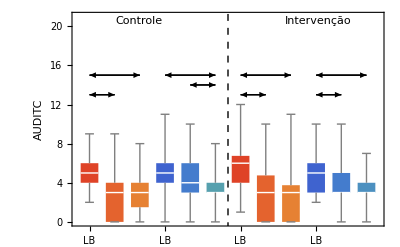

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabmdaudccompleto.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabtimeaudccompleto.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabciaudccompleto.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/figcompaudccompleto.pdf

```mathematica
Clear[errorBar2];
bbarisco=Select[dataset1,#GRUPO=="I"|| #GRUPO=="C"&];
bbarisco1=Select[bbarisco,#RECUSAIB==0&];
caso="completo";
var="AUDITC";
shortname="audc";
varwaves={var,"z6"<>var,"z12"<>var};
varwavesnames=ToString/@varwaves;
varwavesnamess={"LB","z6", "z12"};
part1=GroupBy[bbarisco1,{#GRUPO,#SEXOS}&];
teste=Dataset[Table[Normal[Keys[part1]][[i]]->N[Mean[part1[[i]][All,"AUDITC"]]],{i,1,Length[part1]}]];
maxplot=21;
lissig=Flatten[Transpose[Flatten[Table[{Table[LocationTest[{gerapart[part1[[i]],varwaves[[j]]],gerapart[part1[[i]],varwaves[[k]]]},0],{i,1,4}]},{k,2,3},{j,1,k-1}],2]]];
pos=Flatten[Table[{errorBar2[{i,maxplot-8},{i+1,maxplot-8}],errorBar2[{i,maxplot-6},{i+2,maxplot-6}],errorBar2[{i+1,maxplot-7},{i+2,maxplot-7}]},{i,1,10,3}]];
pos2=(First/@Select[Transpose[{pos,lissig}],#[[2]]<0.05&])/.errorBar2[x_,y_]->errorBar[x,y];
gr1=BoxWhiskerChart[Flatten[Table[gerapart[part1[[i]],#]&/@varwaves,{i,1,4}],1],
ChartLabels->{"LB",6,12,"LB",6,12,"LB",6,12,"LB",6,12},ChartStyle->{ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.9],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.25],ColorData["Rainbow"][0.35],ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.9],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.25],ColorData["Rainbow"][0.3]},PlotRange->{0,maxplot},FrameLabel->{"", Style[var,18]},Epilog-> {pos2,Inset[Framed[Style["Intervenção",14]],{11.42,maxplot},{Right,Top}],Inset[Framed[Style["Controle",14]],{2.025,maxplot},{Left,Top}],{Dashed,Line[{{6.5,-0.75},{6.5,maxplot+1}}]}}]

timetable=Flatten[Table[{varwavesnamess[[j]]<>" $\\times$ "<>varwavesnamess[[k]],{"C","I"},{"F","M","F","M"},Table[LocationTest[{gerapart[part1[[i]],varwavesnames[[j]]],gerapart[part1[[i]],varwavesnames[[k]]]},0],{i,1,4}]},{k,2,3},{j,1,k-1}],1];
tabci=Table[LocationTest[{gerapart[part1[[i]],#],gerapart[part1[[i+2]],#]},0,"MannWhitney"]&/@varwaves,{i,1,2}];
tabmd=tabmd=Table[{lis=gerapart[part1[[i]],#];N[Mean[lis]],N[StandardDeviation[lis]]},{i,1,4}]&/@varwaves;
Export[prefix<>"tabmd"<>shortname<>caso<>".tex",geraTabMD[tabmd,var,3],"String"]
Export[prefix<>"tabtime"<>shortname<>caso<>".tex",geratabtime[timetable,2],"String"]
Export[prefix<>"tabci"<>shortname<>caso<>".tex",geraTabCG[tabci,3],"String"]
Export[prefix<>"figcomp"<>shortname<>caso<>".pdf",gr1]
```

```mathematica
compilaTex[geraTabMD[tabmd,var,3],prefix]
```

-Graphics-

```mathematica
compilaTex[geratabtime[timetable,2],prefix]
```

-Graphics-

```mathematica
compilaTex[geraTabCG[tabci,3],prefix]
```

-Graphics-

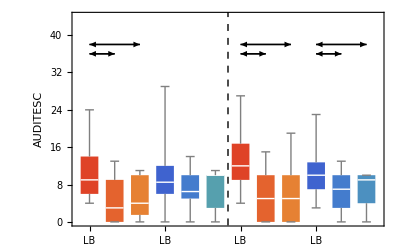

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabmdaudesccompleto.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabtimeaudesccompleto.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabciaudesccompleto.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/figcompaudesccompleto.pdf

```mathematica
bbarisco1=Select[bbarisco,#RECUSAIB==0&];
caso="completo";
var="AUDITESC";
shortname="audesc";
varwaves={var,"z6"<>var,"z12"<>var};
part1=GroupBy[bbarisco1,{#GRUPO,#SEXOS}&];
teste=Dataset[Table[Normal[Keys[part1]][[i]]->N[Mean[part1[[i]][All,"AUDITC"]]],{i,1,Length[part1]}]];
maxplot=44;
lissig=Flatten[Transpose[Flatten[Table[{Table[LocationTest[{gerapart[part1[[i]],varwaves[[j]]],gerapart[part1[[i]],varwaves[[k]]]},0],{i,1,4}]},{k,2,3},{j,1,k-1}],2]]];
pos=Flatten[Table[{errorBar2[{i,maxplot-8},{i+1,maxplot-8}],errorBar2[{i,maxplot-6},{i+2,maxplot-6}],errorBar2[{i+1,maxplot-7},{i+2,maxplot-7}]},{i,1,10,3}]];
pos2=(First/@Select[Transpose[{pos,lissig}],#[[2]]<0.05&])/.errorBar2[x_,y_]->errorBar[x,y];
gr1=BoxWhiskerChart[Flatten[Table[gerapart[part1[[i]],#]&/@varwaves,{i,1,4}],1],
ChartLabels->{"LB",6,12,"LB",6,12,"LB",6,12,"LB",6,12},ChartStyle->{ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.9],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.25],ColorData["Rainbow"][0.35],ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.9],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.25],ColorData["Rainbow"][0.3]},PlotRange->{0,maxplot},FrameLabel->{"", Style[var,18]},Epilog-> {pos2,Inset[Framed[Style["Intervenção",14]],{11.42,maxplot+2},{Right,Top}],Inset[Framed[Style["Controle",14]],{2.025,maxplot+2},{Left,Top}],{Dashed,Line[{{6.5,-0.75},{6.5,maxplot+1}}]}}]

timetable=Flatten[Table[{varwavesnamess[[j]]<>" $\\times$ "<>varwavesnamess[[k]],{"C","I"},{"F","M","F","M"},Table[LocationTest[{gerapart[part1[[i]],varwaves[[j]]],gerapart[part1[[i]],varwaves[[k]]]},0],{i,1,4}]},{k,2,3},{j,1,k-1}],1];
tabci=Table[LocationTest[{gerapart[part1[[i]],#],gerapart[part1[[i+2]],#]},0,"MannWhitney"]&/@varwaves,{i,1,2}];
tabmd=tabmd=Table[{lis=gerapart[part1[[i]],#];N[Mean[lis]],N[StandardDeviation[lis]]},{i,1,4}]&/@varwaves;
Export[prefix<>"tabmd"<>shortname<>caso<>".tex",geraTabMD[tabmd,var,3],"String"]
Export[prefix<>"tabtime"<>shortname<>caso<>".tex",geratabtime[timetable,3],"String"]
Export[prefix<>"tabci"<>shortname<>caso<>".tex",geraTabCG[tabci,3],"String"]
Export[prefix<>"figcomp"<>shortname<>caso<>".pdf",gr1]
```

```mathematica
compilaTex[geraTabMD[tabmd,var,3],prefix]
compilaTex[geratabtime[timetable,2],prefix]
compilaTex[geraTabCG[tabci,3],prefix]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

### Agora só mantemos os que responderam todos os ítens

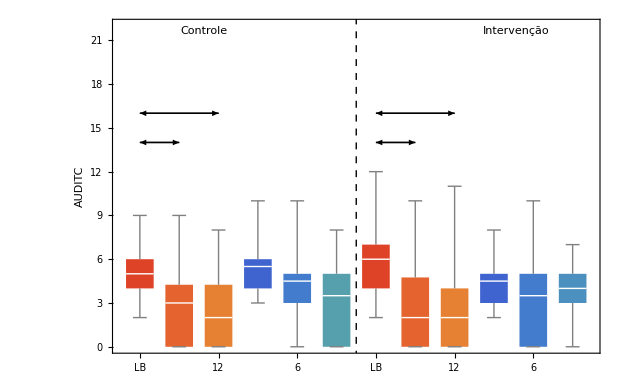

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabmdaudcparcial.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabtimeaudcparcial.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabciaudcparcial.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/figcompaudcparcial.pdf

```mathematica
bbarisco1=Select[bbarisco,#RECUSAIB==0 && #"RecusaIB6"==0 && #RecusaIB12==0&];
caso="parcial";
var="AUDITC";
shortname="audc";
varwaves={var,"z6"<>var,"z12"<>var};
part1=GroupBy[bbarisco1,{#GRUPO,#SEXOS}&];
teste=Dataset[Table[Normal[Keys[part1]][[i]]->N[Mean[part1[[i]][All,"AUDITC"]]],{i,1,Length[part1]}]];
maxplot=22;
lissig=Flatten[Transpose[Flatten[Table[{Table[LocationTest[{gerapart[part1[[i]],varwaves[[j]]],gerapart[part1[[i]],varwaves[[k]]]},0,"Sign"],{i,1,4}]},{k,2,3},{j,1,k-1}],2]]];
pos=Flatten[Table[{errorBar2[{i,maxplot-8},{i+1,maxplot-8}],errorBar2[{i,maxplot-6},{i+2,maxplot-6}],errorBar2[{i+1,maxplot-7},{i+2,maxplot-7}]},{i,1,10,3}]];
pos2=(First/@Select[Transpose[{pos,lissig}],#[[2]]<0.05&])/.errorBar2[x_,y_]->errorBar[x,y];
gr1=BoxWhiskerChart[Flatten[Table[gerapart[part1[[i]],#]&/@varwaves,{i,1,4}],1],
ChartLabels->{"LB",6,12,"LB",6,12,"LB",6,12,"LB",6,12},ChartStyle->{ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.9],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.25],ColorData["Rainbow"][0.35],ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.9],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.25],ColorData["Rainbow"][0.3]},PlotRange->{0,maxplot},FrameLabel->{"", Style[var,18]},Epilog-> {pos2,Inset[Framed[Style["Intervenção",14]],{11.42,maxplot},{Right,Top}],Inset[Framed[Style["Controle",14]],{2.025,maxplot},{Left,Top}],{Dashed,Line[{{6.5,-0.75},{6.5,maxplot+1}}]}}]

timetable=Flatten[Table[{varwavesnamess[[j]]<>" $\\times$ "<>varwavesnamess[[k]],{"C","I"},{"F","M","F","M"},Table[LocationTest[{gerapart[part1[[i]],varwaves[[j]]],gerapart[part1[[i]],varwaves[[k]]]},0,"Sign"],{i,1,4}]},{k,2,3},{j,1,k-1}],1];
tabci=Table[LocationTest[{gerapart[part1[[i]],#],gerapart[part1[[i+2]],#]},0,"MannWhitney"]&/@varwaves,{i,1,2}];
tabmd=tabmd=Table[{lis=gerapart[part1[[i]],#];N[Mean[lis]],N[StandardDeviation[lis]]},{i,1,4}]&/@varwaves;
Export[prefix<>"tabmd"<>shortname<>caso<>".tex",geraTabMD[tabmd,var,3],"String"]
Export[prefix<>"tabtime"<>shortname<>caso<>".tex",geratabtime[timetable,2],"String"]
Export[prefix<>"tabci"<>shortname<>caso<>".tex",geraTabCG[tabci,3],"String"]
Export[prefix<>"figcomp"<>shortname<>caso<>".pdf",gr1]
```

```mathematica
compilaTex[geraTabMD[tabmd,var,3],prefix]
compilaTex[geratabtime[timetable,2],prefix]
compilaTex[geraTabCG[tabci,3],prefix]
```

-Graphics-

-Graphics-

-Graphics-

### Agora para AUDITESC

#### Todos os que iniciaram o levantamento

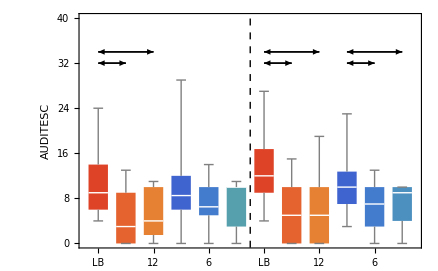

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabmdaudesccompleto.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabtimeaudesccompleto.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabciaudesccompleto.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/figcompaudesccompleto.pdf

```mathematica
bbarisco1=Select[bbarisco,#RECUSAIB==0&];
caso="completo";
var="AUDITESC";
shortname="audesc";
varwaves={var,"z6"<>var,"z12"<>var};
part1=GroupBy[bbarisco1,{#GRUPO,#SEXOS}&];
teste=Dataset[Table[Normal[Keys[part1]][[i]]->N[Mean[part1[[i]][All,"AUDITC"]]],{i,1,Length[part1]}]];
maxplot=40;
lissig=Flatten[Transpose[Flatten[Table[{Table[LocationTest[{gerapart[part1[[i]],varwaves[[j]]],gerapart[part1[[i]],varwaves[[k]]]},0],{i,1,4}]},{k,2,3},{j,1,k-1}],2]]];
pos=Flatten[Table[{errorBar2[{i,maxplot-8},{i+1,maxplot-8}],errorBar2[{i,maxplot-6},{i+2,maxplot-6}],errorBar2[{i+1,maxplot-7},{i+2,maxplot-7}]},{i,1,10,3}]];
pos2=(First/@Select[Transpose[{pos,lissig}],#[[2]]<0.05&])/.errorBar2[x_,y_]->errorBar[x,y];
gr1=BoxWhiskerChart[Flatten[Table[gerapart[part1[[i]],#]&/@varwaves,{i,1,4}],1],
ChartLabels->{"LB",6,12,"LB",6,12,"LB",6,12,"LB",6,12},ChartStyle->{ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.9],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.25],ColorData["Rainbow"][0.35],ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.9],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.25],ColorData["Rainbow"][0.3]},PlotRange->{0,maxplot},FrameLabel->{"", Style[var,18]},Epilog-> {pos2,Inset[Framed[Style["Intervenção",14]],{11.42,maxplot+1.2},{Right,Top}],Inset[Framed[Style["Controle",14]],{2.025,maxplot+1.2},{Left,Top}],{Dashed,Line[{{6.5,-0.75},{6.5,maxplot+1}}]}}]

timetable=Flatten[Table[{varwavesnamess[[j]]<>" $\\times$ "<>varwavesnamess[[k]],{"C","I"},{"F","M","F","M"},Table[LocationTest[{gerapart[part1[[i]],varwaves[[j]]],gerapart[part1[[i]],varwaves[[k]]]},0],{i,1,4}]},{k,2,3},{j,1,k-1}],1];
tabci=Table[LocationTest[{gerapart[part1[[i]],#],gerapart[part1[[i+2]],#]},0,"MannWhitney"]&/@varwaves,{i,1,2}];
tabmd=tabmd=Table[{lis=gerapart[part1[[i]],#];N[Mean[lis]],N[StandardDeviation[lis]]},{i,1,4}]&/@varwaves;
Export[prefix<>"tabmd"<>shortname<>caso<>".tex",geraTabMD[tabmd,var,3],"String"]
Export[prefix<>"tabtime"<>shortname<>caso<>".tex",geratabtime[timetable,2],"String"]
Export[prefix<>"tabci"<>shortname<>caso<>".tex",geraTabCG[tabci,3],"String"]
Export[prefix<>"figcomp"<>shortname<>caso<>".pdf",gr1]
```

```mathematica
compilaTex[geraTabMD[tabmd,var,3],prefix]
compilaTex[geratabtime[timetable,2],prefix]
compilaTex[geraTabCG[tabci,3],prefix]
```

-Graphics-

-Graphics-

-Graphics-

#### Só os que ficaram até o fim

```mathematica
lissig
```

{3.28823×10^-8,4.35828×10^-10,0.473844,0.0235114,0.0102047,0.573508,9.79715×10^-7,2.32701×10^-7,0.752256,0.017848,0.00203464,1.}

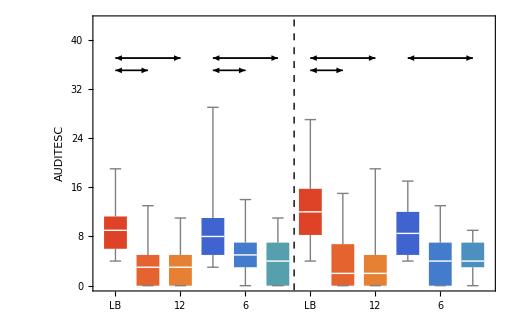

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabmdaudescparcial.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabtimeaudescparcial.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabciaudescparcial.tex

/Users/neylemke/Luisa/BancodeDadosDoutorado/figcompaudescparcial.pdf

```mathematica
bbarisco1=Select[bbarisco,#RECUSAIB==0 && #"RecusaIB6"==0 && #RecusaIB12==0&];
part1=GroupBy[bbarisco1,{#GRUPO,#SEXOS}&];
caso="parcial";
var="AUDITESC";
shortname="audesc";
varwaves={var,"z6"<>var,"z12"<>var};
teste=Dataset[Table[Normal[Keys[part1]][[i]]->N[Mean[part1[[i]][All,"var"]]],{i,1,Length[part1]}]];
maxplot=43;
lissig=Flatten[Transpose[Flatten[Table[{Table[LocationTest[{gerapart[part1[[i]],varwaves[[j]]],gerapart[part1[[i]],varwaves[[k]]]},0,"Sign"],{i,1,4}]},{k,2,3},{j,1,k-1}],2]]];
pos=Flatten[Table[{errorBar2[{i,maxplot-8},{i+1,maxplot-8}],errorBar2[{i,maxplot-6},{i+2,maxplot-6}],errorBar2[{i+1,maxplot-7},{i+2,maxplot-7}]},{i,1,10,3}]];
pos2=(First/@Select[Transpose[{pos,lissig}],#[[2]]<0.05&])/.errorBar2[x_,y_]->errorBar[x,y];
gr1=BoxWhiskerChart[Flatten[Table[gerapart[part1[[i]],#]&/@varwaves,{i,1,4}],1],
ChartLabels->{"LB",6,12,"LB",6,12,"LB",6,12,"LB",6,12},ChartStyle->{ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.9],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.25],ColorData["Rainbow"][0.35],ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.9],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.25],ColorData["Rainbow"][0.3]},PlotRange->{0,maxplot},FrameLabel->{"", Style[var,18]},Epilog-> {pos2,Inset[Framed[Style["Intervenção",14]],{11.42,maxplot+1.7},{Right,Top}],Inset[Framed[Style["Controle",14]],{2.025,maxplot+1.7},{Left,Top}],{Dashed,Line[{{6.5,-0.75},{6.5,maxplot+1}}]}}]

timetable=Flatten[Table[{varwavesnamess[[j]]<>" $\\times$ "<>varwavesnamess[[k]],{"C","I"},{"F","M","F","M"},Table[LocationTest[{gerapart[part1[[i]],varwaves[[j]]],gerapart[part1[[i]],varwaves[[k]]]},0,"Sign"],{i,1,4}]},{k,2,3},{j,1,k-1}],1];
tabci=Table[LocationTest[{gerapart[part1[[i]],#],gerapart[part1[[i+2]],#]},0,"MannWhitney"]&/@varwaves,{i,1,2}];
tabmd=tabmd=Table[{lis=gerapart[part1[[i]],#];N[Mean[lis]],N[StandardDeviation[lis]]},{i,1,4}]&/@varwaves;
Export[prefix<>"tabmd"<>shortname<>caso<>".tex",geraTabMD[tabmd,var,3],"String"]
Export[prefix<>"tabtime"<>shortname<>caso<>".tex",geratabtime[timetable,3],"String"]
Export[prefix<>"tabci"<>shortname<>caso<>".tex",geraTabCG[tabci,3],"String"]
Export[prefix<>"figcomp"<>shortname<>caso<>".pdf",gr1]
```

```mathematica
compilaTex[geraTabMD[tabmd,var,3],prefix]
compilaTex[geratabtime[timetable,2],prefix]
compilaTex[geraTabCG[tabci,3],prefix]
```

-Graphics-

-Graphics-

-Graphics-

### Frequência

```mathematica
bbarisco1=Select[bbarisco,#RECUSAIB==0 && #"RecusaIB6"==0 && #RecusaIB12==0&];
caso="parcial";
var="AFQBEB10";
shortname="audesc";
varwaves={var,"z6"<>var,"z12"<>var};
```

#### Inicial

```mathematica
datasetz1=Select[dataset1,#RECUSAIB==0&];
datasetcontrolez1=Select[datasetz1,#GRUPO=="C"&];
datasetintervencaoz1=Select[datasetz1,#GRUPO=="I"&];
datasettotalz1=Select[datasetz1,#GRUPO=="I" || #GRUPO=="C"&];
```

```mathematica
concTexHelper[list_]:=If[list=={},"",First[list]<>" & "<>concTexHelper[Rest[list]]]
concTex[list_]:=StringTake[concTexHelper[list],{1,-3}]<>"\\\\\n"

geraTabPart[tabci_,titulo_,prec_]:=Module[{stringtable,comment,header,footer,lis1},header="\\begin{tabular}{lrrrrrr}
       \\toprule
&\\multicolumn{6}{c}{"<>titulo<>"}\\\\
\\midrule
        & \\multicolumn{2}{c}{Mulheres} & \\multicolumn{2}{c}{Homens} & \\multicolumn{2}{c}{Total} \\\\
       \\cmidrule(r){2-3}  \\cmidrule(r){4-5}  \\cmidrule(r){6-7} 
       & N & \% & N & \% & N & \%  \\\\\n  \\midrule \n";
stringtable=StringJoin[Table[
lis1=geraNumTex[#,prec]&/@tabci[[i,2;;-1]];
tabci[[i,1]]<>" & "<>concTex[lis1]<>"\n",{i,1,Length[tabci]}]
];
stringtable=corrigeAcentos[stringtable];
geraTable[header,stringtable]]


geraTabHelper[tabci_,titulo_,prec_]:=Module[{header,stringtable},
header="\\midrule
&\\multicolumn{6}{c}{"<>titulo<>"}\\\\
\\midrule
        & \\multicolumn{2}{c}{Mulheres} & \\multicolumn{2}{c}{Homens} & \\multicolumn{2}{c}{Total} \\\\
       \\cmidrule(r){2-3}  \\cmidrule(r){4-5}  \\cmidrule(r){6-7} 
       & N & \% & N & \% & N & \%  \\\\\n  \\midrule \n";
stringtable=StringJoin[Table[
lis1=geraNumTex[#,prec]&/@tabci[[i,2;;-1]];
tabci[[i,1]]<>" & "<>concTex[lis1]<>"\n",{i,1,Length[tabci]}]
];
header<>stringtable
]
```

Syntax::stresc: Unknown string escape \"c".

```mathematica
geraTabVar[listab_,titulo_,prec_]:=Module[{stringtable,comment,header,footer,lis1},header="\\begin{tabular}{lrrrrrr}
       \\toprule" <> "\\multicolumn{6}{c}{"<> titulo<>"}\\\\";
stringtable=StringJoin[Table[geraTabHelperVar[listab[[i,1]],listab[[i,2]],prec],{i,1,Length[listab]}]];
stringtable=corrigeAcentos[stringtable];
geraTable[header,stringtable]]
geraTabHelperVar[tabci_,titulo_,prec_]:=Module[{header,stringtable},
header="\\midrule
&\\multicolumn{6}{c}{"<>titulo<>"}\\\\
\\midrule
        & \\multicolumn{2}{c}{Controle} & \\multicolumn{2}{c}{Interven\\c{c}\\~ao} & \\multicolumn{2}{c}{Total} \\\\
       \\cmidrule(r){2-3}  \\cmidrule(r){4-5}  \\cmidrule(r){6-7} 
       & N & \% & N & \% & N & \%  \\\\\n  \\midrule \n";
stringtable=StringJoin[Table[
lis1=geraNumTex[#,prec]&/@tabci[[i,2;;-1]];
tabci[[i,1]]<>" & "<>concTex[lis1]<>"\n",{i,1,Length[tabci]}]
];
header<>stringtable
]
```

```mathematica
tabciz1=Append[Table[Flatten[{hashfreq[value],geraporcento2[datasetcontrolez1,#AFREQBEB==value&],geraporcento2[datasetintervencaoz1,#AFREQBEB==value&],geraporcento2[datasettotalz1,#AFREQBEB==value&]}],{value,0,4}],
{"Total",Length[datasetcontrolez1],100,Length[datasetintervencaoz1],100,Length[datasettotalz1],100}];
```

#### Seis Meses

```mathematica
datasetz6=Select[dataset1,#RECUSAIB==0 && #RecusaIB6==0&];
datasetcontrolez6=Select[datasetz6,#GRUPO=="C"&];
datasetintervencaoz6=Select[datasetz6,#GRUPO=="I"&];
datasettotalz6=Select[datasetz6,#GRUPO=="I" || #GRUPO=="C"&];
tabciz6=Append[Table[Flatten[{hashfreq[value],geraporcento2[datasetcontrolez6,#z6FREQBE==value&],geraporcento2[datasetintervencaoz6,#z6FREQBE==value&],geraporcento2[datasettotalz6,#z6FREQBE==value&]}],{value,0,4}],{"Total",Length[datasetcontrolez6],100,Length[datasetintervencaoz6],100,Length[datasettotalz6],100}];
```

#### Doze Meses

```mathematica
datasetz12=Select[dataset1,#RECUSAIB==0 && #RecusaIB6==0 &&  #RecusaIB12==0&];
datasetcontrolez12=Select[datasetz12,#GRUPO=="C"&];
datasetintervencaoz12=Select[datasetz12,#GRUPO=="I"&];
datasettotalz12=Select[datasetz12,#GRUPO=="I" || #GRUPO=="C"&];
tabciz12=Append[Table[Flatten[{hashfreq[value],geraporcento2[datasetcontrolez12,#z12FREQB==value&],geraporcento2[datasetintervencaoz12,#z12FREQB==value&],geraporcento2[datasettotalz12,#z12FREQB==value&]}],{value,0,4}],{"Total",Length[datasetcontrolez12],100,Length[datasetintervencaoz12],100,Length[datasettotalz12],100}];
```

```mathematica
Export[prefix<>"tabVarFreq.tex",geraTabVar[{{tabciz1,"Linha de Base"},{tabciz6,"6 Meses"},{tabciz12,"12 Meses"}},"Frequ\\^encia com que bebeu 30 dias",2],"String"];
```

```mathematica
compilaTex[geraTabVar[{{tabciz1,"Linha de Base"},{tabciz6,"6 Meses"},{tabciz12,"12 Meses"}},"Frequ\\^encia com que bebeu 30 dias",2],prefix]
```

-Graphics-

### Maior Dose Consumida

```mathematica
tabciz1=Append[Table[Flatten[{hashaoc[value],geraporcento2[datasetcontrolez1,#AOCMAISB==value&],geraporcento2[datasetintervencaoz1,#AOCMAISB==value&],geraporcento2[datasettotalz1,#AOCMAISB==value&]}],{value,0,3}],
{"Total",Length[datasetcontrolez1],100,Length[datasetintervencaoz1],100,Length[datasettotalz1],100}];
```

#### Seis Meses

```mathematica
datasetz6=Select[dataset1,#RECUSAIB==0 && #RecusaIB6==0&];
datasetcontrolez6=Select[datasetz6,#GRUPO=="C"&];
datasetintervencaoz6=Select[datasetz6,#GRUPO=="I"&];
datasettotalz6=Select[datasetz6,#GRUPO=="I" || #GRUPO=="C"&];
tabciz6=Append[Table[Flatten[{hashaoc[value],geraporcento2[datasetcontrolez6,#z6OCMAIS==value&],geraporcento2[datasetintervencaoz6,#z6OCMAIS==value&],geraporcento2[datasettotalz6,#z6OCMAIS==value&]}],{value,0,3}],{"Total",Length[datasetcontrolez6],100,Length[datasetintervencaoz6],100,Length[datasettotalz6],100}];
```

#### Doze Meses

```mathematica
datasetz12=Select[dataset1,#RECUSAIB==0 && #RecusaIB6==0 &&  #RecusaIB12==0&];
datasetcontrolez12=Select[datasetz12,#GRUPO=="C"&];
datasetintervencaoz12=Select[datasetz12,#GRUPO=="I"&];
datasettotalz12=Select[datasetz12,#GRUPO=="I" || #GRUPO=="C"&];
tabciz12=Append[Table[Flatten[{hashaoc[value],geraporcento2[datasetcontrolez12,#z12OCMAB==value&],geraporcento2[datasetintervencaoz12,#z12OCMAB==value&],geraporcento2[datasettotalz12,#z12OCMAB==value&]}],{value,0,3}],{"Total",Length[datasetcontrolez12],100,Length[datasetintervencaoz12],100,Length[datasettotalz12],100}];
```

```mathematica
Export[prefix<>"tabVarAOC.tex",geraTabVar[{{tabciz1,"Linha de Base"},{tabciz6,"6 Meses"},{tabciz12,"12 Meses"}},"Maior Dose Consumida",2],"String"];
```

```mathematica
compilaTex[geraTabVar[{{tabciz1,"Linha de Base"},{tabciz6,"6 Meses"},{tabciz12,"12 Meses"}},"Maior Dose Consumida",2],prefix]
```

-Graphics-

Attrition

```mathematica
bbacomp=Select[bbarisco,#RECUSAIB==0 && #"RecusaIB6"==0 && #RecusaIB12==0&];
bbaabandonaram=Select[bbarisco,#RECUSAIB==0 && (#"RecusaIB6" !=0 || #RecusaIB12!=0)&];


partcomp=GroupBy[bbacomp,#SEXOS&];
partabandonaram=GroupBy[bbaabandonaram,#SEXOS&];
```

```mathematica
lisvars={"AUDITESC","AUDITC","DROGAS12"};

tabci=Transpose[{LocationTest[{Select[Normal[partcomp[[1]][All,#]],IntegerQ],Select[Normal[partabandonaram[[1]][All,#]],IntegerQ]}],LocationTest[{Select[Normal[partcomp[[2]][All,#]],IntegerQ],Select[Normal[partabandonaram[[2]][All,#]],IntegerQ]}]}&/@lisvars];
Export[prefix<>"tabciattrition.tex",geraTabAtt[tabci,3],"String"]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabciattrition.tex

0.252366

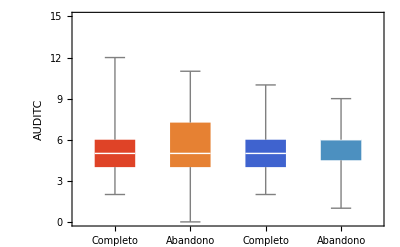

/Users/neylemke/Dropbox/Luisa/tese/attritionauditc.pdf

```mathematica
g1=BoxWhiskerChart[{Normal[partcomp[[1]][All,"AUDITC"]],Normal[partabandonaram[[1]][All,"AUDITC"]],Normal[partcomp[[2]][All,"AUDITC"]],Normal[partabandonaram[[2]][All,"AUDITC"]]},ChartLabels->{"Completo","Abandono","Completo","Abandono"},ChartStyle->{ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.3]},PlotRange->{0,15},FrameLabel->{"", Style["AUDITC",18]}]

Export["/Users/neylemke/Dropbox/Luisa/tese/attritionauditc.pdf",g1]
```

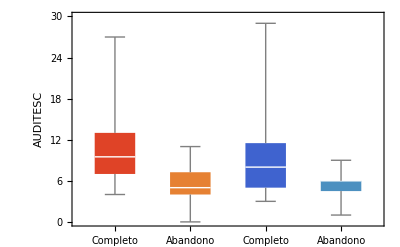

/Users/neylemke/Dropbox/Luisa/tese/attritionauditesc.pdf

```mathematica
g1=BoxWhiskerChart[{Normal[partcomp[[1]][All,"AUDITESC"]],Normal[partabandonaram[[1]][All,"AUDITC"]],Normal[partcomp[[2]][All,"AUDITESC"]],Normal[partabandonaram[[2]][All,"AUDITC"]]},ChartLabels->{"Completo","Abandono","Completo","Abandono"},ChartStyle->{ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.3]},PlotRange->{0,30},FrameLabel->{"", Style["AUDITESC",18]}]
Export["/Users/neylemke/Dropbox/Luisa/tese/attritionauditesc.pdf",g1]
```

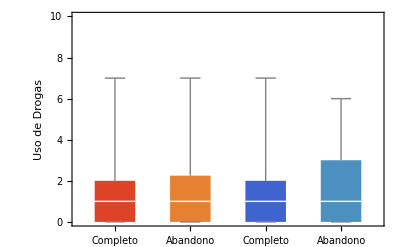

/Users/neylemke/Dropbox/Luisa/tese/attritiondrogas.pdf

```mathematica
bbacomp=Select[bbarisco,#RECUSAIB==0 && #"RecusaIB6"==0 && #RecusaIB12==0&];
bbaabandonaram=Select[bbarisco,#RECUSAIB==0 && (#"RecusaIB6" !=0 || #RecusaIB12!=0)&];

partcomp=GroupBy[bbacomp,#SEXOS&];
partabandonaram=GroupBy[bbaabandonaram,#SEXOS&];
g1=BoxWhiskerChart[{Normal[partcomp[[1]][All,"DROGAS12"]],Normal[partabandonaram[[1]][All,"DROGAS12"]],Normal[partcomp[[2]][All,"DROGAS12"]],Normal[partabandonaram[[2]][All,"DROGAS12"]]},ChartLabels->{"Completo","Abandono","Completo","Abandono"},ChartStyle->{ColorData["Rainbow"][0.95],ColorData["Rainbow"][0.85],ColorData["Rainbow"][0.2],ColorData["Rainbow"][0.3]},PlotRange->{0,10},FrameLabel->{"", Style["Uso de Drogas",18]}]
Export["/Users/neylemke/Dropbox/Luisa/tese/attritiondrogas.pdf",g1]
```

Correlação entre Uso de Alcool e uso de Drogas

```mathematica
bbacomp=Select[bbarisco,#RECUSAIB==0 && #"RecusaIB6"==0 && #RecusaIB12==0&];
partcomp=GroupBy[bbacomp,#SEXOS&];
dataset2=bbacomp;
```

```mathematica
lisvar={"AUDITC","DROGAS30","DROGAS12","z6AUDITC","z6DROGAS30","z12AUDITC","z12DROGAS30"};
lisvar2={"var name","AUDITC","DROGAS30","DROGAS12","z6AUDITC","z6DROGAS30","z12AUDITC","z12DROGAS30"};
corrTabTeste=Table[listemp=Cases[Transpose[{Normal[dataset2[All,lisvar[[i]]]],Normal[dataset2[All,lisvar[[j]]]]}],{_Integer,_Integer}];
N[CorrelationTest[listemp],2],{i,1,Length[lisvar]},{j,1,Length[lisvar]}];
corrTab=Table[listemp=Cases[Transpose[{Normal[dataset2[All,lisvar[[i]]]],Normal[dataset2[All,lisvar[[j]]]]}],{_Integer,_Integer}];
N[Correlation[listemp[[All,1]],listemp[[All,2]]]]
,{i,1,Length[lisvar]},{j,1,Length[lisvar]}];
corrTabTable=TableForm[corrTab,TableHeadings->{hashVarNames/@lisvar,hashVarNames/@lisvar}];
headerString=StringJoin[ " & "<> #&/@ hashVarNames/@lisvar]<>"\\\\\n \\midrule\n ";
colString="l|"<>StringJoin[Table["c",{i,1,Length[corrTab]}]];
corrTabTex="\n\n\\begin{tabular}{"<>colString<>"}\n\\toprule\n"<> headerString<>StringJoin[Table[StringJoin[" "<> hashVarNames[lisvar[[j]]], Table[" & \\nprounddigits{2}"<>If[ corrTabTeste[[i,j]]>0.05,"\\numprint{"<>ToString[CForm[corrTab[[i,j]]]],"{\\bf \\numprint{ "<> ToString[CForm[corrTab[[i,j]]]]<>"}" ]<>"}",{i,1,Length[corrTab]}]]<> "\\\\\n",{j,1,Length[corrTab]}]]<>" \\bottomrule\n\\end{tabular}";
Export[prefix<>"corrdrogasaudc.tex",corrTabTex, "String"];
compilaTex[corrTabTex,prefix]
```

-Graphics-

```mathematica
lisvar={"AUDITESC","DROGAS30","DROGAS12","z6AUDITESC","z6DROGAS30","z12AUDITESC","z12DROGAS30"};
lisvar2={"var name","AUDITESC","DROGAS30","DROGAS12","z6AUDITESC","z6DROGAS30","z12AUDITESC","z12DROGAS30"};
corrTabTeste=Table[listemp=Cases[Transpose[{Normal[dataset2[All,lisvar[[i]]]],Normal[dataset2[All,lisvar[[j]]]]}],{_Integer,_Integer}];
N[CorrelationTest[listemp],2],{i,1,Length[lisvar]},{j,1,Length[lisvar]}];
corrTab=Table[listemp=Cases[Transpose[{Normal[dataset2[All,lisvar[[i]]]],Normal[dataset2[All,lisvar[[j]]]]}],{_Integer,_Integer}];
N[Correlation[listemp[[All,1]],listemp[[All,2]]]]
,{i,1,Length[lisvar]},{j,1,Length[lisvar]}];
corrTabTable=TableForm[corrTab,TableHeadings->{hashVarNames/@lisvar,hashVarNames/@lisvar}];
headerString=StringJoin[ " & "<> #&/@ hashVarNames/@lisvar]<>"\\\\\n \\midrule\n ";
colString="l|"<>StringJoin[Table["c",{i,1,Length[corrTab]}]];
corrTabTex="\n\n\\begin{tabular}{"<>colString<>"}\n\\toprule\n"<> headerString<>StringJoin[Table[StringJoin[" "<> hashVarNames[lisvar[[j]]], Table[" & \\nprounddigits{2}"<>If[ corrTabTeste[[i,j]]>0.05,"\\numprint{"<>ToString[CForm[corrTab[[i,j]]]],"{\\bf \\numprint{ "<> ToString[CForm[corrTab[[i,j]]]]<>"}" ]<>"}",{i,1,Length[corrTab]}]]<> "\\\\\n",{j,1,Length[corrTab]}]]<>" \\bottomrule\n\\end{tabular}";
Export[prefix<>"corrdrogasaudesc.tex",corrTabTex, "String"];
compilaTex[corrTabTex,prefix]
```

-Graphics-

-Graphics-

```mathematica
Prepend[Prepend[Table[par=geraCorr[lisvar[[i]],lisvar[[j]]];If[par[[2]]<0.05,Style[par[[1]],Black],Style[par[[1]],Red]],{i,1,Length[lisvar]},{j,1,Length[lisvar]}],lisvar]//Transpose,lisvar2]//Transpose//Grid
```

var name | AUDITC | DROGAS30 | DROGAS12 | z6AUDITC | z6DROGAS30 | z12AUDITC | z12DROGAS30
AUDITC | If[AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS12<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]]
DROGAS30 | If[AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS12<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]]
DROGAS12 | If[AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS12<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]]
z6AUDITC | If[AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS12<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]]
z6DROGAS30 | If[AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS12<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]]
z12AUDITC | If[AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS12<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]]
z12DROGAS30 | If[AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[DROGAS12<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z6DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12AUDITC<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]] | If[z12DROGAS30<0.05,Style[par⟦1⟧,Black],Style[par⟦1⟧,Red]]

```mathematica
lisvar={"AUDITC","DROGAS30BIT","DROGAS12BIT","z6AUDITC","z6DROGAS30BIT","z12AUDITC","z12DROGAS30BIT"};

corrTabTeste=Table[listemp=Cases[Transpose[{Normal[dataset2[All,lisvar[[i]]]],Normal[dataset2[All,lisvar[[j]]]]}],{_Integer,_Integer}];
N[CorrelationTest[listemp],2],{i,1,Length[lisvar]},{j,1,Length[lisvar]}];
corrTab=Table[listemp=Cases[Transpose[{Normal[dataset2[All,lisvar[[i]]]],Normal[dataset2[All,lisvar[[j]]]]}],{_Integer,_Integer}];
N[Correlation[listemp[[All,1]],listemp[[All,2]]]]
,{i,1,Length[lisvar]},{j,1,Length[lisvar]}];
corrTabTable=TableForm[corrTab,TableHeadings->{hashVarNames/@lisvar,hashVarNames/@lisvar}]
```

| LB:AUDITC | LB:DROGAS30 | LB:DROGAS12 | 6:AUDITC | 6:DROGAS30 | 12:AUDITC | 12:DROGAS30
LB:AUDITC | 1. | 0.255164 | 0.207206 | 0.196494 | 0.242668 | 0.202875 | 0.0564159
LB:DROGAS30 | 0.255164 | 1. | 0.716903 | 0.298139 | 0.381742 | 0.395852 | 0.358624
LB:DROGAS12 | 0.207206 | 0.716903 | 1. | 0.329318 | 0.397508 | 0.344292 | 0.247055
6:AUDITC | 0.196494 | 0.298139 | 0.329318 | 1. | 0.394896 | 0.537164 | 0.0491241
6:DROGAS30 | 0.242668 | 0.381742 | 0.397508 | 0.394896 | 1. | 0.134535 | 0.206708
12:AUDITC | 0.202875 | 0.395852 | 0.344292 | 0.537164 | 0.134535 | 1. | 0.383058
12:DROGAS30 | 0.0564159 | 0.358624 | 0.247055 | 0.0491241 | 0.206708 | 0.383058 | 1.

```mathematica
headerString=StringJoin[ " & "<> #&/@ hashVarNames/@lisvar]<>"\\\\\n \\midrule\n ";
colString="l|"<>StringJoin[Table["c",{i,1,Length[corrTab]}]];
corrTabTex="\n\n\\begin{tabular}{"<>colString<>"}\n\\toprule\n"<> headerString<>StringJoin[Table[StringJoin[" "<> hashVarNames[lisvar[[j]]], Table[" & \\nprounddigits{2}"<>If[ corrTabTeste[[i,j]]>0.05,"\\numprint{"<>ToString[CForm[corrTab[[i,j]]]],"{\\bf \\numprint{ "<> ToString[CForm[corrTab[[i,j]]]]<>"}" ]<>"}",{i,1,Length[corrTab]}]]<> "\\\\\n",{j,1,Length[corrTab]}]]<>" \\bottomrule\n\\end{tabular}";
Export[prefix<>"corrdrogasbit.tex",corrTabTex, "String"]
```

/Users/neylemke/Dropbox/Luisa/tese/corrdrogasbit.tex

Regressão à Média

### Caso Gaussiano

```mathematica
Plot[{1/(Sqrt[2 π]) Exp[-(x-3)^2],If[x>4 ,1/(Sqrt[2 π]) Exp[-(x-3)^2],0]},{x,0,7},Filling->Axis,PlotRange->All]
```

O objetivo é estimar a variação da média ao escolhermos indivíduos com variável x>L e no caso onde as medidas  não estão correlacionadas e obedecem a mesma distribuição. Esse efeito é denotado pela variável E.

A quantidade E pode ser calculada através de:

E=(∫_L^∞ x PDF(x)ⅆx)/(∫_L^∞ PDF(x)ⅆx)-μ

No Caso de uma Normal temos:

-μ+(√(2/π) (ⅇ^(-(L-μ)^2/(2 σ^2)) σ^2+√(π/2) μ σ Erfc[(L-μ)/(√2 σ)]))/(σ Erfc[(L-μ)/(√2 σ)])
Que pode ser simplificado como: 

σ (ϕ(z))/(Φ(z))
onde ϕ é a PDF da Normal Φ é a CDF e 

z=(c-μ)/σ

No caso com dados correlacionados temos:



E=σ_w^2/(√(σ_b^2+σ_w^2))(ϕ(z))/(Φ(z))

σ_t^2 = σ_b^2+σ_w^2

z=(c-μ)/σ_t

σ_b^2=ρ σ_t^2

Temos que 

σ_w^2=σ_t^2 - σ_b^2=σ_t^2-ρ σ_t^2
      =(1-ρ)σ_t^2
      

E=(1-ρ) (ϕ (z))/Φ(z)σ_t

Vamos definir uma função que estime o efeito sobre uma distribuição experimental.

#### Simulação

Vamos testar o caso ρ=0

Vamos testar essa expressão gerando um conjunto de dados gerados por simulação de Monte Carlo.

```mathematica
μ=1.5;
σ=2;
L=4;
lispiloto=Table[RandomVariate[NormalDistribution[μ,σ]],{1000}];
lispart=Select[lispiloto,#>L&];
liswave=Table[RandomVariate[NormalDistribution[μ,σ]],{Length[lispart]}];
{Mean[lispart]-Mean[lispiloto],calcEfeito[lispiloto,L,0]}
```

{3.48927,3.50537}

Só para constar vamos aplicar isso nos nossos dados.

```mathematica
lisRTM=Cases[Normal[dataset1[All,"AUDITESC"]],_Integer]//N;
L=4;
z=(L-Mean[lisRTM])/StandardDeviation[lisRTM];
ρ=Abs[geraCorr[dataset1,"AUDITESC","z6AUDITESC"][[1]]];
μ=Mean[lisRTM];
σ=StandardDeviation[lisRTM];
efeito=calcEfeito[lisRTM,L,ρ];
efeito/Abs[Mean[bbacomp[All,"z6AUDITESC"]]-Mean[bbacomp[All,"AUDITESC"]]//N]
```

0.723247

```mathematica
lisRTM=Cases[Normal[dataset1[All,"AUDITESC"]],_Integer]//N;
lisRTMC=Cases[Normal[dataset1[All,"AUDITC"]],_Integer]//N;
```

### Caso Exponencial

```mathematica
partlsd=Delete[Select[#,#RECUSAIB==0&&#RecusaIB12==0&]&/@(Delete[GroupBy[Select[dataset1,#RECUSA==0&],{#GRUPO}&],1]),1];
liscontrole=(Cases[Normal[partlsd[[1]][All,"AUDITESC"]],_Integer]//N);
lisintervencao=(Cases[Normal[partlsd[[2]][All,"AUDITESC"]],_Integer]//N);
liscontrole1=(Cases[Normal[partlsd[[1]][All,"z1AUDITESC"]],_Integer]//N);
lisintervencao1=(Cases[Normal[partlsd[[2]][All,"z1AUDITESC"]],_Integer]//N);
liscontrolez6=(Cases[Normal[partlsd[[1]][All,"z6AUDITESC"]],_Integer]//N);
lisintervencaoz6=(Cases[Normal[partlsd[[2]][All,"z6AUDITESC"]],_Integer]//N);
liscontrolez12=(Cases[Normal[partlsd[[1]][All,"z12AUDITESC"]],_Integer]//N);
lisintervencaoz12=(Cases[Normal[partlsd[[2]][All,"z12AUDITESC"]],_Integer]//N);
```

Vamos represntar nossos dados, junto com um ajuste linear. A linearidade da curva mostra de forma clara que os dados são distribuídos como um exponencial.

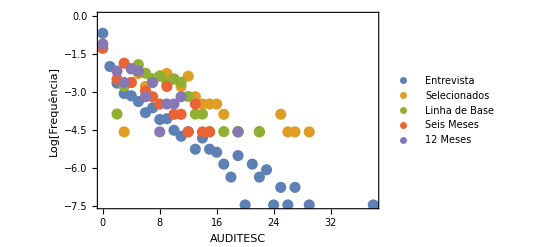

```mathematica
gr1=ListPlot[{Tally[lisRTM]/.{x_,y_}->{x,Log[y/Length[lisRTM]]},
Tally[Join[liscontrole,lisintervencao]]/.{x_,y_}->{x,Log[y/Length[Join[liscontrole,lisintervencao]]]},
Tally[Join[liscontrole1,lisintervencao1]]/.{x_,y_}->{x,Log[y/Length[Join[liscontrole1,lisintervencao1]]]},
Tally[Join[liscontrolez6,lisintervencaoz6]]/.{x_,y_}->{x,Log[y/Length[Join[liscontrolez6,lisintervencaoz6]]]},Tally[Join[liscontrolez12,lisintervencaoz12]]/.{x_,y_}->{x,Log[y/Length[Join[liscontrolez12,lisintervencaoz12]]]}},PlotStyle->PointSize[0.02],PlotLegends->PointLegend[{"Entrevista", "Selecionados","Linha de Base","Seis Meses","12 Meses"}],Frame->True, FrameLabel->{Style["AUDITESC",FontSize->18],Style["Log[Frequência]",FontSize->18]}]
```

```mathematica
lm=LinearModelFit[Tally[Join[liscontrolez6,lisintervencaoz6]]/.{x_,y_}->{x,Log[y/Length[Join[liscontrolez6,lisintervencaoz6]]]},x,x]
```

FittedModel[-1.56848-0.202856 x]

```mathematica
gr4=Plot[Normal[lm],{x,0,35}];
gr5=Show[{gr1,gr4}]
```

-Graphics-

```mathematica
Export[prefix<>"expdist.pdf",gr5]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/expdist.pdf

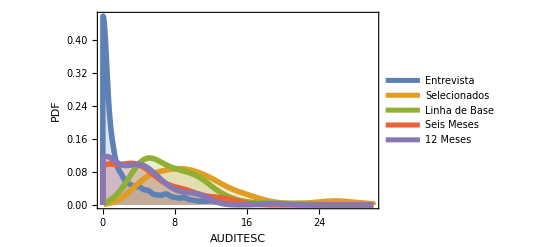

```mathematica
SmoothHistogram[{lisRTM,Join[liscontrole,lisintervencao],Join[liscontrole1,lisintervencao1],Join[liscontrolez6,lisintervencaoz6],Join[liscontrolez12,lisintervencaoz12]},PlotLegends->LineLegend[{"Entrevista", "Selecionados","Linha de Base","Seis Meses","12 Meses"}],Axes->True, PlotRange->{{0,30},All},Filling->Bottom,PlotStyle->{Thickness[0.01]},Frame->True, FrameLabel->{Style["AUDITESC",FontSize->18],Style["PDF",FontSize->18]}]
```

```mathematica
scale=N[Floor[10*(HistogramList[lisRTM][[2,1]])/Length[lisRTM]]/10];
max=1.1;
listicksy=Table[{max*i/5,scale*i/5},{i,0,5}];
```

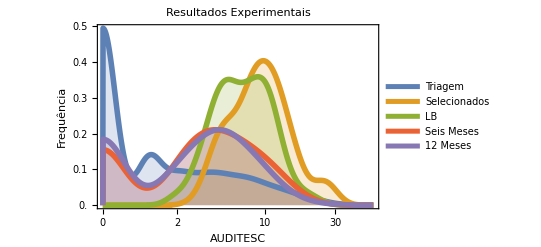

```mathematica
gr1=SmoothHistogram[Log[#+1]&/@{lisRTM,Join[liscontrole,lisintervencao],Join[liscontrole1,lisintervencao1],Join[liscontrolez6,lisintervencaoz6],Join[liscontrolez12,lisintervencaoz12]},PlotLegends->LineLegend[{"Triagem","Selecionados","LB", "Seis Meses","12 Meses"}],Axes->True,PlotRange->{{0,4},All},Filling->Bottom,PlotStyle->{Thickness[0.01]},Frame->True, FrameLabel->{Style["AUDITESC",FontSize->18],Style["Frequência",FontSize->18]},FrameTicks->{listicksy,{{0,{Log[1+1],1},{Log[3],2},{Log[6],5},{Log[11],10},{Log[21],20},{Log[31],30},{Log[51],50}},None}},PlotLabel->Style["Resultados Experimentais", "FontSize"->16]]
```

```mathematica
Export[prefix<>"logdist.pdf",gr1]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/logdist.pdf

No caso de uma distribuição exponencial

PDF(x)=e^(-β x)/β

Podemos testar essa previão nos nossos dados:

```mathematica
Exp[lm["BestFitParameters"][[1]]]

β=-lm["BestFitParameters"][[2]]
```

0.208361

0.202856

Note que aplicamos o logaritmo antes de realizar a modelagem.

Outra hipótese testável é que os casos mais extremos,θ,observados devem obeder a equação:

N e^(-β θ)/β ∼1
-β θ=Log(β/N)

θ=-1/βLog(β/N)

```mathematica
-Log[β/2000]/β
```

45.3334

```mathematica
-Log[β/84]/β
```

28.6532

Comparando com os dados observamos que esses resultados 
são compatíveis com os dados empíricos. O que fortalece a idéia de que essa distribuição é exponencial.

Vamos generalizar os resultados anteriores para esse caso:

E=(∫_L^∞ x PDF(x)ⅆx)/(∫_L^∞ PDF(x)ⅆx)-μ

```mathematica
Plot[{(1/β) Exp[-β x],If[x>4 ,(1/β) Exp[-β x],0]},{x,0,10},Filling->Axis,PlotRange->All]
```

```mathematica
Clear[L,μ,σ,x,β];
Integrate[x 1/β Exp[-β x], {x,L,∞},Assumptions->{σ>0}]/Integrate[1/β Exp[-β x],{x,L,∞},Assumptions->{σ>0}]-Integrate[x 1/β Exp[-β x], {x,0,∞},Assumptions->{β>0}]/Integrate[1/β Exp[-β x],{x,0,∞},Assumptions->{Re[β]>0}]
```

ConditionalExpression[-1/β+(1+L β)/β,Re[β]>0]

```mathematica
Simplify[-1/β+(1+L β)/β]
```

L

Calculamos também o desvio padrão desse caso.

```mathematica
Clear[L,μ,σ,x];
Integrate[x^2 1/β Exp[-β x], {x,L,∞},Assumptions->{σ>0}]/Integrate[1/β Exp[-β x],{x,L,∞},Assumptions->{σ>0}]-(Integrate[x 1/β Exp[-β x], {x,L,∞},Assumptions->{β>0}]/Integrate[1/β Exp[-β x],{x,L,∞},Assumptions->{Re[β]>0}])^2
```

ConditionalExpression[-(1+L β)^2/β^2+(2+L β (2+L β))/β^2,Re[β]>0]

```mathematica
Sqrt[Simplify[-(1+L β)^2/β^2+(2+L β (2+L β))/β^2]]
```

√(1/β^2)

Esse resultado mostra que efeito é  L e o desvio é igual a 1/β. Na tabela abaixo reunimos esses resultados.

```mathematica
Clear[μ,σ,L,β]
Grid[{ {"Distribuição", μ , σ},
{"Exponencial", 1/β,1/β},
{"Exp. com Limiar",L+1/β,1/β}},Dividers->All
]
```

Distribuição | μ | σ
Exponencial | 1/β | 1/β
Exp. com Limiar | L+1/β | 1/β

Podemos comparar com os resultados de simulações de Monte Carlo.

```mathematica
λ=β;
β=0.2;
L=4;
lispiloto=Table[RandomVariate[ExponentialDistribution[λ]],{1000}];
lispart=Select[lispiloto,#>L&];
liswave=Table[RandomVariate[ExponentialDistribution[λ]],{Length[lispart]}];
{Mean[lispart]-Mean[lispiloto],L}
```

{3.88531,4}

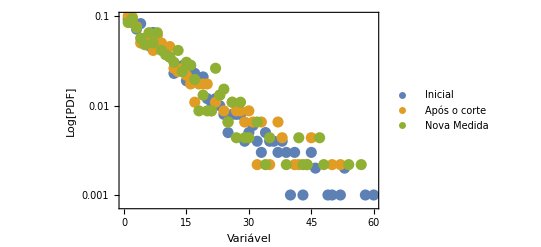

A fração do efeito nesse caso explicada por RTM é 0.74737139.

```mathematica
ListLogPlot[N[BinCounts[#,0.5]/Length[#]&/@{lispiloto,lispart,liswave}],PlotStyle->PointSize[0.02],PlotLegends->PointLegend[{"Inicial", "Após o corte","Nova Medida"}],Frame->True, FrameLabel->{Style["Variável",FontSize->18],Style["Log[PDF]",FontSize->18]}]
```

```mathematica
fefeito=fefeito=calcEfeito[lisRTM,4,0]/Abs[Mean[Join[liscontrole,lisintervencao]]-Mean[Join[liscontrolez6,lisintervencaoz6]]//N];
dist=Table[
L=4;
λ=0.209;
lispiloto=Table[RandomVariate[ExponentialDistribution[λ]],{84}];
lispart=Select[lispiloto,#>L&];
liswave=Table[RandomVariate[ExponentialDistribution[λ]],{Length[lispart]}];
L/(Mean[lispart]-Mean[lispiloto]),{10000}];
pvalue=Length[Select[dist,#<fefeito&]]/Length[dist]//N;
```

```mathematica
fefeito
```

0.747371

```mathematica
StringTemplate["A fração do efeito nesse caso explicada por RTM é `fracao`. Podemos através de uma simulação de Monte Carlo estimar a significância Estatísitca desse resultado em `pvalue`. Conclusão 
o efeito medido é maior que o esperado. "][<| "fracao"->fefeito,"pvalue"->pvalue|>]
```

A fração do efeito nesse caso explicada por RTM é 0.74737139. Podemos através de uma simulação de Monte Carlo estimar a significância Estatísitca desse resultado em 0.021. Conclusão 
o efeito medido é maior que o esperado.

```mathematica
fefeito=calcEfeito[lisRTM,4,0]/Abs[Mean[Join[liscontrole,lisintervencao]]-Mean[lisRTM]//N]
```

0.584771

```mathematica
fefeito=calcEfeito[lisRTM,4,0]
```

4.52315

```mathematica
Abs[Mean[Join[liscontrole,lisintervencao]]-Mean[Join[liscontrolez6,lisintervencaoz6]]]
```

6.05208

```mathematica
calcEfeito[lisRTM,4,0]
```

4.52315

```mathematica
1/2.5
```

0.4

```mathematica
frametext=Style[#,"FontSize"->14]&/@{"fração do efeito","PDF"};
gr1=SmoothHistogram[dist,Filling->Bottom,PlotRange->{{fefeito,1.8},All},Frame->True];
gr2=SmoothHistogram[dist,Filling->Bottom,PlotRange->{{0,fefeito},All},PlotStyle->Orange];
gr3=SmoothHistogram[dist,PlotRange->{All,All},PlotStyle->Orange,Frame->True,FrameLabel-> frametext];
Export[prefix<>"pvalue.pdf",Show[gr3,gr2,gr1]]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/pvalue.pdf

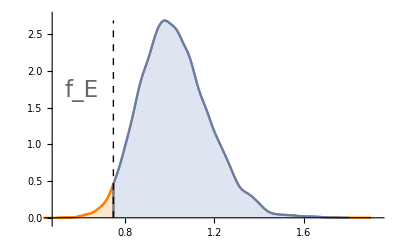

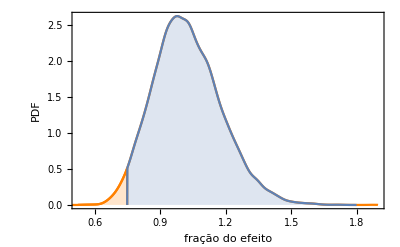

```mathematica
Show[gr3,gr2,gr1]
```

### Grupo Risco mais Restrito

```mathematica
bbariscorest=Select[bbarisco,#AUDITESC≥8 &&( #GRUPO=="C"|| #GRUPO=="I")&&#RECUSA==0 &&#RecusaIB6==0&];
```

```mathematica
(bbariscorest[All,"z6AUDITESC"]//Mean//N)
```

4.32911

```mathematica
(bbariscorest[All,"AUDITESC"]//Mean//N)
```

12.7342

```mathematica
(bbariscorest[All,"AUDITESC"]//Mean//N)-(bbariscorest[All,"z6AUDITESC"]//Mean//N)
```

8.40506

```mathematica
calcEfeito[lisRTM,8,0]
```

7.61034

```mathematica
7.61/8.40
```

0.905952

```mathematica
fefeito=calcEfeito[lisRTM,8,0]/Abs[(bbariscorest[All,"AUDITESC"]//Mean//N)-(bbariscorest[All,"z6AUDITESC"]//Mean//N)];
dist=Table[
L=8;
λ=0.209;
lispiloto=Table[RandomVariate[ExponentialDistribution[λ]],{84}];
lispart=Select[lispiloto,#>L&];
liswave=Table[RandomVariate[ExponentialDistribution[λ]],{Length[lispart]}];
L/(Mean[lispart]-Mean[lispiloto]),{10000}];
pvalue=Length[Select[dist,#<fefeito&]]/Length[dist]//N;
```

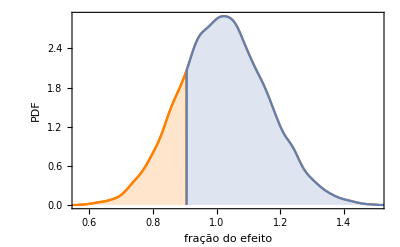

```mathematica
frametext=Style[#,"FontSize"->14]&/@{"fração do efeito","PDF"};
gr1=SmoothHistogram[dist,Filling->Bottom,PlotRange->{{fefeito,1.8},All},Frame->True];
gr2=SmoothHistogram[dist,Filling->Bottom,PlotRange->{{0,fefeito},All},PlotStyle->Orange];
gr3=SmoothHistogram[dist,PlotRange->{All,All},PlotStyle->Orange,Frame->True,FrameLabel-> frametext];
Show[gr3,gr2,gr1]
```

### Análise Linear

### Caso Paradigmático

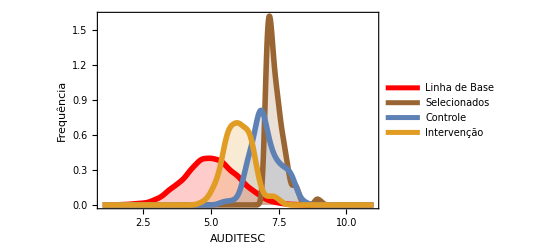

```mathematica
delay=5;
lisinit=Table[RandomVariate[NormalDistribution[delay,1]],{10000}];
lis2=Select[lisinit,#>delay+2&];
lis3=Table[RandomVariate[NormalDistribution[delay+2,0.5]],Floor[Length[lis2]/2]];
lis4=Table[RandomVariate[NormalDistribution[delay+1,0.5]],Floor[Length[lis2]/2]];
grpar=SmoothHistogram[{lisinit,lis2,lis3,lis4},PlotStyle-> {{Thickness[0.01],Red},{Thickness[0.01],Brown},{Thickness[0.01],RGBColor[0.368417,0.506779,0.709798]},{Thickness[0.01],RGBColor[0.880722,0.611041,0.142051]}},PlotLegends->LineLegend[{"Linha de Base","Selecionados",  "Controle","Intervenção"}],Axes->True,PlotRange->{{delay-4,delay+6},All},Filling->Bottom,Filling->Bottom,PlotStyle->{Thickness[0.01]},Frame->True, FrameLabel->{Style["AUDITESC",FontSize->18],Style["Frequência",FontSize->18]}]
```

```mathematica
Export[prefix<>"RTMdistpar.pdf",grpar]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/RTMdistpar.pdf

Thread::tdlen: Objects of unequal length in {5.59784,6.32146,6.43056,5.6351,6.50927,«41»,5.80143,5.71308,6.61662,5.12683,«52»} {«1»} cannot be combined.

Transpose::nmtx: The first two levels of {Log[{5.59784,6.32146,6.43056,5.6351,6.50927,«42»,5.71308,6.61662,5.12683,«52»} {«1»}],{«1»}} cannot be transposed.

ListPlot::lpn: {{{-0.172056,1.99205},{0.120943,1.95989},{-0.106823,1.9649},«46»,{-0.173787,2.09099},«52»},«1»} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {5.59784,6.32146,6.43056,5.6351,6.50927,«41»,5.80143,5.71308,6.61662,5.12683,«52»} {«1»} cannot be combined.

Transpose::nmtx: The first two levels of {Log[{5.59784,6.32146,6.43056,5.6351,6.50927,«42»,5.71308,6.61662,5.12683,«52»} {«1»}],{«1»}} cannot be transposed.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Set::shape: Lists {a2,b2} and LinearModelFit[Transpose[«1»],x,x][BestFitParameters] are not the same shape.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[{{{-0.172056,1.99205},{0.120943,1.95989},«47»,{-0.173787,2.09099},«52»},Transpose[«1»]},«4»,«11»→«1»],].

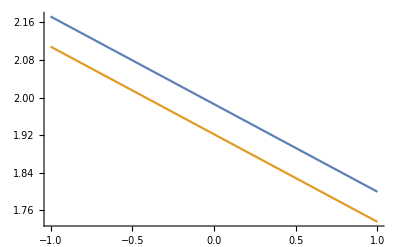
Show[ListPlot[{{{-0.172056,1.99205},{0.120943,1.95989},{-0.106823,1.9649},{-0.133565,2.01288},{0.0631748,1.9624},{0.0924168,2.00188},{-0.0481288,1.9748},{0.00583583,1.95761},{-0.0761816,1.98541},{-0.176141,2.05783},{0.0707177,1.99337},{-0.112656,2.0294},{-0.0539692,1.98629},{-0.0710845,1.97725},{-0.139808,2.04419},{-0.0452159,2.01124},{-0.0189785,1.96893},{0.00530045,2.03213},{-0.0538878,1.99079},{-0.0506595,2.06731},{-0.0158093,1.96766},{-0.0725269,2.00878},{-0.00474385,1.98885},{-0.137663,2.07352},{-0.116071,1.99095},{0.0845126,1.94635},{-0.0650386,1.97041},{0.0614918,2.01916},{-0.0765037,2.01003},{0.0180187,1.96824},{0.0146571,1.94827},{0.037472,1.94861},{-0.00428694,1.9568},{-0.0940578,2.01172},{-0.130839,1.97118},{-0.0351687,1.94709},{-0.163498,2.04168},{-0.149859,2.0585},{-0.0410778,2.04559},{-0.109983,2.0171},{-0.0113451,1.94848},{-0.0810791,1.96002},{-0.0397314,2.02257},{-0.0709262,2.08939},{-0.0320961,1.9533},{-0.113343,2.02873},{-0.0964975,2.05232},{-0.0526491,1.97384},{-0.151467,1.98955},{-0.173787,2.09099},{-0.0710408,1.95639},{-0.025825,2.01453},{-0.0995836,1.95828},{0.0652718,1.99741},{-0.141966,1.97277},{-0.0543475,1.99227},{-0.166405,1.96183},{-0.0511975,1.95225},{-0.0119934,1.98398},{0.127012,1.96047},{0.106964,1.94611},{0.0816823,1.9728},{-0.139264,1.98392},{0.017116,2.0302},{0.141546,1.98704},{-0.0459747,1.95402},{-0.251893,1.9527},{-0.0652765,1.98895},{0.00528518,1.95262},{-0.101179,2.02305},{-0.0434705,2.09231},{-0.010873,1.96527},{-0.0708533,1.95549},{-0.104758,2.03558},{-0.0657453,2.02791},{-0.0819531,1.97308},{0.0559096,2.01284},{-0.113031,1.95948},{0.111452,1.9718},{0.0245506,2.03077},{0.126255,1.95588},{-0.0195898,2.01879},{-0.0455912,2.01843},{-0.0967935,1.95672},{-0.0240804,1.95406},{-0.0776238,2.00022},{-0.208771,1.96038},{0.0559161,1.96097},{-0.0203916,1.9511},{0.0114188,1.97839},{-0.0481324,1.96905},{-0.0451531,1.97943},{-0.0717828,2.03742},{-0.257821,2.11497},{0.000147591,2.00008},{-0.0181102,2.0354},{-0.255454,2.10609},{0.0186436,1.99523},{-0.143221,2.00925},{-0.149451,2.06144},{0.0548614,1.97435},{-0.110799,1.96164}},Transpose[{Log[{5.59784,6.32146,6.43056,5.6351,6.50927,6.1016,6.08843,6.20348,5.97483,6.11702,5.99681,5.74755,6.45224,5.54045,6.46314,6.20566,5.90297,7.21049,6.14905,5.737,6.43468,6.67281,5.56605,6.79684,6.92619,5.71418,5.52487,6.08251,6.69362,6.42426,6.40789,5.51124,6.30906,6.19684,6.02316,6.37822,6.04834,5.72586,5.54322,5.55091,6.34956,6.5049,5.84283,6.55958,5.94713,6.30272,5.80143,5.71308,6.61662,5.12683,6.00581,5.60439,7.18912,6.00142,6.73285,5.25237,5.04202,5.98148,6.42584,7.47096,5.29526,5.24362,5.99058,5.49788,5.41122,5.69936,5.89506,6.30057,5.57942,5.04769,6.40046,5.74766,6.4592,6.23356,6.58628,5.63452,5.78791,6.23725,5.97546,5.80772,4.738,7.3609,5.75007,5.71652,5.91365,6.52909,5.84371,6.14547,6.07899,5.48941,6.63747,5.34371,5.92877,6.54,5.65894,5.5029,6.3597,6.04065,5.13178,5.46047,6.10462,6.38206} {0.142657,0.135968,0.142237,0.133928,0.14051,0.121847,0.140602,0.141308,0.138792,0.137069,0.13965,0.141042,0.127596,0.140444,0.139418,0.13786,0.134515,0.138409,0.138075,0.135999,0.139321,0.13412,0.136892,0.136596,0.140146,0.13765,0.140885,0.13533,0.129468,0.133596,0.130061,0.138913,0.135958,0.133315,0.139008,0.134735,0.141971,0.140861,0.141667,0.131991,0.138185,0.139348,0.140607,0.138949,0.130073,0.130359,0.126787,0.130254,0.138811,0.133966,0.112241,0.122346,0.140111,0.123385,0.126932,0.141647,0.128205,0.142342,0.129938,0.141904,0.14203,0.131631,0.13649,0.136911,0.132266,0.13521,0.135072,0.138036,0.112165,0.138065,0.139241,0.142749,0.134591,0.134011,0.13978,0.127795,0.138807,0.134833,0.123917,0.138351,0.137277,0.138757,0.133358,0.129446,0.135483,0.133167,0.14118,0.110334,0.136383,0.136452,0.14043,0.133591,0.136293,0.129655,0.131991,0.139973,0.138696,0.128041,0.139076,0.13763,0.124589,0.134819,0.138449}],{1.94731,1.99534,1.95026,2.01045,1.96248,2.10499,1.96182,1.95681,1.97478,1.98727,1.96861,1.9587,2.05889,1.96295,1.97028,1.98152,2.00608,1.97754,1.97996,1.99511,1.97097,2.00902,1.98856,1.99073,1.96507,1.98304,1.95981,2.00004,2.04432,2.01293,2.03975,1.97391,1.99541,2.01504,1.97323,2.00445,1.95213,1.95998,1.95428,2.02502,1.97916,1.97078,1.96179,1.97365,2.03966,2.03746,2.06525,2.03827,1.97464,2.01017,2.1871,2.1009,1.96532,2.09244,2.0641,1.95442,2.05413,1.94952,2.0407,1.9526,1.95172,2.02775,1.9915,1.98842,2.02294,2.00093,2.00195,1.98024,2.18779,1.98003,1.97155,1.94667,2.00551,2.00984,1.96769,2.05733,1.97467,2.00372,2.08814,1.97796,1.98575,1.97503,2.01472,2.0445,1.99891,2.01615,1.95772,2.20425,1.99229,1.99179,1.96305,2.01297,1.99295,2.04288,2.02502,1.9663,1.97547,2.05541,1.97273,1.98319,2.08274,2.00382,1.97725}}]},Frame→True,PlotStyle→PointSize→0.02,FrameLabel→{Log A^Antes,Log (A^Depois/A^Antes )},PlotStyle→{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0, 1, 0]},PlotLegends→PointLegend[Automatic,{Controle,Intervenção},LegendFunction→Frame,LegendLabel→Grupos,LegendMarkers→●]],-Graphics-]

```mathematica
grpoints=ListPlot[{Transpose[{Log[(lis3)/lis2[[1;;Length[lis3]]]],Log[lis2[[1;;Length[lis3]]]]}],Transpose[{Log[lis4/lis2[[Length[lis3]+1;;-1]]],Log[lis2[[Length[lis3]+1;;-1]]]
}]},Frame->True,PlotStyle->PointSize->0.02,FrameLabel->{Style["Log A^Antes",FontSize->14],Style["Log (A^Depois/A^Antes )",FontSize->14]},
PlotStyle->{RGBColor[0.368417,0.506779,0.709798],Green},PlotLegends->PointLegend[Automatic,{"Controle","Intervenção"},LegendFunction->"Frame",LegendLabel->Style["Grupos",Bold],LegendMarkers->●]];
{a1,b1}=LinearModelFit[Transpose[{Log[(lis3)/lis2[[1;;Length[lis3]]]],Log[lis2[[1;;Length[lis3]]]]}],x,x]["BestFitParameters"];
{a2,b2}=LinearModelFit[Transpose[{Log[lis4/lis2[[Length[lis3]+1;;-1]]],Log[lis2[[Length[lis3]+1;;-1]]]}],x,x]["BestFitParameters"];
grfunc=Plot[{a1+b1 x,a2-0.03+b1 x},{x,-1,1},PlotStyle-> {{Automatic},{Automatic},{Black,Dashed}}];
Show[grpoints,grfunc]
```

```mathematica
grfunc//FullForm
```

Graphics[List[List[List[],List[],List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Line[List[List[-1.,2.23234],List[-0.999387,2.23219],List[-0.998773,2.23204],List[-0.997546,2.23174],List[-0.995093,2.23114],List[-0.990186,2.22993],List[-0.980371,2.22753],List[-0.960743,2.22271],List[-0.918183,2.21228],List[-0.878444,2.20253],List[-0.839485,2.19298],List[-0.797223,2.18262],List[-0.757782,2.17294],List[-0.715038,2.16246],List[-0.673074,2.15217],List[-0.633931,2.14257],List[-0.591485,2.13217],List[-0.55186,2.12245],List[-0.513014,2.11292],List[-0.470866,2.10259],List[-0.431539,2.09294],List[-0.388909,2.08249],List[-0.347059,2.07223],List[-0.308029,2.06266],List[-0.265697,2.05228],List[-0.226185,2.04259],List[-0.183372,2.03209],List[-0.141338,2.02178],List[-0.102124,2.01217],List[-0.0596078,2.00174],List[-0.0199122,1.99201],List[0.0190039,1.98246],List[0.0612221,1.97211],List[0.10062,1.96245],List[0.14332,1.95198],List[0.18524,1.9417],List[0.22434,1.93211],List[0.266743,1.92171],List[0.306325,1.91201],List[0.345127,1.90249],List[0.387231,1.89217],List[0.426515,1.88254],List[0.469102,1.87209],List[0.508868,1.86234],List[0.547854,1.85278],List[0.590142,1.84241],List[0.629611,1.83273],List[0.672381,1.82225],List[0.714372,1.81195],List[0.753542,1.80234],List[0.796015,1.79193],List[0.835667,1.78221],List[0.874539,1.77267],List[0.916714,1.76233],List[0.956069,1.75268],List[0.956755,1.75251],List[0.957441,1.75234],List[0.958814,1.75201],List[0.96156,1.75133],List[0.967051,1.74999],List[0.978034,1.74729],List[0.978721,1.74713],List[0.979407,1.74696],List[0.98078,1.74662],List[0.983526,1.74595],List[0.989017,1.7446],List[0.989704,1.74443],List[0.99039,1.74426],List[0.991763,1.74393],List[0.994509,1.74325],List[0.995195,1.74309],List[0.995881,1.74292],List[0.997254,1.74258],List[0.997941,1.74241],List[0.998627,1.74225],List[0.999314,1.74208],List[1.,1.74191]]]],List[Directive[Opacity[1.],RGBColor[0.880722,0.611041,0.142051],AbsoluteThickness[1.6]],Line[List[List[-1.,2.12103],List[-0.999387,2.12088],List[-0.998773,2.12073],List[-0.997546,2.12043],List[-0.995093,2.11982],List[-0.990186,2.11862],List[-0.980371,2.11621],List[-0.960743,2.1114],List[-0.918183,2.10096],List[-0.878444,2.09122],List[-0.839485,2.08167],List[-0.797223,2.0713],List[-0.757782,2.06163],List[-0.715038,2.05115],List[-0.673074,2.04086],List[-0.633931,2.03126],List[-0.591485,2.02085],List[-0.55186,2.01114],List[-0.513014,2.00161],List[-0.470866,1.99127],List[-0.431539,1.98163],List[-0.388909,1.97118],List[-0.347059,1.96092],List[-0.308029,1.95134],List[-0.265697,1.94096],List[-0.226185,1.93128],List[-0.183372,1.92078],List[-0.141338,1.91047],List[-0.102124,1.90085],List[-0.0596078,1.89043],List[-0.0199122,1.88069],List[0.0190039,1.87115],List[0.0612221,1.8608],List[0.10062,1.85114],List[0.14332,1.84067],List[0.18524,1.83039],List[0.22434,1.8208],List[0.266743,1.8104],List[0.306325,1.8007],List[0.345127,1.79118],List[0.387231,1.78086],List[0.426515,1.77122],List[0.469102,1.76078],List[0.508868,1.75103],List[0.547854,1.74147],List[0.590142,1.7311],List[0.629611,1.72142],List[0.672381,1.71093],List[0.714372,1.70064],List[0.753542,1.69103],List[0.796015,1.68062],List[0.835667,1.67089],List[0.874539,1.66136],List[0.916714,1.65102],List[0.956069,1.64137],List[0.956755,1.6412],List[0.957441,1.64103],List[0.958814,1.64069],List[0.96156,1.64002],List[0.967051,1.63867],List[0.978034,1.63598],List[0.978721,1.63581],List[0.979407,1.63564],List[0.98078,1.63531],List[0.983526,1.63463],List[0.989017,1.63329],List[0.989704,1.63312],List[0.99039,1.63295],List[0.991763,1.63261],List[0.994509,1.63194],List[0.995195,1.63177],List[0.995881,1.6316],List[0.997254,1.63127],List[0.997941,1.6311],List[0.998627,1.63093],List[0.999314,1.63076],List[1.,1.63059]]]]]],List[Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,1.6]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None]]],Rule[PlotRange,List[List[-1,1],List[1.63059,2.23234]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[Ticks,List[Automatic,Automatic]]]]

```mathematica
Export[prefix<>"RTMpar.pdf",Show[grpoints,grfunc]]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/RTMpar.pdf

```mathematica
partlsd=Delete[Select[#,#RECUSAIB==0&&#RecusaIB12==0&]&/@(Delete[GroupBy[Select[dataset1,#RECUSA==0&],{#GRUPO}&],1]),1];
liscontrole=(Cases[Normal[partlsd[[1]][All,"AUDITESC"]],_Integer]//N);
lisintervencao=(Cases[Normal[partlsd[[2]][All,"AUDITESC"]],_Integer]//N);
liscontrole1=(Cases[Normal[partlsd[[1]][All,"z1AUDITESC"]],_Integer]//N);
lisintervencao1=(Cases[Normal[partlsd[[2]][All,"z1AUDITESC"]],_Integer]//N);
liscontrolez6=(Cases[Normal[partlsd[[1]][All,"z6AUDITESC"]],_Integer]//N);
lisintervencaoz6=(Cases[Normal[partlsd[[2]][All,"z6AUDITESC"]],_Integer]//N);
liscontrolez12=(Cases[Normal[partlsd[[1]][All,"z12AUDITESC"]],_Integer]//N);
lisintervencaoz12=(Cases[Normal[partlsd[[2]][All,"z12AUDITESC"]],_Integer]//N);
```

```mathematica
geralisAncova[liscontrole_,lisintervencao_,liscontrole2_,lisintervencao2_]:=Module[{lislogcontrole,lislogintervencao},
lislogcontrole=Select[Transpose@{Log[liscontrole],-Log[liscontrole]+Log[liscontrole2]},#[[1]]≠-∞&];
lislogintervencao=Select[Transpose@{Log[lisintervencao],-Log[lisintervencao]+Log[lisintervencao2]},#[[1]]≠-∞&];
Join[Prepend[#, 0]&/@lislogcontrole,Prepend[#, 1]&/@lislogintervencao]]
```

{0.857731,-0.218604,-0.769484}

{{-0.140028,1.85549},{-0.599395,0.162187},{-1.20054,-0.338432}}

| DF | SS | MS | F-Statistic | P-Value
treatment | 1 | 2.98058 | 2.98058 | 3.5983 | 0.060942
time | 1 | 10.4092 | 10.4092 | 12.5664 | 0.000616863
Error | 93 | 77.0347 | 0.82833 |  | 
Total | 95 | 90.4244 |  |  |

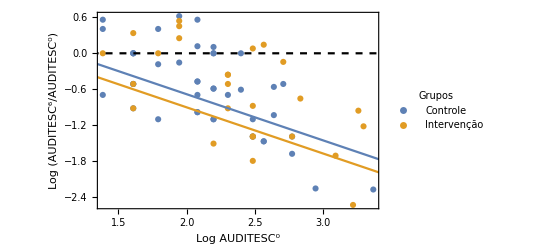

```mathematica
lisAncova=geralisAncova[liscontrole+1,lisintervencao+1,liscontrolez6+1,lisintervencaoz6+1];
lisintervencao2=lisintervencaoz6;
liscontrole2=liscontrolez6;
lislogcontrole=Select[Transpose@{Log[liscontrole],-Log[liscontrole]+Log[liscontrole2]},#[[1]]≠-∞&];
lislogintervencao=Select[Transpose@{Log[lisintervencao],-Log[lisintervencao]+Log[lisintervencao2]},#[[1]]≠-∞&];
grpoints=ListPlot[{lislogcontrole,lislogintervencao},Frame->True,PlotStyle->PointSize->0.02,FrameLabel->{Style["Log AUDITESC^0",FontSize->14],Style["Log (AUDITESC^6/AUDITESC^0)",FontSize->14]},PlotLegends->PointLegend[Automatic,{"Controle","Intervenção"},LegendFunction->"Frame",LegendLabel->Style["Grupos",Bold],LegendMarkers->●]];
lm=LinearModelFit[lisAncova,{treatment,time},{treatment,time}];
{α,β,γ}=lm["BestFitParameters"]
lm["ParameterConfidenceIntervals"]
lm["ANOVATable"]
grfunc=Plot[{α+γ x,α+β+γ x,0},{x,1.,3.5},PlotStyle-> {{Automatic},{Automatic},{Black,Dashed}}];
Show[grpoints,grfunc]
Export[prefix<>"RTMz6.pdf",Show[grpoints,grfunc]];
tabparam={
lm["BestFitParameters"],
lm["ParameterConfidenceIntervals"],lm["ParameterPValues"]};
tabparamTex=geraFitTabTex[tabparam,ToString/@lm["ParameterTable"][[1,1,2;;-1,1]]];
Export[prefix<>"tabparamRTMz6.tex",tabparamTex, "String"];
```

```mathematica
compilaTex[tabparamTex,prefix]
```

-Graphics-

{1.20717,-0.0220345,-1.01167}

{{0.199227,2.21512},{-0.406713,0.362644},{-1.44712,-0.576217}}

| DF | SS | MS | F-Statistic | P-Value
treatment | 1 | 0.967568 | 0.967568 | 1.14461 | 0.28745
time | 1 | 17.9926 | 17.9926 | 21.2847 | 0.0000126296
Error | 93 | 78.6155 | 0.845328 |  | 
Total | 95 | 97.5756 |  |  |

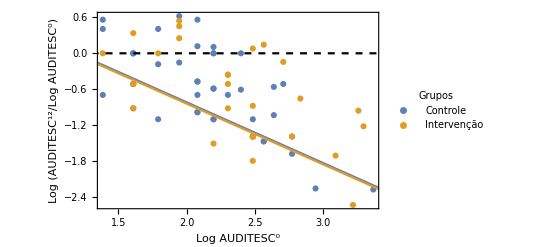

```mathematica
lisAncova=geralisAncova[liscontrole+1,lisintervencao+1,liscontrolez12+1,lisintervencaoz12+1];
lisintervencao2=lisintervencaoz12;
liscontrole2=liscontrolez12;
grpoints=ListPlot[{lislogcontrole,lislogintervencao},Frame->True,PlotStyle->PointSize->0.02,FrameLabel->{Style["Log AUDITESC^0",FontSize->14],Style["Log (AUDITESC^12/Log AUDITESC^0)",FontSize->14]},PlotLegends->PointLegend[Automatic,{"Controle","Intervenção"},LegendFunction->"Frame",LegendLabel->Style["Grupos",Bold],LegendMarkers->●]];
lm=LinearModelFit[lisAncova,{treatment,time},{treatment,time}];
{α,β,γ}=lm["BestFitParameters"]
lm["ParameterConfidenceIntervals"]
lm["ANOVATable"]
grfunc=Plot[{α+γ x,α+β+γ x,0},{x,1.,3.5},PlotStyle-> {{Automatic},{Automatic},{Black,Dashed}}];
Show[grpoints,grfunc]
Export[prefix<>"RTMz12.pdf",Show[grpoints,grfunc]];
tabparam={
lm["BestFitParameters"],
lm["ParameterConfidenceIntervals"],lm["ParameterPValues"]};
tabparamTex=geraFitTabTex[tabparam,ToString/@lm["ParameterTable"][[1,1,2;;-1,1]]];
Export[prefix<>"tabparamRTMz12.tex",tabparamTex, "String"];
```

```mathematica
compilaTex[tabparamTex,prefix]
```

-Graphics-

Simulação do Modelo pqq

Vamos inicialmente definir as variáveis.

```mathematica
lisRTM=Cases[Normal[dataset1[All,"AUDITESC"]],_Integer]//N;
partlsd=Delete[Select[#,#RECUSAIB==0&&#RecusaIB12==0&]&/@(Delete[GroupBy[Select[dataset1,#RECUSA==0&],{#GRUPO}&],1]),1];
liscontrole=(Cases[Normal[partlsd[[1]][All,"AUDITESC"]],_Integer]//N);
lisintervencao=(Cases[Normal[partlsd[[2]][All,"AUDITESC"]],_Integer]//N);
liscontrole1=(Cases[Normal[partlsd[[1]][All,"z1AUDITESC"]],_Integer]//N);
lisintervencao1=(Cases[Normal[partlsd[[2]][All,"z1AUDITESC"]],_Integer]//N);
liscontrolez6=(Cases[Normal[partlsd[[1]][All,"z6AUDITESC"]],_Integer]//N);
lisintervencaoz6=(Cases[Normal[partlsd[[2]][All,"z6AUDITESC"]],_Integer]//N);
liscontrolez12=(Cases[Normal[partlsd[[1]][All,"z12AUDITESC"]],_Integer]//N);
lisintervencaoz12=(Cases[Normal[partlsd[[2]][All,"z12AUDITESC"]],_Integer]//N);
size=Length[Join[liscontrole,lisintervencao]];
size0=Length[lisRTM];
```

### Geração de um Modelo para o Grupo Risco

A idéia é considerar todos com Audit alto e parte dos com 4<=AUDITESC<8. Empiricamente a fração mais adequada foi de 40%.

```mathematica
lisRTM4=Select[lisRTM,#>=4&];
lisRTM8=Select[lisRTM,#>=8&];
temp=Select[lisRTM,#>=4&&#<8&];
lisRTM45=Join[RandomSample[temp,Floor[Length[temp]/2.5]],lisRTM8];
```

```mathematica
scale=N[Floor[10*(HistogramList[lisRTM][[2,1]])/Length[lisRTM]]/10];
max=1.3;
listicksy=Table[{max*i/5,scale*i/5},{i,0,5}];
```

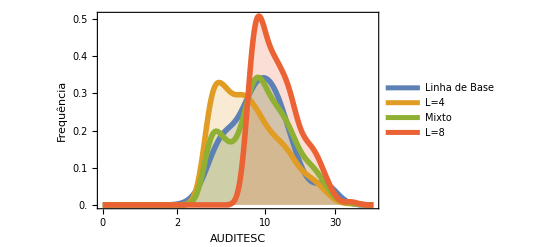

```mathematica
gr2=SmoothHistogram[{Log[Join[liscontrole,lisintervencao]+1],Log[lisRTM4+1],Log[lisRTM45+1],Log[lisRTM8+1]},PlotLegends->LineLegend[{"Linha de Base","L=4",  "Mixto","L=8"}],Axes->True,PlotRange->{{0,4},All},Filling->Bottom,Filling->Bottom,PlotStyle->{Thickness[0.01]},Frame->True, FrameLabel->{Style["AUDITESC",FontSize->18],Style["Frequência",FontSize->18]},FrameTicks->{listicksy,{{0,{Log[1+1],1},{Log[3],2},{Log[6],5},{Log[11],10},{Log[21],20},{Log[31],30},{Log[51],50}},None}}]
```

```mathematica
Export[prefix<>"gerarlb.pdf",Show[gr2]]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/gerarlb.pdf

### Determinação dos parâmetros ótimos p e q

Para determinar p e q ótimos. Calculamos a soma cumulativa do Log(f_i+1).

φ_f(k)=∑_(i=0)^k Log(f_i+1)

Essa quantidade foi utilizada pois é finita se f_i=0 e diminui o efeito de concentração das frequências nas proximidades de 0. Para comparar duas distribuições quaisquer usamos uma versão discreta da Métrica de Kolmogorov:

ϵ(f,g)=∑_(k=0)^M |φ_f(k)-φ_g(k)|

onde M é o valor máximo entre os valores presentes em f e em g.

Para determinar o modelo ideal rodamos um programa em python e geramos várias comparações entre as distribuições obtidas por simulação e as distribuições experimentais e determinamos os parâmetros mais próximos.

```mathematica
size0=Length[lisRTM];
size=Length[Join[liscontrole,lisintervencao]];

listDist=ParallelTable[Print[p,",",q];Sum[
simul=Table[Steps[p,q,0,150],{size0}];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
(* Print[sizelocal,",",size,",",Length[simul2]]; *)
simul3=Steps[p,q,#,25]&/@simul2;
       simul4=Steps[p,q,#,25]& /@simul3;
{p,q,compara[simul,lisRTM]},{j,1,100}]/100,{p,0.6,0.99,0.01},{q,0.50,0.65,0.005}];
distListPythonTri=Flatten[listDist,1];
```

0.6,0.5

0.65,0.5

0.7,0.5

0.75,0.5

0.7,0.505

0.75,0.505

0.6,0.505

0.65,0.505

0.7,0.51

0.75,0.51

0.6,0.51

0.65,0.51

0.7,0.515

0.75,0.515

0.6,0.515

0.65,0.515

0.7,0.52

0.75,0.52

0.6,0.52

0.65,0.52

0.7,0.525

0.75,0.525

0.65,0.525

0.6,0.525

0.7,0.53

0.75,0.53

0.65,0.53

0.6,0.53

0.7,0.535

0.75,0.535

0.65,0.535

0.6,0.535

0.7,0.54

0.75,0.54

0.65,0.54

0.6,0.54

0.7,0.545

0.75,0.545

0.65,0.545

0.6,0.545

0.7,0.55

0.75,0.55

0.65,0.55

0.6,0.55

0.7,0.555

0.75,0.555

0.65,0.555

0.6,0.555

0.7,0.56

0.75,0.56

0.65,0.56

0.6,0.56

0.7,0.565

0.75,0.565

0.65,0.565

0.6,0.565

0.7,0.57

0.75,0.57

0.65,0.57

0.6,0.57

0.7,0.575

0.75,0.575

0.65,0.575

0.6,0.575

0.7,0.58

0.75,0.58

0.65,0.58

0.6,0.58

0.7,0.585

0.75,0.585

0.65,0.585

0.6,0.585

0.7,0.59

0.75,0.59

0.65,0.59

0.6,0.59

0.7,0.595

0.75,0.595

0.65,0.595

0.6,0.595

0.7,0.6

0.75,0.6

0.65,0.6

0.6,0.6

0.7,0.605

0.75,0.605

0.6,0.605

0.65,0.605

0.7,0.61

0.75,0.61

0.65,0.61

0.6,0.61

0.7,0.615

0.75,0.615

0.65,0.615

0.6,0.615

0.7,0.62

0.75,0.62

0.65,0.62

0.6,0.62

0.7,0.625

0.75,0.625

0.65,0.625

0.6,0.625

0.7,0.63

0.75,0.63

0.65,0.63

0.6,0.63

0.7,0.635

0.75,0.635

0.65,0.635

0.6,0.635

0.7,0.64

0.75,0.64

0.65,0.64

0.6,0.64

0.7,0.645

0.75,0.645

0.65,0.645

0.6,0.645

0.7,0.65

0.75,0.65

0.65,0.65

0.6,0.65

0.71,0.5

0.76,0.5

0.66,0.5

0.61,0.5

0.71,0.505

0.76,0.505

0.66,0.505

0.61,0.505

0.71,0.51

0.76,0.51

0.66,0.51

0.61,0.51

0.71,0.515

0.76,0.515

0.66,0.515

0.61,0.515

0.71,0.52

0.76,0.52

0.66,0.52

0.71,0.525

0.61,0.52

0.76,0.525

0.66,0.525

0.71,0.53

0.61,0.525

0.76,0.53

0.66,0.53

0.71,0.535

0.61,0.53

0.76,0.535

0.66,0.535

0.71,0.54

0.61,0.535

0.76,0.54

0.66,0.54

0.71,0.545

0.61,0.54

0.76,0.545

0.66,0.545

0.71,0.55

0.61,0.545

0.76,0.55

0.66,0.55

0.71,0.555

0.61,0.55

0.76,0.555

0.66,0.555

0.71,0.56

0.61,0.555

0.76,0.56

0.66,0.56

0.71,0.565

0.61,0.56

0.76,0.565

0.66,0.565

0.71,0.57

0.61,0.565

0.76,0.57

0.66,0.57

0.71,0.575

0.61,0.57

0.76,0.575

0.66,0.575

0.71,0.58

0.61,0.575

0.76,0.58

0.66,0.58

0.71,0.585

0.61,0.58

0.76,0.585

0.66,0.585

0.71,0.59

0.61,0.585

0.76,0.59

0.66,0.59

0.71,0.595

0.61,0.59

0.76,0.595

0.66,0.595

0.71,0.6

0.76,0.6

0.61,0.595

0.66,0.6

0.71,0.605

0.76,0.605

0.61,0.6

0.66,0.605

0.71,0.61

0.76,0.61

0.61,0.605

0.66,0.61

0.71,0.615

0.76,0.615

0.61,0.61

0.66,0.615

0.71,0.62

0.76,0.62

0.61,0.615

0.71,0.625

0.66,0.62

0.76,0.625

0.61,0.62

0.71,0.63

0.66,0.625

0.76,0.63

0.61,0.625

0.71,0.635

0.66,0.63

0.76,0.635

0.61,0.63

0.71,0.64

0.66,0.635

0.76,0.64

0.61,0.635

0.71,0.645

0.66,0.64

0.76,0.645

0.61,0.64

0.71,0.65

0.66,0.645

0.76,0.65

0.61,0.645

0.72,0.5

0.66,0.65

0.77,0.5

0.61,0.65

0.72,0.505

0.67,0.5

0.77,0.505

0.62,0.5

0.72,0.51

0.67,0.505

0.77,0.51

0.62,0.505

0.72,0.515

0.67,0.51

0.77,0.515

0.62,0.51

0.72,0.52

0.67,0.515

0.77,0.52

0.62,0.515

0.67,0.52

0.72,0.525

0.77,0.525

0.62,0.52

0.72,0.53

0.67,0.525

0.77,0.53

0.62,0.525

0.72,0.535

0.67,0.53

0.77,0.535

0.62,0.53

0.72,0.54

0.67,0.535

0.77,0.54

0.62,0.535

0.72,0.545

0.67,0.54

0.77,0.545

0.72,0.55

0.62,0.54

0.67,0.545

0.77,0.55

0.72,0.555

0.62,0.545

0.67,0.55

0.77,0.555

0.72,0.56

0.62,0.55

0.67,0.555

0.77,0.56

0.72,0.565

0.62,0.555

0.67,0.56

0.77,0.565

0.72,0.57

0.62,0.56

0.67,0.565

0.77,0.57

0.72,0.575

0.62,0.565

0.67,0.57

0.77,0.575

0.72,0.58

0.62,0.57

0.67,0.575

0.77,0.58

0.72,0.585

0.62,0.575

0.67,0.58

0.77,0.585

0.72,0.59

0.62,0.58

0.67,0.585

0.77,0.59

0.72,0.595

0.62,0.585

0.67,0.59

0.77,0.595

0.72,0.6

0.62,0.59

0.67,0.595

0.77,0.6

0.72,0.605

0.62,0.595

0.67,0.6

0.77,0.605

0.72,0.61

0.62,0.6

0.67,0.605

0.77,0.61

0.72,0.615

0.62,0.605

0.67,0.61

0.77,0.615

0.72,0.62

0.62,0.61

0.67,0.615

0.77,0.62

0.72,0.625

0.62,0.615

0.67,0.62

0.77,0.625

0.72,0.63

0.62,0.62

0.67,0.625

0.77,0.63

0.72,0.635

0.77,0.635

0.62,0.625

0.67,0.63

0.72,0.64

0.77,0.64

0.67,0.635

0.62,0.63

0.72,0.645

0.77,0.645

0.67,0.64

0.62,0.635

0.72,0.65

0.77,0.65

0.67,0.645

0.62,0.64

0.73,0.5

0.78,0.5

0.67,0.65

0.62,0.645

0.73,0.505

0.78,0.505

0.68,0.5

0.62,0.65

0.73,0.51

0.78,0.51

0.68,0.505

0.63,0.5

0.73,0.515

0.78,0.515

0.68,0.51

0.63,0.505

0.73,0.52

0.78,0.52

0.68,0.515

0.63,0.51

0.73,0.525

0.78,0.525

0.68,0.52

0.63,0.515

0.73,0.53

0.78,0.53

0.68,0.525

0.63,0.52

0.73,0.535

0.78,0.535

0.68,0.53

0.63,0.525

0.73,0.54

0.78,0.54

0.68,0.535

0.63,0.53

0.73,0.545

0.78,0.545

0.68,0.54

0.63,0.535

0.73,0.55

0.78,0.55

0.68,0.545

0.73,0.555

0.63,0.54

0.78,0.555

0.68,0.55

0.73,0.56

0.63,0.545

0.78,0.56

0.68,0.555

0.73,0.565

0.63,0.55

0.78,0.565

0.68,0.56

0.73,0.57

0.63,0.555

0.78,0.57

0.68,0.565

0.73,0.575

0.63,0.56

0.78,0.575

0.68,0.57

0.73,0.58

0.63,0.565

0.78,0.58

0.68,0.575

0.73,0.585

0.63,0.57

0.78,0.585

0.68,0.58

0.73,0.59

0.63,0.575

0.78,0.59

0.68,0.585

0.73,0.595

0.63,0.58

0.78,0.595

0.73,0.6

0.68,0.59

0.63,0.585

0.78,0.6

0.73,0.605

0.68,0.595

0.63,0.59

0.78,0.605

0.73,0.61

0.68,0.6

0.63,0.595

0.78,0.61

0.73,0.615

0.68,0.605

0.63,0.6

0.78,0.615

0.73,0.62

0.68,0.61

0.63,0.605

0.78,0.62

0.73,0.625

0.68,0.615

0.63,0.61

0.78,0.625

0.73,0.63

0.68,0.62

0.63,0.615

0.78,0.63

0.73,0.635

0.68,0.625

0.63,0.62

0.78,0.635

0.73,0.64

0.68,0.63

0.63,0.625

0.78,0.64

0.73,0.645

0.68,0.635

0.63,0.63

0.78,0.645

0.73,0.65

0.68,0.64

0.78,0.65

0.63,0.635

0.74,0.5

0.68,0.645

0.79,0.5

0.63,0.64

0.74,0.505

0.68,0.65

0.79,0.505

0.63,0.645

0.74,0.51

0.69,0.5

0.79,0.51

0.63,0.65

0.74,0.515

0.69,0.505

0.79,0.515

0.64,0.5

0.74,0.52

0.69,0.51

0.79,0.52

0.64,0.505

0.74,0.525

0.69,0.515

0.79,0.525

0.64,0.51

0.74,0.53

0.69,0.52

0.79,0.53

0.64,0.515

0.74,0.535

0.69,0.525

0.79,0.535

0.64,0.52

0.74,0.54

0.69,0.53

0.79,0.54

0.64,0.525

0.74,0.545

0.69,0.535

0.79,0.545

0.64,0.53

0.74,0.55

0.69,0.54

0.79,0.55

0.64,0.535

0.74,0.555

0.69,0.545

0.79,0.555

0.74,0.56

0.64,0.54

0.69,0.55

0.79,0.56

0.74,0.565

0.64,0.545

0.69,0.555

0.79,0.565

0.74,0.57

0.64,0.55

0.69,0.56

0.79,0.57

0.74,0.575

0.64,0.555

0.69,0.565

0.79,0.575

0.74,0.58

0.64,0.56

0.69,0.57

0.79,0.58

0.74,0.585

0.64,0.565

0.69,0.575

0.79,0.585

0.74,0.59

0.64,0.57

0.69,0.58

0.79,0.59

0.74,0.595

0.64,0.575

0.69,0.585

0.79,0.595

0.74,0.6

0.64,0.58

0.69,0.59

0.79,0.6

0.74,0.605

0.64,0.585

0.69,0.595

0.79,0.605

0.74,0.61

0.64,0.59

0.69,0.6

0.79,0.61

0.74,0.615

0.64,0.595

0.69,0.605

0.79,0.615

0.74,0.62

0.64,0.6

0.69,0.61

0.79,0.62

0.74,0.625

0.64,0.605

0.69,0.615

0.79,0.625

0.74,0.63

0.64,0.61

0.69,0.62

0.79,0.63

0.74,0.635

0.64,0.615

0.69,0.625

0.79,0.635

0.74,0.64

0.64,0.62

0.69,0.63

0.79,0.64

0.74,0.645

0.64,0.625

0.69,0.635

0.79,0.645

0.74,0.65

0.64,0.63

0.69,0.64

0.8,0.5

0.79,0.65

0.69,0.645

0.64,0.635

0.85,0.5

0.8,0.505

0.69,0.65

0.64,0.64

0.85,0.505

0.8,0.51

0.9,0.5

0.64,0.645

0.85,0.51

0.8,0.515

0.9,0.505

0.64,0.65

0.85,0.515

0.8,0.52

0.9,0.51

0.95,0.5

0.85,0.52

0.8,0.525

0.9,0.515

0.95,0.505

0.85,0.525

0.8,0.53

0.9,0.52

0.95,0.51

0.85,0.53

0.8,0.535

0.9,0.525

0.95,0.515

0.85,0.535

0.8,0.54

0.9,0.53

0.95,0.52

0.85,0.54

0.8,0.545

0.9,0.535

0.95,0.525

0.8,0.55

0.85,0.545

0.9,0.54

0.8,0.555

0.95,0.53

0.85,0.55

0.9,0.545

0.8,0.56

0.85,0.555

0.95,0.535

0.9,0.55

0.8,0.565

0.85,0.56

0.95,0.54

0.9,0.555

0.8,0.57

0.85,0.565

0.95,0.545

0.9,0.56

0.8,0.575

0.85,0.57

0.95,0.55

0.9,0.565

0.8,0.58

0.85,0.575

0.95,0.555

0.9,0.57

0.8,0.585

0.85,0.58

0.95,0.56

0.9,0.575

0.8,0.59

0.85,0.585

0.95,0.565

0.9,0.58

0.8,0.595

0.85,0.59

0.95,0.57

0.9,0.585

0.8,0.6

0.85,0.595

0.95,0.575

0.9,0.59

0.8,0.605

0.85,0.6

0.95,0.58

0.9,0.595

0.8,0.61

0.85,0.605

0.95,0.585

0.9,0.6

0.8,0.615

0.85,0.61

0.95,0.59

0.9,0.605

0.8,0.62

0.85,0.615

0.95,0.595

0.9,0.61

0.8,0.625

0.85,0.62

0.95,0.6

0.9,0.615

0.8,0.63

0.85,0.625

0.95,0.605

0.9,0.62

0.8,0.635

0.85,0.63

0.95,0.61

0.9,0.625

0.8,0.64

0.85,0.635

0.95,0.615

0.9,0.63

0.8,0.645

0.85,0.64

0.95,0.62

0.9,0.635

0.8,0.65

0.85,0.645

0.95,0.625

0.9,0.64

0.81,0.5

0.85,0.65

0.95,0.63

0.9,0.645

0.86,0.5

0.81,0.505

0.95,0.635

0.9,0.65

0.86,0.505

0.81,0.51

0.95,0.64

0.91,0.5

0.95,0.645

0.86,0.51

0.81,0.515

0.91,0.505

0.95,0.65

0.86,0.515

0.81,0.52

0.91,0.51

0.96,0.5

0.86,0.52

0.81,0.525

0.91,0.515

0.96,0.505

0.86,0.525

0.81,0.53

0.91,0.52

0.96,0.51

0.86,0.53

0.81,0.535

0.91,0.525

0.96,0.515

0.86,0.535

0.81,0.54

0.91,0.53

0.96,0.52

0.86,0.54

0.81,0.545

0.91,0.535

0.96,0.525

0.86,0.545

0.81,0.55

0.91,0.54

0.96,0.53

0.86,0.55

0.81,0.555

0.91,0.545

0.96,0.535

0.86,0.555

0.81,0.56

0.91,0.55

0.96,0.54

0.86,0.56

0.81,0.565

0.91,0.555

0.96,0.545

0.86,0.565

0.81,0.57

0.91,0.56

0.96,0.55

0.86,0.57

0.81,0.575

0.91,0.565

0.86,0.575

0.96,0.555

0.81,0.58

0.91,0.57

0.86,0.58

0.81,0.585

0.96,0.56

0.91,0.575

0.86,0.585

0.81,0.59

0.96,0.565

0.91,0.58

0.86,0.59

0.81,0.595

0.96,0.57

0.91,0.585

0.86,0.595

0.81,0.6

0.96,0.575

0.91,0.59

0.86,0.6

0.81,0.605

0.96,0.58

0.91,0.595

0.86,0.605

0.81,0.61

0.96,0.585

0.91,0.6

0.86,0.61

0.81,0.615

0.96,0.59

0.91,0.605

0.86,0.615

0.81,0.62

0.91,0.61

0.96,0.595

0.86,0.62

0.81,0.625

0.91,0.615

0.96,0.6

0.86,0.625

0.91,0.62

0.96,0.605

0.81,0.63

0.91,0.625

0.86,0.63

0.96,0.61

0.81,0.635

0.91,0.63

0.86,0.635

0.96,0.615

0.81,0.64

0.91,0.635

0.86,0.64

0.96,0.62

0.81,0.645

0.91,0.64

0.86,0.645

0.96,0.625

0.81,0.65

0.91,0.645

0.86,0.65

0.96,0.63

0.82,0.5

0.91,0.65

0.87,0.5

0.96,0.635

0.82,0.505

0.92,0.5

0.96,0.64

0.87,0.505

0.82,0.51

0.92,0.505

0.96,0.645

0.87,0.51

0.82,0.515

0.96,0.65

0.92,0.51

0.87,0.515

0.82,0.52

0.97,0.5

0.92,0.515

0.87,0.52

0.82,0.525

0.97,0.505

0.92,0.52

0.87,0.525

0.82,0.53

0.97,0.51

0.92,0.525

0.87,0.53

0.82,0.535

0.97,0.515

0.92,0.53

0.87,0.535

0.82,0.54

0.97,0.52

0.92,0.535

0.87,0.54

0.82,0.545

0.92,0.54

0.97,0.525

0.87,0.545

0.82,0.55

0.92,0.545

0.97,0.53

0.87,0.55

0.82,0.555

0.92,0.55

0.97,0.535

0.87,0.555

0.82,0.56

0.92,0.555

0.97,0.54

0.87,0.56

0.82,0.565

0.92,0.56

0.97,0.545

0.87,0.565

0.82,0.57

0.92,0.565

0.97,0.55

0.87,0.57

0.82,0.575

0.92,0.57

0.97,0.555

0.87,0.575

0.82,0.58

0.92,0.575

0.97,0.56

0.87,0.58

0.82,0.585

0.92,0.58

0.97,0.565

0.87,0.585

0.82,0.59

0.92,0.585

0.97,0.57

0.87,0.59

0.82,0.595

0.92,0.59

0.97,0.575

0.87,0.595

0.82,0.6

0.92,0.595

0.97,0.58

0.87,0.6

0.82,0.605

0.92,0.6

0.97,0.585

0.87,0.605

0.82,0.61

0.92,0.605

0.97,0.59

0.87,0.61

0.82,0.615

0.92,0.61

0.97,0.595

0.87,0.615

0.82,0.62

0.92,0.615

0.97,0.6

0.87,0.62

0.82,0.625

0.92,0.62

0.97,0.605

0.87,0.625

0.82,0.63

0.92,0.625

0.97,0.61

0.87,0.63

0.82,0.635

0.92,0.63

0.97,0.615

0.87,0.635

0.82,0.64

0.92,0.635

0.97,0.62

0.87,0.64

0.82,0.645

0.92,0.64

0.97,0.625

0.87,0.645

0.92,0.645

0.82,0.65

0.97,0.63

0.87,0.65

0.92,0.65

0.83,0.5

0.97,0.635

0.88,0.5

0.93,0.5

0.83,0.505

0.97,0.64

0.88,0.505

0.93,0.505

0.83,0.51

0.97,0.645

0.88,0.51

0.93,0.51

0.97,0.65

0.83,0.515

0.88,0.515

0.93,0.515

0.98,0.5

0.83,0.52

0.88,0.52

0.93,0.52

0.98,0.505

0.83,0.525

0.88,0.525

0.93,0.525

0.98,0.51

0.83,0.53

0.88,0.53

0.93,0.53

0.98,0.515

0.83,0.535

0.88,0.535

0.93,0.535

0.83,0.54

0.98,0.52

0.88,0.54

0.93,0.54

0.83,0.545

0.98,0.525

0.93,0.545

0.88,0.545

0.83,0.55

0.98,0.53

0.93,0.55

0.88,0.55

0.83,0.555

0.98,0.535

0.93,0.555

0.88,0.555

0.83,0.56

0.98,0.54

0.93,0.56

0.88,0.56

0.83,0.565

0.98,0.545

0.93,0.565

0.88,0.565

0.83,0.57

0.98,0.55

0.93,0.57

0.88,0.57

0.83,0.575

0.98,0.555

0.93,0.575

0.88,0.575

0.83,0.58

0.98,0.56

0.93,0.58

0.88,0.58

0.83,0.585

0.98,0.565

0.93,0.585

0.88,0.585

0.83,0.59

0.98,0.57

0.93,0.59

0.88,0.59

0.83,0.595

0.98,0.575

0.93,0.595

0.88,0.595

0.83,0.6

0.98,0.58

0.93,0.6

0.88,0.6

0.83,0.605

0.98,0.585

0.93,0.605

0.88,0.605

0.98,0.59

0.83,0.61

0.93,0.61

0.88,0.61

0.98,0.595

0.83,0.615

0.93,0.615

0.98,0.6

0.88,0.615

0.83,0.62

0.93,0.62

0.98,0.605

0.88,0.62

0.83,0.625

0.93,0.625

0.98,0.61

0.88,0.625

0.83,0.63

0.93,0.63

0.98,0.615

0.88,0.63

0.83,0.635

0.93,0.635

0.98,0.62

0.88,0.635

0.83,0.64

0.93,0.64

0.98,0.625

0.88,0.64

0.83,0.645

0.93,0.645

0.98,0.63

0.88,0.645

0.83,0.65

0.93,0.65

0.98,0.635

0.88,0.65

0.84,0.5

0.94,0.5

0.98,0.64

0.89,0.5

0.84,0.505

0.94,0.505

0.98,0.645

0.89,0.505

0.84,0.51

0.94,0.51

0.98,0.65

0.89,0.51

0.84,0.515

0.94,0.515

0.99,0.5

0.89,0.515

0.94,0.52

0.84,0.52

0.99,0.505

0.89,0.52

0.94,0.525

0.84,0.525

0.99,0.51

0.89,0.525

0.94,0.53

0.84,0.53

0.99,0.515

0.89,0.53

0.94,0.535

0.84,0.535

0.99,0.52

0.89,0.535

0.94,0.54

0.84,0.54

0.99,0.525

0.89,0.54

0.94,0.545

0.84,0.545

0.99,0.53

0.89,0.545

0.94,0.55

0.84,0.55

0.99,0.535

0.89,0.55

0.94,0.555

0.84,0.555

0.99,0.54

0.89,0.555

0.94,0.56

0.84,0.56

0.99,0.545

0.89,0.56

0.94,0.565

0.84,0.565

0.99,0.55

0.89,0.565

0.99,0.555

0.94,0.57

0.84,0.57

0.89,0.57

0.94,0.575

0.99,0.56

0.84,0.575

0.89,0.575

0.99,0.565

0.94,0.58

0.84,0.58

0.89,0.58

0.99,0.57

0.94,0.585

0.84,0.585

0.89,0.585

0.99,0.575

0.94,0.59

0.84,0.59

0.99,0.58

0.89,0.59

0.94,0.595

0.84,0.595

0.99,0.585

0.89,0.595

0.94,0.6

0.84,0.6

0.99,0.59

0.89,0.6

0.94,0.605

0.84,0.605

0.99,0.595

0.89,0.605

0.94,0.61

0.84,0.61

0.99,0.6

0.94,0.615

0.89,0.61

0.84,0.615

0.99,0.605

0.94,0.62

0.89,0.615

0.84,0.62

0.99,0.61

0.94,0.625

0.89,0.62

0.84,0.625

0.99,0.615

0.94,0.63

0.89,0.625

0.99,0.62

0.84,0.63

0.94,0.635

0.89,0.63

0.99,0.625

0.84,0.635

0.94,0.64

0.89,0.635

0.99,0.63

0.84,0.64

0.94,0.645

0.89,0.64

0.99,0.635

0.84,0.645

0.94,0.65

0.89,0.645

0.99,0.64

0.84,0.65

0.89,0.65

0.99,0.645

0.99,0.65

```mathematica
distListPythonTri=Flatten[listDist,1];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
```

{0.92,0.535}

```mathematica
?Legend*
```

LegendLayout is an option for legends that specifies how to format the legend content.

```mathematica
?PlotLegends
```

PlotLegends is an option for plot functions that specifies what legends to use.

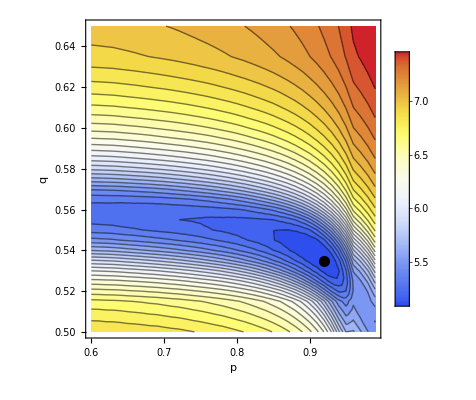

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"p","q"};
lispoints=distListPythonTri/.{x_,y_,z_}->{x,y};
lisfilt=Flatten[MeanFilter[Partition[distListPythonTri,31]/.{x_,y_,z_}->Log[z],3]];
point=First[MinimalBy[Table[Append[lispoints[[i]],lisfilt[[i]]],{i,1,Length[lispoints]}],Last]/.{x_,y_,z_}->{x,y}];
gr1=ListContourPlot[Table[Append[lispoints[[i]],lisfilt[[i]]],{i,1,Length[lispoints]}],Contours->30,ColorFunction->ColorData["TemperatureMap"],Epilog->{PointSize[0.02],Point[point]},FrameLabel->frametext,PlotLegends->Automatic]
```

```mathematica
Export[prefix<>"erro2d.pdf",gr1]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/erro2d.pdf

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"p","q","  ℰ"};
gr1=ListPlot3D[Table[Append[lispoints[[i]],lisfilt[[i]]],{i,1,Length[lispoints]}],InterpolationOrder->3,ColorFunction->"Temperature",PlotRange->{{0.5,0.95},Automatic,Automatic},MeshFunctions->{#3&,#1&,#2&},Mesh->{30,10,10},MeshStyle->{None,Automatic,Automatic},MeshShading->{{Directive[{EdgeForm[],#}]&/@Table[ColorData["TemperatureMap"][shade],{shade,0,2,0.05}]}},AxesLabel->frametext,PlotLegends->Automatic]


Export[prefix<>"erro3d.pdf",Show[gr1]]
```

-Graphics3D-

/Users/neylemke/Luisa/BancodeDadosDoutorado/erro3d.pdf

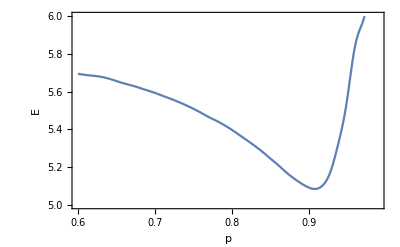

/Users/neylemke/Luisa/BancodeDadosDoutorado/erro1d.pdf

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"p"," E"};
gr1=ListPlot[Select[Table[Append[lispoints[[i]],lisfilt[[i]]],{i,1,Length[lispoints]}],#[[2]]==0.54&]/.{x_,y_,z_}->{x,z},Frame->True,FrameLabel->frametext,Joined->True,InterpolationOrder->5,PlotRange->{Automatic,{5,6}}]
Export[prefix<>"erro1d.pdf",Show[gr1]]
```

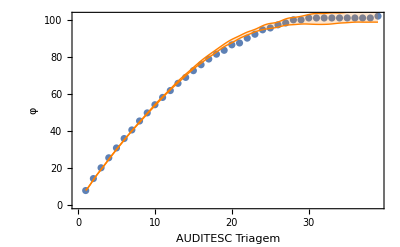

/Users/neylemke/Luisa/BancodeDadosDoutorado/varphipqqtri.pdf

```mathematica
lisvariassimul={};
lisvariassimul2={};
lisvariassimul3={};
lisvariassimul4={};
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
size0=Length[lisRTM];
size=Length[Join[liscontrole,lisintervencao]];
Do[
simul=(Nest[Step[p,q],#,150]& /@Table[0,{size0}]);
lisvariassimul=Append[lisvariassimul,simul];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Nest[Step[p,q],#,25]&/@simul2;
       simul4=Nest[Step[p,q],#,25]& /@simul3;
lisvariassimul2=Append[lisvariassimul2,simul2];
lisvariassimul3=Append[lisvariassimul3,simul3];
lisvariassimul4=Append[lisvariassimul3,simul4];
,
{10}]
lisdata=lisRTM;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisvariassimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
frametext=Style[#,"FontSize"->16]&/@{"AUDITESC Triagem","φ"};
gr1=Show[{ListPlot[lisExp,Frame->True,FrameLabel->frametext],ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},InterpolationOrder->5]
}]
Export[prefix<>"varphipqqtri.pdf",Show[gr1]]
```

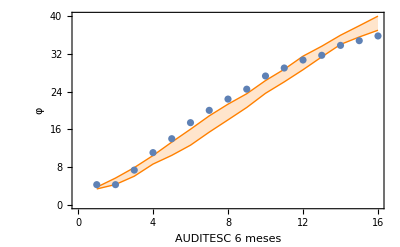

/Users/neylemke/Luisa/BancodeDadosDoutorado/varphipqqz6.pdf

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"AUDITESC 6 meses","φ"};
lisdata=Join[liscontrolez6,lisintervencaoz6];
lisdatasimul=lisvariassimul3;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr1=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},Frame->True,FrameLabel->frametext],ListPlot[lisExp]
}]
Export[prefix<>"varphipqqz6.pdf",Show[gr1]]
```

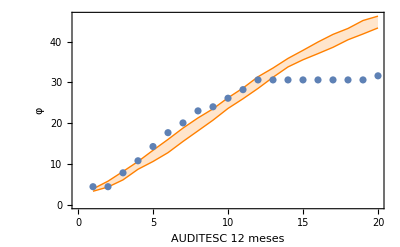

/Users/neylemke/Luisa/BancodeDadosDoutorado/varphipqqz12.pdf

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"AUDITESC 12 meses","φ"};
lisdata=Join[liscontrolez12,lisintervencaoz12];
lisdatasimul=lisvariassimul4;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr1=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},Frame->True,FrameLabel->frametext],ListPlot[lisExp]
}]

Export[prefix<>"varphipqqz12.pdf",Show[gr1]]
```

```mathematica
Mean[Mean/@lisvariassimul3-Mean[Join[liscontrolez6,lisintervencaoz6]]]
Mean[Mean/@lisvariassimul4-Mean[Join[liscontrolez12,lisintervencaoz12]]]
```

5.15521

5.66951

```mathematica
scale=N[Floor[10*(HistogramList[lisRTM][[2,1]])/Length[lisRTM]]/10];
max=1.6;
listicksy=Table[{max*i/5,scale*i/5},{i,0,5}];
```

```mathematica
gr1=SmoothHistogram[{Log[Flatten[lisvariassimul]+1],Log[Flatten[lisvariassimul2]+1],Log[Flatten[lisvariassimul3]+1],Log[Flatten[lisvariassimul4]+1]},PlotLegends->LineLegend[{"Entrevista","LB", "Seis Meses","12 Meses"}],Axes->True,PlotRange->{{0,4},All},Filling->Bottom,PlotStyle->{Thickness[0.01]},Frame->True, FrameLabel->{Style["AUDITESC",FontSize->18],Style["Frequência",FontSize->18]},FrameTicks->{listicksy,{{0,{Log[1+1],1},{Log[3],2},{Log[6],5},{Log[11],10},{Log[21],20},{Log[31],30},{Log[51],50}},None}},PlotLabel->Style["Simulação pqq", "FontSize"->16]]
Export[prefix<>"expdistpqq.pdf",gr1]
```

```mathematica
p
```

0.94

```mathematica
q
```

0.53

### Variação no r

```mathematica
size0=Length[lisRTM];
size=Length[Join[liscontrole,lisintervencao]];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N]
listDistr=ParallelTable[Print[r];Sum[
simul=Table[Steps[p,q,0,150],{size0}];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
(* Print[sizelocal,",",size,",",Length[simul2]]; *)
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
{r,compara[simul3,Join[liscontrolez6,lisintervencaoz6]]+compara[simul4,Join[liscontrolez12,lisintervencaoz12]]},{j,1,100}]/100,{r,0.50,0.75,0.005}];
```

{0.94,0.53,57.072}

0.5

0.525

0.55

0.575

0.555

0.58

0.53

0.505

0.585

0.56

0.535

0.51

0.59

0.565

0.54

0.515

0.595

0.57

0.545

0.52

0.615

0.6

0.635

0.655

0.62

0.605

0.64

0.66

0.625

0.61

0.645

0.665

0.63

0.675

0.65

0.67

0.68

0.695

0.715

0.735

0.7

0.685

0.72

0.74

0.705

0.69

0.725

0.745

0.71

0.73

0.75

```mathematica
distListPythonRisco=listDistr;
```

```mathematica
lisvariassimul={};
lisvariassimul2={};
lisvariassimul3={};
lisvariassimul4={};
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
r=First[First[MinimalBy[distListPythonRisco,Last]]];
Do[

simul=(Steps[p,q,#,150]& /@Table[0,{size0}]);
lisvariassimul=Append[lisvariassimul,simul];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
lisvariassimul2=Append[lisvariassimul2,simul2];
lisvariassimul3=Append[lisvariassimul3,simul3];
lisvariassimul4=Append[lisvariassimul4,simul4];
,
{10}]
```

```mathematica
First[First[MinimalBy[distListPythonRisco,Last]]]
```

0.62

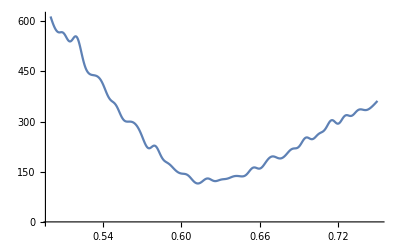

```mathematica
ListPlot[distListPythonRisco,Joined->True,InterpolationOrder->4]
```

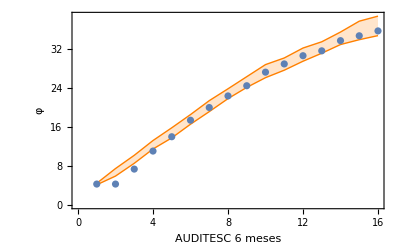

/Users/neylemke/Luisa/BancodeDadosDoutorado/varphipqrz6.pdf

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"AUDITESC 6 meses","φ"};
lisdata=Join[liscontrolez6,lisintervencaoz6];
lisdatasimul=lisvariassimul3;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr1=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},Frame->True,FrameLabel->frametext],ListPlot[lisExp]
}]
Export[prefix<>"varphipqrz6.pdf",gr1]
```

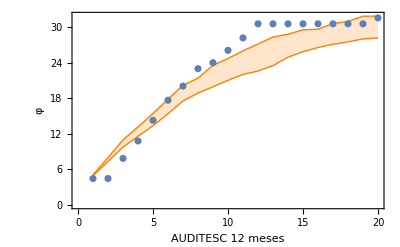

/Users/neylemke/Luisa/BancodeDadosDoutorado/varphipqrz12.pdf

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"AUDITESC 12 meses","φ"};
lisdata=Join[liscontrolez12,lisintervencaoz12];
lisdatasimul=lisvariassimul4;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr1=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},Frame->True,FrameLabel->frametext],ListPlot[lisExp]
}]
Export[prefix<>"varphipqrz12.pdf",gr1]
```

```mathematica
Mean[Mean/@lisvariassimul3-Mean[Join[liscontrolez6,lisintervencaoz6]]]
Mean[Mean/@lisvariassimul4-Mean[Join[liscontrolez12,lisintervencaoz12]]]
```

1.16667

-0.651042

```mathematica
r
```

```mathematica
0.625
```

0.625

```mathematica
(r-0.5)/(q-0.5)
```

4.8

```mathematica
r-0.5
```

0.115

```mathematica
q-0.5
```

0.04

```mathematica
Mean[Mean/@lisvariassimul2]-Mean[Mean/@lisvariassimul4]//N
```

1.49176

```mathematica
Mean[Join[liscontrole,lisintervencao]]-Mean[Join[liscontrolez12,lisintervencaoz12]]
```

6.625

```mathematica
6.62/1.49
```

4.44295

```mathematica
6.05/1.24
```

4.87903

```mathematica
Mean[Mean/@lisvariassimul2]-Mean[Mean/@lisvariassimul3]//N
```

4.95833

```mathematica
4.95/1.24
```

3.99194

```mathematica
Length[Select[Join[liscontrolez12,lisintervencaoz12],#<8&]]
```

84

```mathematica
ff[x_]:=Length[Select[x,#<8&]]
```

```mathematica
Mean[ff/@lisvariassimul4]//N
```

41.2727

```mathematica
84/41.
```

2.04878

```mathematica
Correlation[lisvariassimul4[[1]],lisvariassimul3[[1]]]//N
```

0.797665

```mathematica
Correlation[lisvariassimul2[[1]],lisvariassimul3[[1]]]//N
```

0.672024

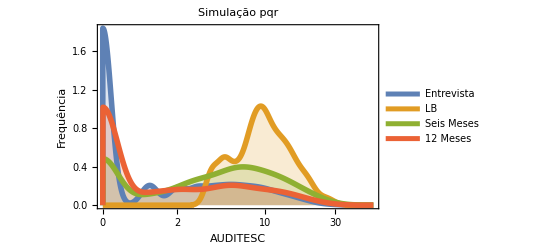

```mathematica
gr1=SmoothHistogram[{Log[Flatten[lisvariassimul]+1],Log[Flatten[lisvariassimul2]+1],Log[Flatten[lisvariassimul3]+1],Log[Flatten[lisvariassimul4]+1]},PlotLegends->LineLegend[{"Entrevista","LB", "Seis Meses","12 Meses"}],Axes->True,PlotRange->{{0,4},All},Filling->Bottom,PlotStyle->{Thickness[0.01]},Frame->True, FrameLabel->{Style["AUDITESC",FontSize->18],Style["Frequência",FontSize->18]},FrameTicks->{{Automatic,None},{{0,{Log[1+1],1},{Log[3],2},{Log[6],5},{Log[11],10},{Log[21],20},{Log[31],30},{Log[51],50}},None}},PlotLabel->Style["Simulação pqr", "FontSize"->16]]
Export[prefix<>"expdistpqr.pdf",gr1]
```

```mathematica
p
```

0.94

```mathematica
q
```

0.53

```mathematica
r
```

0.62

### Grupos C e I

```mathematica
size0=Length[lisRTM];
size=Length[liscontrole];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N]

lisr1=Table[listDistr=ParallelTable[Print[r];Sum[
simul=Table[Steps[p,q,0,150],{size0}];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
(* Print[sizelocal,",",size,",",Length[simul2]]; *)
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
{r,compara[simul3,Join[liscontrolez6]]+compara[simul4,Join[liscontrolez12]]},{j,1,100}]/100,{r,0.55,0.7,0.005}];
First[First[MinimalBy[listDistr,Last]]],{10}];
```

{0.94,0.53,57.7031}

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.675

0.655

0.695

0.64

0.68

0.66

0.7

0.645

0.685

0.665

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.575

0.595

0.555

0.62

0.6

0.56

0.58

0.625

0.605

0.565

0.585

0.63

0.65

0.67

0.69

0.635

0.675

0.655

0.695

0.64

0.68

0.66

0.7

0.645

0.685

0.665

0.55

0.57

0.59

0.61

0.615

0.555

0.575

0.595

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.595

0.555

0.575

0.62

0.6

0.56

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.575

0.595

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.575

0.595

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.665

0.645

0.685

```mathematica
r1=First[First[MinimalBy[listDistr,Last]]]
```

0.6

```mathematica
lisr1
```

{0.625,0.615,0.665,0.61,0.625,0.61,0.64,0.625,0.64,0.63}

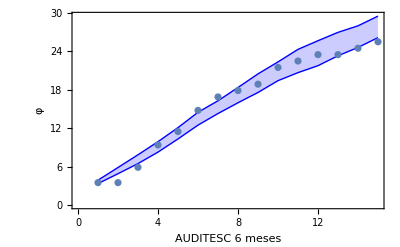

```mathematica
lisvariassimul={};
lisvariassimul2={};
lisvariassimul3={};
lisvariassimul4={};
lisdata=Join[liscontrolez6];
size=Length[lisdata];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
r=First[First[MinimalBy[listDistr,Last]]];
Do[
simul=(Steps[p,q,#,150]& /@Table[0,{size0}]);
lisvariassimul=Append[lisvariassimul,simul];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
lisvariassimul2=Append[lisvariassimul2,simul2];
lisvariassimul3=Append[lisvariassimul3,simul3];
lisvariassimul4=Append[lisvariassimul4,simul4];
,
{10}]

frametext=Style[#,"FontSize"->16]&/@{"AUDITESC 6 meses","φ"};

lisdatasimul=lisvariassimul3;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr1=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Blue}},Frame->True,FrameLabel->frametext],ListPlot[lisExp]
}]
```

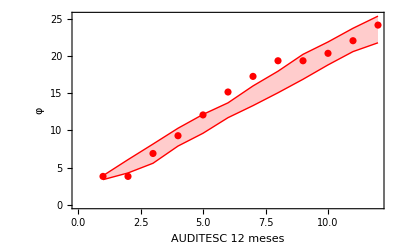

```mathematica
lisvariassimul={};
lisvariassimul2={};
lisvariassimul3={};
lisvariassimul4={};
lisdata=Join[liscontrolez12];
size=Length[lisdata];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
r=First[First[MinimalBy[listDistr,Last]]];
Do[

simul=(Steps[p,q,#,150]& /@Table[0,{size0}]);
lisvariassimul=Append[lisvariassimul,simul];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
lisvariassimul2=Append[lisvariassimul2,simul2];
lisvariassimul3=Append[lisvariassimul3,simul3];
lisvariassimul4=Append[lisvariassimul4,simul4];
,
{10}]

frametext=Style[#,"FontSize"->16]&/@{"AUDITESC 12 meses","φ"};

lisdatasimul=lisvariassimul3;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr2=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Red}},Frame->True,FrameLabel->frametext],ListPlot[lisExp,PlotStyle->{{Thin,Red}}]
}]
```

```mathematica
size0=Length[lisRTM];
size=Length[lisintervencao];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N]
lisr2=Table[listDistr=ParallelTable[Print[r];Sum[
simul=Table[Steps[p,q,0,150],{size0}];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
(* Print[sizelocal,",",size,",",Length[simul2]]; *)
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
{r,compara[simul3,Join[lisintervencaoz6]]+compara[simul4,Join[lisintervencaoz12]]},{j,1,100}]/100,{r,0.55,0.7,0.005}];
First[First[MinimalBy[listDistr,Last]]]
,{10}]
```

{0.94,0.53,57.7031}

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.58

0.6

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.575

0.595

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

0.55

0.57

0.59

0.61

0.615

0.555

0.595

0.575

0.62

0.56

0.6

0.58

0.625

0.565

0.605

0.585

0.63

0.65

0.67

0.69

0.635

0.655

0.675

0.695

0.64

0.66

0.68

0.7

0.645

0.665

0.685

{0.595,0.605,0.59,0.6,0.59,0.59,0.59,0.59,0.595,0.6}

0.63

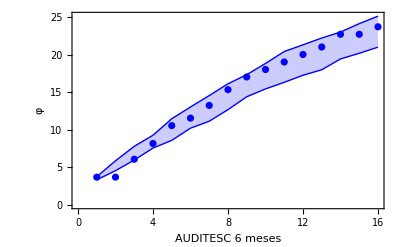

```mathematica
lisvariassimul={};
lisvariassimul2={};
lisvariassimul3={};
lisvariassimul4={};
lisdata=Join[lisintervencaoz6];
size=Length[lisdata];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
r=First[First[MinimalBy[listDistr,Last]]];
r=0.63
Do[

simul=(Steps[p,q,#,150]& /@Table[0,{size0}]);
lisvariassimul=Append[lisvariassimul,simul];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
lisvariassimul2=Append[lisvariassimul2,simul2];
lisvariassimul3=Append[lisvariassimul3,simul3];
lisvariassimul4=Append[lisvariassimul4,simul4];
,
{10}]

frametext=Style[#,"FontSize"->16]&/@{"AUDITESC 6 meses","φ"};

lisdatasimul=lisvariassimul3;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr1=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Blue}},Frame->True,FrameLabel->frametext],ListPlot[lisExp,PlotStyle->{{Thin,Blue}}]
}]
```

```mathematica
r2=First[First[MinimalBy[listDistr,Last]]]
```

0.59

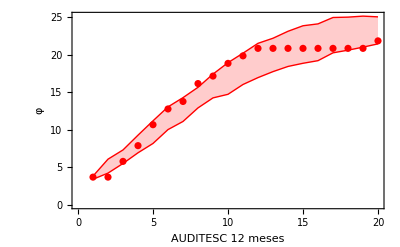

```mathematica
lisvariassimul={};
lisvariassimul2={};
lisvariassimul3={};
lisvariassimul4={};
lisdata=Join[lisintervencaoz12];
size=Length[lisdata];
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
r=First[First[MinimalBy[listDistr,Last]]];
r=0.63;
Do[

simul=(Steps[p,q,#,150]& /@Table[0,{size0}]);
lisvariassimul=Append[lisvariassimul,simul];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
lisvariassimul2=Append[lisvariassimul2,simul2];
lisvariassimul3=Append[lisvariassimul3,simul3];
lisvariassimul4=Append[lisvariassimul4,simul4];
,
{10}]

frametext=Style[#,"FontSize"->16]&/@{"AUDITESC 12 meses","φ"};

lisdatasimul=lisvariassimul3;
lisSumvarias=geraParcialSums[#,Min[lisdata],Max[lisdata]]&/@lisdatasimul;
lisExp=geraParcialSums[lisdata,Min[lisdata],Max[lisdata]];
gr2=Show[{ListPlot[{Mean[lisSumvarias]+StandardDeviation[lisSumvarias],Mean[lisSumvarias]-StandardDeviation[lisSumvarias]},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Red}},Frame->True,FrameLabel->frametext],ListPlot[lisExp,PlotStyle->{{Thin,Red}}]
}]
```

```mathematica
r1-r2
```

0.01

```mathematica
Export[prefix<>"comppqrCIB.pdf",Show[gr1,gr2]]
```

```mathematica
"/Users/neylemke/Luisa/BancodeDadosDoutorado/lis
```

```mathematica
Mean[lisr1]
```

0.6285

```mathematica
lisr2
```

{0.595,0.605,0.59,0.6,0.59,0.59,0.59,0.59,0.595,0.6}

```mathematica
Mean[lisr2]
```

0.5945

```mathematica
StandardDeviation[lisr1]
```

0.016675

```mathematica
StandardDeviation[lisr2]
```

0.00550252

```mathematica
r
```

0.615

```mathematica
LocationTest[{lisr1,lisr2}]
```

0.000155655

```mathematica
Mean[lisr1]
```

0.6285

```mathematica
Mean[lisr2]
```

0.5945

Grupos

### AUDITESC

```mathematica
partGrupos=GroupBy[bbarisco,{#GRUPO,#SEXOS}&];
```

```mathematica
labels={{"C","F"},{"C", "M"},{"I","F"},{"I","M"}};
```

```mathematica
l=1;
lisevol={"AUDITESC","z6AUDITESC","z12AUDITESC"}/.Normal[partGrupos[[l]][All, {"GRUPO", "SEXO","AUDITESC","z6AUDITESC","z12AUDITESC"}]];
lisclus=ClusteringComponents[lisevol,2,1,Method->"KMeans"];
```

```mathematica
lisevol={"AUDITESC"*1.,"z6AUDITESC","z12AUDITESC"}/.Normal[partGrupos[[l]][All,{"GRUPO","SEXO","AUDITESC","z6AUDITESC","z12AUDITESC"}]]
```

{{7.,10 ,10 },{11.,10 ,10 }}

Part::partw: Part {1,2,1,3,2,2,2,3} of {{7.,10 ,10 },{11.,10 ,10 }} does not exist.

Transpose::nmtx: The first two levels of {} cannot be transposed.

ClusteringComponents::distcomp: The values of the options DistanceFunction -> EuclideanDistance and Method -> KMeans are incompatible.

Tally::list: List expected at position 1 in Tally[ClusteringComponents[{{0.,10 ,10 },{4.,10 ,10 },{17.,10 ,10 },{10.,10 ,10 },{10.,10 ,10 }},3,1,Method→KMeans]].

PieChart::ldata: Tally[ClusteringComponents[{{0.,10 ,10 },{4.,10 ,10 },{17.,10 ,10 },{10.,10 ,10 },{10.,10 ,10 }},3,1,Method→KMeans]] is not a valid dataset or list of datasets.

General::stop: Further output of PieChart::ldata will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {} cannot be transposed.

Transpose::nmtx: The first two levels of {Missing[]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part {1,3} of {{7.,11,4},{38.,10 ,10 }} does not exist.

ClusteringComponents::xnum: A non-numeric, negative, or complex dissimilarity value was computed; dissimilarities must be non-negative and real valued.

Tally::list: List expected at position 1 in Tally[ClusteringComponents[{{8.,10 ,10 },{6.,10 ,10 },{10.,12,10 },{14.,10 ,10 },«43»,{21.,10 ,10 },{6.,10 ,10 },{19.,10 ,10 },«5»},3,1,Method→KMeans]].

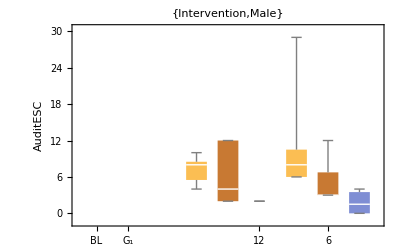
{{-Graphics-,-Graphics-},{PieChart[Tally[ClusteringComponents[{{0.,10 ,10 },{4.,10 ,10 },{17.,10 ,10 },{10.,10 ,10 },{10.,10 ,10 }},3,1,Method→KMeans]],ChartStyle→8,ChartLabels→{G_1,G_2,G_3},PlotLabel→{Control,Male}],-Graphics-},{-Graphics-,-Graphics-},{PieChart[Tally[ClusteringComponents[{{8.,10 ,10 },{6.,10 ,10 },{10.,12,10 },{14.,10 ,10 },{10.,10 ,10 },{23.,10 ,10 },{11.,10 ,10 },{16.,10 ,10 },{14.,10 ,10 },{11.,11,11},{5.,5,10},{9.,5,11},{6.,5,3},{4.,7,7},{29.,3,0},{9.,9,5},{8.,9,10 },{8.,10 ,10 },{21.,10 ,10 },{12.,3,0},{9.,10 ,10 },{9.,10 ,10 },{12.,10 ,10 },{12.,10 ,10 },{15.,10 ,10 },{14.,8,6},{12.,10 ,10 },{19.,10 ,10 },{7.,6,0},{8.,4,2},{6.,10 ,10 },{19.,6,10 },{19.,6,10 },{10.,5,4},{8.,5,7},{18.,10 ,10 },{12.,3,4},{3.,0,0},{9.,10 ,10 },{8.,14,10},{16.,10 ,10 },{5.,10 ,10 },{7.,10 ,10 },{8.,10 ,10 },{5.,0,0},{14.,10 ,10 },{4.,2,2},{21.,10 ,10 },{6.,10 ,10 },{19.,10 ,10 },{8.,10 ,10 },{10.,10 ,10 },{8.,10 ,10 },{2.,10 ,10 },{7.,10 ,10 }},3,1,Method→KMeans]],ChartStyle→8,ChartLabels→{G_1,G_2,G_3},PlotLabel→{Intervention,Male}],-Graphics-}}

```mathematica
ngrupos={3,3,3,3};
ngrupos2={3,2,3,3};
Table[lisevol={"AUDITESC"*1.,"z6AUDITESC","z12AUDITESC"}/.Normal[partGrupos[[l]][All, {"GRUPO", "SEXO","AUDITESC","z6AUDITESC","z12AUDITESC"}]];
lisclus=ClusteringComponents[lisevol,ngrupos[[l]],1,Method->"KMeans"];
(* lisevol2=Table[N[Mean/@Transpose[lisevol[[Flatten[Position[lisclus,k]]]]]],{k,1,2}];*)
{P3=
PieChart[Tally[lisclus]/.{x_,y_}->y,ChartStyle->8,ChartLabels->{"G_1","G_2","G_3"}, PlotLabel->StringReplace[labels[[l]],{"C"->"Control","I"->"Intervention","M"->"Male","F"->"Female"}] ],

gr3=BoxWhiskerChart[Table[Transpose[lisevol[[Flatten[Position[lisclus,k]]]]],{k,1,ngrupos2[[l]]}],ChartLabels->{{"\!\(\*SubscriptBox[\(G\), \(1\)]\)","\!\(\*SubscriptBox[\(G\), \(2\)]\)","\!\(\*SubscriptBox[\(G\), \(3\)]\)"},{"BL","6","12"}},PlotLabel->StringReplace[labels[[l]],{"C"->"Control","I"->"Intervention","M"->"Male","F"->"Female"}],FrameLabel-> "AuditESC"]},{l,1,4}]
```

```mathematica
lisevol={"AUDITESC","z6AUDITESC","z12AUDITESC"}/.Normal[bbarisco1[All, {"AUDITESC","z6AUDITESC","z12AUDITESC"}]];
lisclus=ClusteringComponents[lisevol,3,1,Method->"Optimize"]
```

{1,1,1,2,2,1,2,1,2,1,1,2,1,3,2,3,1,1,1,2,2,3,2,1,2,2,2,1,2,1,1,1,1,2,2,2,2,3,2,2,2,2,1,2,3,2,2,2,2,2,2,2,3,2,2,1,1,1,2,2,2,1,3,3,1,3,1,2,2,1,2,2,3,2,1,2,2,2,2,2,2,2,3,3,2,2,3,3,2,1,2,2,1,1,2,2}

-Graphics-

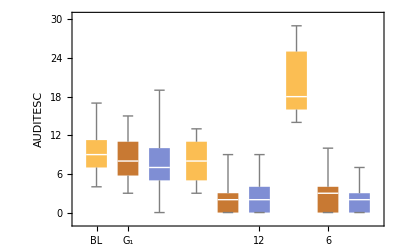

```mathematica
lisevol={"AUDITESC","z6AUDITESC","z12AUDITESC"}/.Normal[bbarisco1[All, {"AUDITESC","z6AUDITESC","z12AUDITESC"}]];
lisclus=ClusteringComponents[lisevol,3,1,Method->"Optimize"];
P3=
PieChart[Last/@Tally[lisclus],ChartStyle->8,ChartLabels->{Style["G_1",FontSize->24],Style["G_2",FontSize->24],Style["G_3",FontSize->24]} ]

gr3=BoxWhiskerChart[Table[Transpose[lisevol[[Flatten[Position[lisclus,k]]]]],{k,1,3}],ChartLabels->{{"\!\(\*SubscriptBox[\(G\), \(1\)]\)","\!\(\*SubscriptBox[\(G\), \(2\)]\)","\!\(\*SubscriptBox[\(G\), \(3\)]\)"},{"BL","6","12"}}, FrameLabel-> "AUDITESC"]
```

```mathematica
Export[prefix<>"perspie.pdf",P3 ]
Export[prefix<>"perscomp.pdf",gr3 ]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/perspie.pdf

/Users/neylemke/Luisa/BancodeDadosDoutorado/perscomp.pdf

```mathematica
lisevol={"AUDITESC","z6AUDITESC","z12AUDITESC"}/.Normal[bbarisco1[All, {"AUDITESC","z6AUDITESC","z12AUDITESC"}]];
lisclus=ClusteringComponents[lisevol,3,1,Method->"Optimize"];
lisclus2=If[#==1,1,0]&/@lisclus;
```

```mathematica
lisclus2//Tally
```

{{1,30},{0,67}}

```mathematica
bbapers=bbarisco1[Flatten[Position[lisclus,1]],lisvarname];
bbanpers=Union[bbarisco1[Flatten[Position[lisclus,2]],lisvarname],bbarisco1[Flatten[Position[lisclus,3]],lisvar]];
```

```mathematica
bbapers2=Dataset@MapThread[Append,{Normal[bbarisco1],Thread["PERS"->lisclus2]}];
```

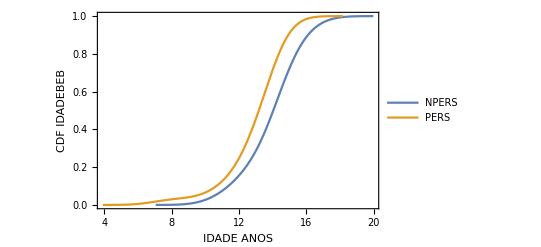

```mathematica
SmoothHistogram[Table[Cases[First/@({0,1}/.GroupBy[{"IDADEBEB","PERS"}/.Normal[bbapers2[All,{"IDADEBEB","PERS"}]],Last])[[i]],_Integer],{i,1,2}],1,"CDF",Frame->True,FrameLabel->{HoldForm[IDADE ANOS],HoldForm[CDF IDADEBEB]},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]},PlotLegends->LineLegend[{"NPERS","PERS"}]]
```

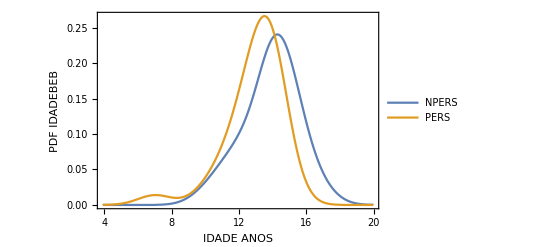

```mathematica
SmoothHistogram[Table[Cases[First/@ ({0,1}/.GroupBy[{"IDADEBEB","PERS"}/.Normal[bbapers2[All,{"IDADEBEB","PERS"}]],Last])[[i]],_Integer],{i,1,2}],1,"PDF",Frame->True,FrameLabel->{HoldForm[IDADE ANOS],HoldForm[PDF IDADEBEB]},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]},PlotLegends->LineLegend[{"NPERS","PERS"}]]
```

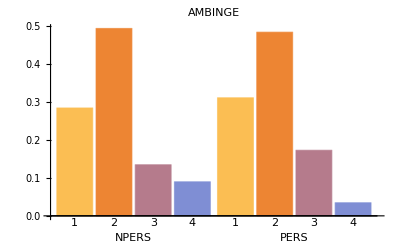

```mathematica
BarChart[Table[N[Last/@Tally[First/@({0,1}/.Normal[GroupBy[{"AMBINGE","PERS"}/.Normal[bbapers2[All,{"AMBINGE","PERS"}]],Last]])⟦i⟧]/Length[({0,1}/.Normal[GroupBy[{"AMBINGE","PERS"}/.Normal[bbapers2[All,{"AMBINGE","PERS"}]],Last]])⟦i⟧]],{i,1,2}],ChartLabels->{{"NPERS","PERS"},{"1","2","3","4"}},PlotLabel->HoldForm["AMBINGE"],LabelStyle->{GrayLevel[0]}]
```

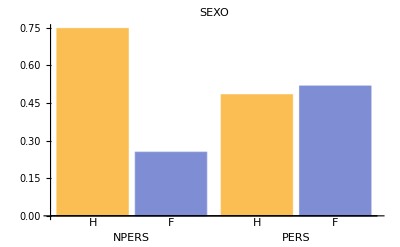

```mathematica
BarChart[Table[N[Last/@Tally[First/@({0,1}/.Normal[GroupBy[{"SEXO","PERS"}/.Normal[bbapers2[All,{"SEXO","PERS"}]],Last]])⟦i⟧]/Length[({0,1}/.Normal[GroupBy[{"SEXO","PERS"}/.Normal[bbapers2[All,{"SEXO","PERS"}]],Last]])⟦i⟧]],{i,1,2}],ChartLabels->{{"NPERS","PERS"},{"H","F","3","4"}},PlotLabel->HoldForm["SEXO"],LabelStyle->{GrayLevel[0]}]
```

```mathematica
PieChart[Table[N[Last/@Tally[First/@({0,1}/.Normal[GroupBy[{"SEXO","PERS"}/.Normal[bbapers2[All,{"SEXO","PERS"}]],Last]])⟦i⟧]/Length[({0,1}/.Normal[GroupBy[{"SEXO","PERS"}/.Normal[bbapers2[All,{"SEXO","PERS"}]],Last]])⟦i⟧]],{i,1,2}],ChartLabels->{{"NPERS","PERS"},{♂,♀,"3","4"}},PlotLabel->HoldForm["SEXO"],LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
PieChart[Table[N[Last/@Tally[First/@({0,1}/.Normal[GroupBy[{"FAMILAL","PERS"}/.Normal[bbapers2[All,{"FAMILAL","PERS"}]],Last]])⟦i⟧]/Length[({0,1}/.Normal[GroupBy[{"FAMILAL","PERS"}/.Normal[bbapers2[All,{"FAMILAL","PERS"}]],Last]])⟦i⟧]],{i,1,2}],ChartLabels->{{"NPERS","PERS"},{"1","2","3","4"}},PlotLabel->HoldForm["FAMILAL"],LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
lisvarname={"SEXO", "RELIGI","INSTRCHE","RELIGIPR","PESO","ALTURA","RACA","IDADEBEB","AMBINGE","IDADE","FAMILAL","PERS"};
bglm=bestGeneralizedLinearModelFitDataset[bbapers2,lisvarname,"AIC",ExponentialFamily->"Binomial",NominalVariables->{sexo,religi,raca}];
bglm["BestFitParameters"]
bglm["ParameterPValues"]
bglm["ParameterConfidenceIntervals"]
bglm["ParameterTable"]
```

{1.43,-0.266907,-0.0645976,0.105452,0.127154}

{0.000239719,0.00646474,0.020439,0.0521798,0.168227}

{{0.666932,2.19307},{-0.459005,-0.0748084},{-0.119213,-0.00998216},{-0.000994764,0.211899},{-0.0537104,0.308018}}

| Estimate | Standard Error | z-Statistic | P-Value
1 | 1.43 | 0.389327 | 3.673 | 0.000239719
sexo | -0.266907 | 0.0980112 | -2.72323 | 0.00646474
idadebeb | -0.0645976 | 0.0278655 | -2.31819 | 0.020439
ambinge | 0.105452 | 0.0543107 | 1.94165 | 0.0521798
familal | 0.127154 | 0.0922793 | 1.37792 | 0.168227

```mathematica
tabparam={
bglm["BestFitParameters"],
bglm["ParameterConfidenceIntervals"],bglm["ParameterPValues"]};
tabparamTex=geraFitTabTex[tabparam,ToString/@bglm["ParameterTable"][[1,1,2;;-1,1]]];
Export[prefix<>"tabparam.tex",tabparamTex, "String"]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/tabparam.tex

Sandbox

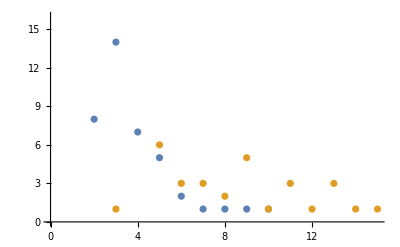

```mathematica
ListPlot[{Tally[Normal[Select[bbapers2,#PERS==0&][All,"z6AUDITESC"]]],
Tally[Normal[Select[bbapers2,#PERS==1&][All,"z6AUDITESC"]]]
}]
```

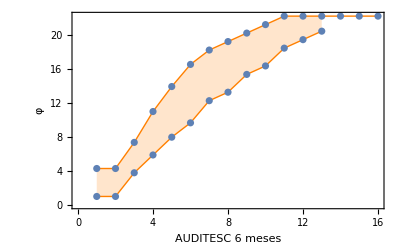

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"AUDITESC 6 meses","φ"};
lisdata=Normal[Select[bbapers2,#PERS==0&][All,"z6AUDITESC"]];
lisdata2=Normal[Select[bbapers2,#PERS==1&][All,"z6AUDITESC"]];
lisSumvarias=geraParcialSums[lisdata,Min[lisdata],Max[lisdata2]];
lisSumvarias2=geraParcialSums[lisdata2,Min[lisdata2],Max[lisdata2]];

gr1=Show[{ListPlot[{lisSumvarias,lisSumvarias2},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},Frame->True,FrameLabel->frametext],ListPlot[lisSumvarias],ListPlot[lisSumvarias2]
}]
Export[prefix<>"varphipqrz6.pdf",gr1]
```

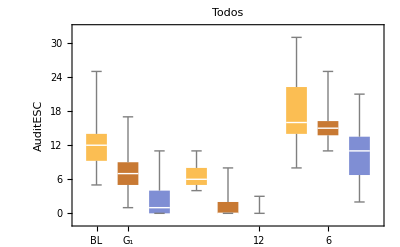

```mathematica
{p,q,error}=First[MinimalBy[distListPythonTri,Last]//N];
r=First[First[MinimalBy[distListPythonRisco,Last]]];

simul=Table[Steps[p,q,0,150],{size0}];
temp1=Select[simul,#>=8&];
temp2=Select[simul,#<8 && #>=4&];
temp3=RandomSample[temp2,Floor[Length[temp2]/2.5]];
temp4=Join[temp1,temp3];
sizelocal=Length[temp4];
simul2=RandomSample[temp4,Min[Length[temp4],size]];
simul3=Steps[p,r,#,25]&/@simul2;
       simul4=Steps[p,r,#,25]& /@simul3;
lisevol=Transpose[{simul2,simul3,simul4}];
lisclus=ClusteringComponents[lisevol,3,1,Method->"Optimize"];

gr3=BoxWhiskerChart[Table[Transpose[lisevol[[Flatten[Position[lisclus,k]]]]],{k,1,3}],ChartLabels->{{"\!\(\*SubscriptBox[\(G\), \(1\)]\)","\!\(\*SubscriptBox[\(G\), \(2\)]\)","\!\(\*SubscriptBox[\(G\), \(3\)]\)"},{"BL","6","12"}},PlotLabel->"Todos", FrameLabel-> "AuditESC"]
```

```mathematica
Entropy[lisclus]//N
```

0.963789

```mathematica
lisSumvarias
```

{{3.94444,6.7362,8.83481,10.528,13.6074,16.6868,19.9894,22.5989,24.292,27.0838,29.8755},{4.3673,7.31321,9.6995,12.3089,12.3089,15.3884,18.1801,20.7896,23.399,25.7853,27.4785},{4.21888,6.60517,9.21461,12.1605,14.9523,18.0317,19.0317,21.6412,23.7398,26.6857,29.072},{4.68888,7.07517,9.46147,11.5601,13.9464,16.045,18.9909,21.6003,23.6989,26.6449,27.6449},{4.66356,6.76217,9.14847,11.7579,14.3673,17.1591,18.8523,21.4617,24.0711,25.0711,27.1697},{4.61092,6.99721,8.69036,11.4821,14.0916,16.701,17.701,19.3941,21.7804,24.5722,26.2653},{4.3673,7.44674,10.0562,11.7493,15.0519,17.8437,20.23,23.4272,24.4272,25.4272,27.1203},{4.29584,7.24175,8.93489,11.5443,14.1538,17.351,19.9604,21.6536,22.6536,24.7522,27.3616},{4.43399,6.5326,9.32436,12.4038,14.5024,16.601,19.7982,21.8969,24.6886,26.3818,28.7681},{4.3673,6.75359,8.8522,11.644,13.7426,16.352,19.2979,20.9911,23.3774,25.7637,28.8431}}

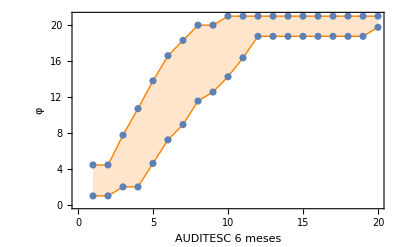

/Users/neylemke/Luisa/BancodeDadosDoutorado/varphipqrz6.pdf

lissimul2

```mathematica
frametext=Style[#,"FontSize"->16]&/@{"AUDITESC 6 meses","φ"};
lisdata=Normal[Select[bbapers2,#PERS==0&][All,"z12AUDITESC"]];
lisdata2=Normal[Select[bbapers2,#PERS==1&][All,"z12AUDITESC"]];
lisSumvarias=geraParcialSums[lisdata,Min[lisdata],Max[lisdata2]];
lisSumvarias2=geraParcialSums[lisdata2,Min[lisdata2],Max[lisdata2]];

gr1=Show[{ListPlot[{lisSumvarias,lisSumvarias2},Joined->True,Filling->{1->{2}},PlotStyle->{{Thin,Orange}},Frame->True,FrameLabel->frametext],ListPlot[lisSumvarias],ListPlot[lisSumvarias2]
}]
Export[prefix<>"varphipqrz6.pdf",gr1]
```

```mathematica
lisvarname={"SEXO", "INSTRCHE","IDADEBEB","AMBINGE","IDADE","FAMILAL","PERS"};
lisvar=ToExpression/@(ToLowerCase/@lisvarname);
datapoints=lisvarname/.Normal[bbapers2[All,lisvarname]];
datapoints=Cases[datapoints,Table[_Integer,Length[lisvarname]]];
```

```mathematica
datapointsml=Table[datapoints[[i,1;;-2]]->datapoints[[i,-1]],{i,1,Length[datapoints]}];
```

ClassifierFunction[…]

```mathematica
listeste=RandomChoice[liscases,Floor[Length[datapointsml]/2]];
listrain=Complement[liscases,listeste];
```

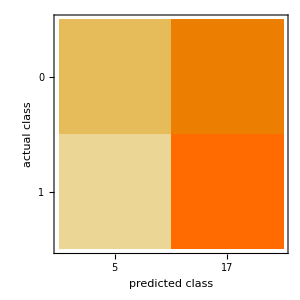

```mathematica
liscases=Table[i,{i,1,Length[datapointsml]}];
lispos=Select[datapointsml,#[[2]]==0&];
lisneg=Select[datapointsml,#[[2]]==1&];
listestepos=RandomChoice[lispos,11];
listesteneg=RandomChoice[lisneg,11];
listrainpos=Complement[lispos,listestepos][[1;;11]];
listrainneg=Complement[lisneg,listesteneg][[1;;11]];
listeste=Join[listestepos,listesteneg];
listrain=Join[listrainpos,listrainneg];
c=Classify[listeste,Method->"LogisticRegression"];
ClassifierMeasurements[c,listrain,"ConfusionMatrixPlot"]
```

```mathematica
?Classify
```

RowBox[{"Classify", "[", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["example", "TI"], StyleBox["1", "TR"]], "→", SubscriptBox[StyleBox["class", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["example", "TI"], StyleBox["2", "TR"]], "→", SubscriptBox[StyleBox["class", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] generates a RowBox[{"ClassifierFunction", "[", StyleBox["…", "TR"], "]"}] based on the examples and classes given.
RowBox[{"Classify", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["example", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["example", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "→", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["class", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["class", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] also generates a RowBox[{"ClassifierFunction", "[", StyleBox["…", "TR"], "]"}] based on the examples and classes given.
RowBox[{"Classify", "[", RowBox[{"<|", RowBox[{RowBox[{SubscriptBox[StyleBox["class", "TI"], StyleBox["1", "TR"]], "→", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["example", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["example", "TI"], StyleBox["12", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], ",", RowBox[{SubscriptBox[StyleBox["class", "TI"], StyleBox["2", "TR"]], "→", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["example", "TI"], StyleBox["21", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], ",", StyleBox["…", "TR"]}], "|>"}], "]"}] generates a RowBox[{"ClassifierFunction", "[", StyleBox["…", "TR"], "]"}] based on an association of classes with their examples.
RowBox[{"Classify", "[", RowBox[{StyleBox["training", "TI"], ",", StyleBox["data", "TI"]}], "]"}] attempts to classify StyleBox["data", "TI"] using a classifier function deduced from the training set given.
RowBox[{"Classify", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"name\",\"TI\"]\)\"", ShowStringCharacters->True], ",", StyleBox["data", "TI"]}], "]"}] attempts to classify StyleBox["data", "TI"] using the built-in classifier function represented by "
StyleBox["name", "TI"]".
RowBox[{"Classify", "[", RowBox[{StyleBox["…", "TR"], ",", StyleBox["data", "TI"], ",", StyleBox["prop", "TI"]}], "]"}] gives the specified property of the classification associated with StyleBox["data", "TI"].

### AUDITC

-Graphics-

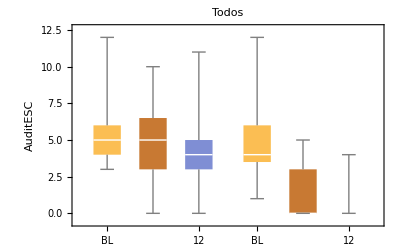

```mathematica
lisevol={"AUDITC","z6AUDITC","z12AUDITC"}/.Normal[bbarisco1[All, {"AUDITC","z6AUDITC","z12AUDITC"}]];
lisclus=ClusteringComponents[lisevol,2,1,Method->"Optimize"];
lisclus2=If[#==2,1,0]&/@lisclus;
P3=
PieChart[Last/@Tally[lisclus],ChartStyle->8,ChartLabels->{"G_1","G_2","G_3"}, PlotLabel->"Todos" ]

gr3=BoxWhiskerChart[Table[Transpose[lisevol[[Flatten[Position[lisclus,k]]]]],{k,1,2}],ChartLabels->{{"\!\(\*SubscriptBox[\(G\), \(1\)]\)","\!\(\*SubscriptBox[\(G\), \(2\)]\)","\!\(\*SubscriptBox[\(G\), \(3\)]\)"},{"BL","6","12"}},PlotLabel->"Todos", FrameLabel-> "AuditESC"]
```

```mathematica
bbapers2=Dataset@MapThread[Append,{Normal[bbarisco1],Thread["PERS"->lisclus2]}];
lisvarname={"SEXO", "RELIGI","INSTRCHE","RELIGIPR","PESO","RACA","IDADEBEB","AMBINGE","AMBEB","IDADE","FAMILAL","PERS"};
bglm=bestGeneralizedLinearModelFitDataset[bbapers2,lisvarname,"AIC",ExponentialFamily->"Binomial",NominalVariables->{sexo,religi,raca}];
bglm["BestFitParameters"]
bglm["ParameterPValues"]
bglm["ParameterConfidenceIntervals"]
bglm["ParameterTable"]
```

{2.8244,-0.0179754,0.0638082,-0.113983,-0.170603}

{0.0135702,0.00399878,0.0341123,0.0877089,0.125203}

{{0.581803,5.067},{-0.0302159,-0.00573498},{0.00478175,0.122835},{-0.244811,0.0168447},{-0.38868,0.0474738}}

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.8244 | 1.1442 | 2.46844 | 0.0135702
altura | -0.0179754 | 0.00624525 | -2.87826 | 0.00399878
idadebeb | 0.0638082 | 0.0301161 | 2.11874 | 0.0341123
ambinge | -0.113983 | 0.0667501 | -1.70761 | 0.0877089
familal | -0.170603 | 0.111266 | -1.53329 | 0.125203

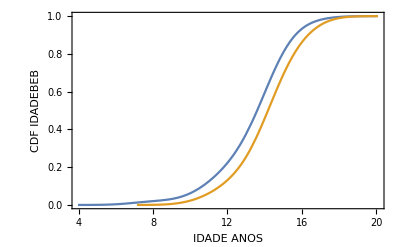

```mathematica
SmoothHistogram[Table[Cases[First/@ GroupBy[{"IDADEBEB","PERS"}/.Normal[bbapers2[All,{"IDADEBEB","PERS"}]],Last][[i]],_Integer],{i,1,2}],1,"CDF",Frame->True,FrameLabel->{HoldForm[IDADE ANOS],HoldForm[CDF IDADEBEB]},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

```mathematica
Show[%1885,Frame->True,FrameLabel->{HoldForm[IDADE ANOS],HoldForm[CDF IDADEBEB]},PlotLabel->None,LabelStyle->{FontFamily->"Arial",12,GrayLevel[0]}]
```

-Graphics-

```mathematica
Clear[stepSelect]
```

```mathematica
data=Join[{"SEXO", "RELIGI","INSTRCHE","RELIGIPR","PESO","ALTURA",1}/.Normal[bbapers],{"SEXO", "RELIGI","INSTRCHE","RELIGIPR","PESO","ALTURA",0}/.Normal[bbanpers]];
glm=GeneralizedLinearModelFit[data,{sexo,religi,instrche,religipr,peso,altura},{sexo,religi,instrche,religipr,peso,altura}, NominalVariables->{sexo,religi},ExponentialFamily->"Binomial"];
glm["BestFitParameters"]
glm["ParameterPValues"]
glm["ParameterConfidenceIntervals"]
glm["ParameterTable"]
```

{-20.38,1.02053,15.7042,15.2401,15.537,0.177824,0.0366504,-0.0733484,0.00275701,0.0208192}

{0.993223,0.173446,0.994778,0.994932,0.994834,0.999958,0.916253,0.688233,0.890823,0.635999}

{{-4723.42,4682.66},{-0.448896,2.48996},{-4687.32,4718.73},{-4687.78,4718.26},{-4687.48,4718.56},{-6650.9,6651.25},{-0.646469,0.71977},{-0.431626,0.284929},{-0.0366101,0.0421242},{-0.0653943,0.107033}}

| Estimate | Standard Error | z-Statistic | P-Value
1 | -20.38 | 2399.56 | -0.00849325 | 0.993223
sexo[1] | 1.02053 | 0.749723 | 1.36121 | 0.173446
religi[0] | 15.7042 | 2399.54 | 0.00654467 | 0.994778
religi[1] | 15.2401 | 2399.54 | 0.00635126 | 0.994932
religi[2] | 15.537 | 2399.54 | 0.00647499 | 0.994834
religi[3] | 0.177824 | 3393.47 | 0.000052402 | 0.999958
instrche | 0.0366504 | 0.348537 | 0.105155 | 0.916253
religipr | -0.0733484 | 0.182798 | -0.401254 | 0.688233
peso | 0.00275701 | 0.0200857 | 0.137263 | 0.890823
altura | 0.0208192 | 0.0439873 | 0.473301 | 0.635999

{sexo,idadebeb,instrche,religipr}

Conclusão o modelo abaixo é o melhor!

```mathematica
lisvarnames={"SEXO","IDADEBEB"};
datalm=Join[Append[lisvarnames,1]/.Normal[bbapers],Append[lisvarnames,0]/.Normal[bbanpers]];
datalm=Cases[datalm,Table[_Integer,Length[lisvarnames]+1]];
lisvar=ToExpression/@(ToLowerCase/@lisvarnames);
glm=GeneralizedLinearModelFit[datalm,lisvar,lisvar,NominalVariables->{sexo}, ExponentialFamily->"Binomial"];
glm["BestFitParameters"]
glm["ParameterPValues"]
glm["ParameterConfidenceIntervals"]
glm["ParameterTable"]
glm["AIC"]
```

{2.7717,1.33131,-0.320163}

{0.176458,0.0122657,0.0343827}

{{-1.24714,6.79055},{0.289419,2.37321},{-0.616779,-0.0235467}}

| Estimate | Standard Error | z-Statistic | P-Value
1 | 2.7717 | 2.05047 | 1.35174 | 0.176458
sexo[1] | 1.33131 | 0.531589 | 2.50441 | 0.0122657
idadebeb | -0.320163 | 0.151338 | -2.11555 | 0.0343827

91.8781

```mathematica
data=Join[{"SEXO","IDADEBEB",0,"AUDITESC"}/.Normal[bbarisco1],{"SEXO","IDADEBEB",6,"z6AUDITESC"}/.Normal[bbarisco1],{"SEXO","IDADEBEB",12,"z12AUDITESC"}/.Normal[bbarisco1]];
data=Cases[data,{_Integer,_Integer,_Integer,_Integer}];
```

```mathematica
glm=GeneralizedLinearModelFit[data,{sexo,idadebeb,time},{sexo,idadebeb,time}, NominalVariables->{sexo},ExponentialFamily->"Poisson"];
glm["BestFitParameters"]
glm["ParameterPValues"]
glm["ParameterConfidenceIntervals"]
glm["ParameterTable"]
```

{3.13473,0.0574325,-0.0669389,-0.102871}

{3.67329×10^-54,0.289718,4.30059×10^-6,4.02214×10^-68}

{{2.73825,3.53121},{-0.0488878,0.163753},{-0.0954831,-0.0383947},{-0.114431,-0.0913108}}

| Estimate | Standard Error | z-Statistic | P-Value
1 | 3.13473 | 0.202289 | 15.4963 | 3.67329×10^-54
sexo[1] | 0.0574325 | 0.054246 | 1.05874 | 0.289718
idadebeb | -0.0669389 | 0.0145636 | -4.5963 | 4.30059×10^-6
time | -0.102871 | 0.0058982 | -17.4411 | 4.02214×10^-68

```mathematica
lisevol={"AUDITESC","z6AUDITESC","z12AUDITESC"}/.Normal[bbarisco1[All, {"AUDITESC","z6AUDITESC","z12AUDITESC"}]];
liscoeff=Table[lm=LinearModelFit[Log[lisevol[[i]]+1],x,x];
lm["BestFitParameters"][[2]],{i,1,Length[lisevol]}];
lisdata={"SEXO","INSTRCHE","IDADEBEB"}/.Normal[bbarisco1[All,{"SEXO","INSTRCHE","IDADEBEB"}]];
lisdatacomp=Flatten/@(Transpose@{lisdata,liscoeff});
lisdatacomp=Cases[lisdatacomp,{_Integer,_Integer,_Integer,_}];
lm=LinearModelFit[lisdatacomp,{sexo,instrche,idadebeb},{sexo,instrche,idadebeb}, NominalVariables->{sexo},IncludeConstantBasis->True];
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.511438 | 0.518359 | 0.986648 | 0.326827
sexo[1] | 0.351475 | 0.118068 | 2.9769 | 0.00386398
instrche | -0.107338 | 0.0681412 | -1.57523 | 0.1192
idadebeb | -0.0713668 | 0.0326715 | -2.18437 | 0.0319002

```mathematica
lisevol={"AUDITESC","z6AUDITESC","z12AUDITESC"}/.Normal[bbarisco1[All, {"AUDITESC","z6AUDITESC","z12AUDITESC"}]];
liscoeff=Table[lm=LinearModelFit[Log[lisevol[[i]]+1],x,x];
lm["BestFitParameters"][[1]],{i,1,Length[lisevol]}];
lisdata={"SEXO","INSTRCHE","IDADEBEB","GRUPO"}/.Normal[bbarisco1[All,{"SEXO","INSTRCHE","IDADEBEB","GRUPO"}]];
lisdatacomp=Flatten/@(Transpose@{lisdata,liscoeff});
lisdatacomp=Cases[lisdatacomp,{_Integer,_Integer,_Integer,_,_}];
lm=LinearModelFit[lisdatacomp,{sexo,instrche,idadebeb,grupo},{sexo,instrche,idadebeb,grupo}, NominalVariables->{sexo}];
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.17798 | 0.882597 | 2.46769 | 0.0157887
sexo[1] | -0.421047 | 0.198772 | -2.11824 | 0.0373387
instrche | 0.0822157 | 0.11472 | 0.716665 | 0.475721
idadebeb | 0.0455838 | 0.0550317 | 0.82832 | 0.410017
grupo[C] | -0.150003 | 0.184591 | -0.812622 | 0.418908

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.461316 | 0.526347 | 0.876449 | 0.383478
sexo[1] | 0.352891 | 0.11854 | 2.97698 | 0.0038762
instrche | -0.106497 | 0.0684145 | -1.55665 | 0.123603
idadebeb | -0.0706014 | 0.0328188 | -2.15125 | 0.0345516
grupo[C] | 0.0695843 | 0.110083 | 0.632107 | 0.529166

```mathematica
REvaluate["
  {
library(nlme)

ctrl <- lmeControl(opt='optim')

bba.lme.1<-lme(value ~variable*GRUPO*SEXOS, random = ~ variable |ID,data=gdf.m,control=ctrl,na.action=na.exclude)
summary(bba.lme.1)}"]
```

REvaluate::rerr: Failed to retrieve the value for variable or piece of code 
  {
library(nlme)

ctrl <- lmeControl(opt='optim')

bba.lme.1<-lme(value ~variable*GRUPO*SEXOS, random = ~ variable |ID,data=gdf.m,control=ctrl,na.action=na.exclude)
summary(bba.lme.1)}. The following R error was encountered: Error in is.data.frame(data) : object 'gdf.m' not found

$Failed

```mathematica
fsex/@data[[All,1]]//Tally
```

{{F,51},{M,31}}

```mathematica
data=Join[{"SEXO","INSTRCHE","IDADEBEB",1}/.Normal[bbapers],{"SEXO", "INSTRCHE","IDADEBEB",0}/.Normal[bbanpers]];
data=Delete[data,-14];

data=data/.{a_,b_,c_,d_,x_}:>{a,b,c,fclasse[d],x};
glm=GeneralizedLinearModelFit[data,{sexo,instrche,idadebeb},{sexo,instrche,idadebeb}, NominalVariables->{sexo},ExponentialFamily->"Binomial"];
glm["BestFitParameters"]
glm["ParameterPValues"]
glm["ParameterConfidenceIntervals"]
glm["ParameterTable"]
```

GeneralizedLinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

GeneralizedLinearModelFit[{{2,2,13,1},{1,4,14,1},{1,3,12,1},{2,4,13,1},{1,3,14,1},{1,2,13,1},{1,3,14,1},{2,3,14,1},{2,2,14,1},{1,3,10,1},{2,3,14,1},{1,2,14,1},{1,4,11,1},{2,2,12,1},{1,4,15,1},{1,4,12,1},{1,4,13,1},{2,3,14,1},{2,2,7,1},{1,1,17,1},{2,1,11,1},{1,3,13,1},{1,2,14,1},{1,3,12,0},{1,4,13,0},{1,2,15,0},{1,3,15,0},{1,3,14,0},{1,3,11,0},{1,3,14,0},{1,3,14,0},{1,3,15,0},{1,3,12,0},{1,4,10,0},{1,4,14,0},{1,1,16,0},{1,2,15,0},{1,3,15,0},{1,3,15,0},{1,3,11,0},{2,1,14,0},{2,2,14,0},{2,2,12,0},{2,2,15,0},{2,2,14,0},{2,3,11,0},{2,1,15,0},{2,1,15,0},{2,1,14,0},{2,2,14,0},{2,2,14,0},{2,2,15,0},{2,2,13,0},{2,2,17,0},{2,2,14,0},{2,2,14,0},{2,2,14,0},{2,2,13,0},{2,3,14,0},{2,3,16,0},{2,3,,0},{2,3,15,0},{2,3,15,0},{2,3,13,0},{2,3,14,0},{2,3,14,0},{2,3,15,0},{2,3,11,0},{2,3,14,0},{2,3,17,0},{2,3,14,0},{2,3,14,0},{2,4,15,0},{2,4,13,0},{2,4,14,0},{2,4,10,0},{2,2,15,0},{2,2,12,0},{2,2,15,0},{2,3,16,0},{2,3,16,0},{2,1,16,0},{2,2,14,0}},{sexo,instrche,idadebeb},{sexo,instrche,idadebeb},NominalVariables→{sexo},ExponentialFamily→Binomial][BestFitParameters]

GeneralizedLinearModelFit[{{2,2,13,1},{1,4,14,1},{1,3,12,1},{2,4,13,1},{1,3,14,1},{1,2,13,1},{1,3,14,1},{2,3,14,1},{2,2,14,1},{1,3,10,1},{2,3,14,1},{1,2,14,1},{1,4,11,1},{2,2,12,1},{1,4,15,1},{1,4,12,1},{1,4,13,1},{2,3,14,1},{2,2,7,1},{1,1,17,1},{2,1,11,1},{1,3,13,1},{1,2,14,1},{1,3,12,0},{1,4,13,0},{1,2,15,0},{1,3,15,0},{1,3,14,0},{1,3,11,0},{1,3,14,0},{1,3,14,0},{1,3,15,0},{1,3,12,0},{1,4,10,0},{1,4,14,0},{1,1,16,0},{1,2,15,0},{1,3,15,0},{1,3,15,0},{1,3,11,0},{2,1,14,0},{2,2,14,0},{2,2,12,0},{2,2,15,0},{2,2,14,0},{2,3,11,0},{2,1,15,0},{2,1,15,0},{2,1,14,0},{2,2,14,0},{2,2,14,0},{2,2,15,0},{2,2,13,0},{2,2,17,0},{2,2,14,0},{2,2,14,0},{2,2,14,0},{2,2,13,0},{2,3,14,0},{2,3,16,0},{2,3,,0},{2,3,15,0},{2,3,15,0},{2,3,13,0},{2,3,14,0},{2,3,14,0},{2,3,15,0},{2,3,11,0},{2,3,14,0},{2,3,17,0},{2,3,14,0},{2,3,14,0},{2,4,15,0},{2,4,13,0},{2,4,14,0},{2,4,10,0},{2,2,15,0},{2,2,12,0},{2,2,15,0},{2,3,16,0},{2,3,16,0},{2,1,16,0},{2,2,14,0}},{sexo,instrche,idadebeb},{sexo,instrche,idadebeb},NominalVariables→{sexo},ExponentialFamily→Binomial][ParameterPValues]

GeneralizedLinearModelFit[{{2,2,13,1},{1,4,14,1},{1,3,12,1},{2,4,13,1},{1,3,14,1},{1,2,13,1},{1,3,14,1},{2,3,14,1},{2,2,14,1},{1,3,10,1},{2,3,14,1},{1,2,14,1},{1,4,11,1},{2,2,12,1},{1,4,15,1},{1,4,12,1},{1,4,13,1},{2,3,14,1},{2,2,7,1},{1,1,17,1},{2,1,11,1},{1,3,13,1},{1,2,14,1},{1,3,12,0},{1,4,13,0},{1,2,15,0},{1,3,15,0},{1,3,14,0},{1,3,11,0},{1,3,14,0},{1,3,14,0},{1,3,15,0},{1,3,12,0},{1,4,10,0},{1,4,14,0},{1,1,16,0},{1,2,15,0},{1,3,15,0},{1,3,15,0},{1,3,11,0},{2,1,14,0},{2,2,14,0},{2,2,12,0},{2,2,15,0},{2,2,14,0},{2,3,11,0},{2,1,15,0},{2,1,15,0},{2,1,14,0},{2,2,14,0},{2,2,14,0},{2,2,15,0},{2,2,13,0},{2,2,17,0},{2,2,14,0},{2,2,14,0},{2,2,14,0},{2,2,13,0},{2,3,14,0},{2,3,16,0},{2,3,,0},{2,3,15,0},{2,3,15,0},{2,3,13,0},{2,3,14,0},{2,3,14,0},{2,3,15,0},{2,3,11,0},{2,3,14,0},{2,3,17,0},{2,3,14,0},{2,3,14,0},{2,4,15,0},{2,4,13,0},{2,4,14,0},{2,4,10,0},{2,2,15,0},{2,2,12,0},{2,2,15,0},{2,3,16,0},{2,3,16,0},{2,1,16,0},{2,2,14,0}},{sexo,instrche,idadebeb},{sexo,instrche,idadebeb},NominalVariables→{sexo},ExponentialFamily→Binomial][ParameterConfidenceIntervals]

GeneralizedLinearModelFit[{{2,2,13,1},{1,4,14,1},{1,3,12,1},{2,4,13,1},{1,3,14,1},{1,2,13,1},{1,3,14,1},{2,3,14,1},{2,2,14,1},{1,3,10,1},{2,3,14,1},{1,2,14,1},{1,4,11,1},{2,2,12,1},{1,4,15,1},{1,4,12,1},{1,4,13,1},{2,3,14,1},{2,2,7,1},{1,1,17,1},{2,1,11,1},{1,3,13,1},{1,2,14,1},{1,3,12,0},{1,4,13,0},{1,2,15,0},{1,3,15,0},{1,3,14,0},{1,3,11,0},{1,3,14,0},{1,3,14,0},{1,3,15,0},{1,3,12,0},{1,4,10,0},{1,4,14,0},{1,1,16,0},{1,2,15,0},{1,3,15,0},{1,3,15,0},{1,3,11,0},{2,1,14,0},{2,2,14,0},{2,2,12,0},{2,2,15,0},{2,2,14,0},{2,3,11,0},{2,1,15,0},{2,1,15,0},{2,1,14,0},{2,2,14,0},{2,2,14,0},{2,2,15,0},{2,2,13,0},{2,2,17,0},{2,2,14,0},{2,2,14,0},{2,2,14,0},{2,2,13,0},{2,3,14,0},{2,3,16,0},{2,3,,0},{2,3,15,0},{2,3,15,0},{2,3,13,0},{2,3,14,0},{2,3,14,0},{2,3,15,0},{2,3,11,0},{2,3,14,0},{2,3,17,0},{2,3,14,0},{2,3,14,0},{2,4,15,0},{2,4,13,0},{2,4,14,0},{2,4,10,0},{2,2,15,0},{2,2,12,0},{2,2,15,0},{2,3,16,0},{2,3,16,0},{2,1,16,0},{2,2,14,0}},{sexo,instrche,idadebeb},{sexo,instrche,idadebeb},NominalVariables→{sexo},ExponentialFamily→Binomial][ParameterTable]

-Graphics-

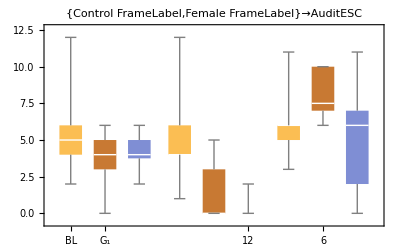

```mathematica
l=1;
lisevol={"AUDITC"*1.,"z6AUDITC","z12AUDITC"}/.Normal[bbarisco1[All, {"AUDITC","z6AUDITC","z12AUDITC"}]];
lisclus=ClusteringComponents[lisevol,3,1,Method->"KMeans"];
P3=
PieChart[Tally[lisclus]/.{x_,y_}->y,ChartStyle->8,ChartLabels->{"G_1","G_2","G_3"}, PlotLabel->StringReplace[labels[[l]],{"C"->"Control","I"->"Intervention","M"->"Male","F"->"Female"}] ]

gr3=BoxWhiskerChart[Table[Transpose[lisevol[[Flatten[Position[lisclus,k]]]]],{k,1,ngrupos[[l]]}],ChartLabels->{{"\!\(\*SubscriptBox[\(G\), \(1\)]\)","\!\(\*SubscriptBox[\(G\), \(2\)]\)","\!\(\*SubscriptBox[\(G\), \(3\)]\)"},{"BL","6","12"}},PlotLabel->StringReplace[labels[[l]],{"C"->"Control","I"->"Intervention","M"->"Male","F"->"Female"}]FrameLabel-> "AuditESC"]

lisvar={"SEXO", "RELIGI","CLASSE","INSTRCHE","RELIGIPR","PESO","ALTURA","RACA","IDADEBEB","AMIGBEB","AMBINGE","IDADE","FAMILAL","CLASSE"};
bbapers=bbarisco1[Flatten[Position[lisclus,3]],lisvar];
bbanpers=Union[bbarisco1[Flatten[Position[lisclus,2]],lisvar],bbarisco1[Flatten[Position[lisclus,1]],lisvar]];
```

```mathematica
data=Join[{"SEXO","INSTRCHE","IDADEBEB",1}/.Normal[bbapers],{"SEXO", "INSTRCHE","IDADEBEB",0}/.Normal[bbanpers]];
data=Delete[data,-14];
data=Delete[data,-24];
data=data/.{a_,b_,c_,d_,x_}:>{a,b,c,fclasse[d],x};
glm=GeneralizedLinearModelFit[data,{sexo,instrche,idadebeb},{sexo,instrche,idadebeb}, NominalVariables->{sexo},ExponentialFamily->"Binomial"];
glm["BestFitParameters"]
glm["ParameterPValues"]
glm["ParameterConfidenceIntervals"]
glm["ParameterTable"]
```

{0.157063,0.120711,0.137544,-0.159708}

{0.951656,0.849595,0.714254,0.331771}

{{-4.92053,5.23466},{-1.12688,1.3683},{-0.598718,0.873807},{-0.482226,0.16281}}

| Estimate | Standard Error | z-Statistic | P-Value
1 | 0.157063 | 2.59066 | 0.0606268 | 0.951656
sexo[1] | 0.120711 | 0.636539 | 0.189636 | 0.849595
instrche | 0.137544 | 0.375651 | 0.366149 | 0.714254
idadebeb | -0.159708 | 0.164553 | -0.970554 | 0.331771

```mathematica
data[[-24,-2]]
```

```mathematica
lisevol=Transpose[{partauditc1[[4]],partauditc1z6[[4]],partauditc1z12[[4]]}];
lisclus=ClusteringComponents[lisevol,2,1,Method->"KMeans"];
lisevol2=Table[N[Mean/@ Transpose[lisevol[[Flatten[Position[lisclus,k]]]]]],{k,1,2}];

P4=PieChart[Tally[lisclus]/.{x_,y_}->y,ChartStyle->8,ChartLabels->Reverse[{"\!\(\*SubscriptBox[\(G\), \(2\)]\)","\!\(\*SubscriptBox[\(G\), \(1\)]\)"}],PlotLabel->StringReplace[labels[[4]],{"C"->"Control","I"->"Intervention","M"->"Male","F"->"Female"}]];

gr4=BoxWhiskerChart[Reverse[Table[Transpose[lisevol[[Flatten[Position[lisclus,k]]]]],{k,1,2}]],ChartLabels->{{"G_1","G_2"},{"BL","6","12"}},FrameLabel-> "AuditC", PlotLabel->StringReplace[labels[[4]],{"C"->"Control","I"->"Intervention","M"->"Male","F"->"Female"}]];
```

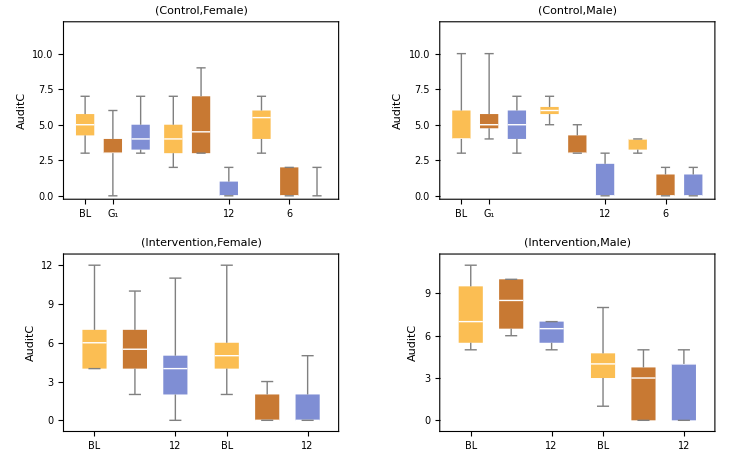

```mathematica
gg1=GraphicsGrid[{{gr1,gr2},{gr3,gr4}}]
```

```mathematica
Export["/Users/neylemke/Luisa/BancodeDadosDoutorado/chartsgrupos.pdf",gg1]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/chartsgrupos.pdf

```mathematica
gg2=GraphicsGrid[{{P1,P2},{P3,P4}}]
```

-Graphics-

```mathematica
Export["/Users/neylemke/Luisa/BancodeDadosDoutorado/piechartsgrupos.pdf",gg2]
```

/Users/neylemke/Luisa/BancodeDadosDoutorado/piechartsgrupos.pdf

{4.90909,3.27273,4.27273}

```mathematica
liskkk=Table[
lisevol[[Flatten[Position[lisclus,k]]] ],{k,1,2}]
```

{{{3,0,5},{4,4,5},{4,5,4},{5,5,4},{3,3,3},{3,0,0},{5,3,4},{8,3,4},{2,0,0},{1,3,0},{4,0,0}},{{5,7,7},{11,6,7},{6,10,6},{8,10,5}}}

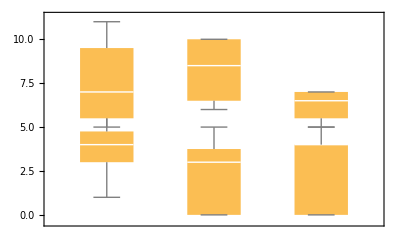

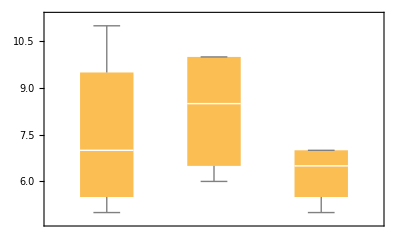

```mathematica
gr1=BoxWhiskerChart[liskkk[[1]]//Transpose];
gr2=BoxWhiskerChart[liskkk[[2]]//Transpose];
Show[gr1,gr2]
```

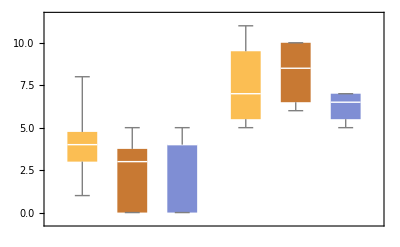

```mathematica
BoxWhiskerChart[{liskkk[[1]]//Transpose,liskkk[[2]]//Transpose}]
```

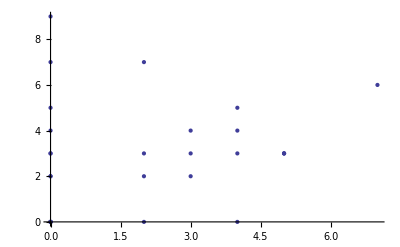

```mathematica
ListPlot[Transpose[{partauditc1z12[[1]],partauditc1z6[[1]]}]]
```

```mathematica
partauditc1[[2,-4]]=3;
Table[lm=LinearModelFit[Transpose[{partauditc1[[j]],partauditc1z6[[j]]}],x,x];
(lm["BestFitParameters"])[[2]],{j,1,4}]
```

{0.141533,0.525485,0.01,0.739407}

```mathematica
partauditc1[[2,-4]]=3;
Table[lm=LinearModelFit[Transpose[{partauditc1z12[[j]],partauditc1z6[[j]]}],x,x];
(lm["BestFitParameters"])[[2]],{j,1,4}]
```

{0.22564,0.782609,0.572822,0.931507}

```mathematica
partauditc1[[2,-4]]=3;
Table[lm=LinearModelFit[Transpose[{partauditc1z12[[j]],partauditc1[[j]]}],x,x];
(lm["BestFitParameters"])[[2]],{j,1,4}]
```

{0.080294,0.0652174,0.0833518,0.694064}

```mathematica
labels
```

{(C,F),(C,M),(I,M),(I,F)}

```mathematica
Prepend[Table[{labels[[i]],{SignedRankTest[{partauditc1[[i]],partauditc1z6[[i]]}],SignedRankTest[{partauditc1[[i]],partauditc1z12[[i]]}],SignedRankTest[{partauditc1z6[[i]],partauditc1z12[[i]]}]}},{i,1,4}],{"Grupo",{".1dLB-6","LB-12","6-12"}}]//Grid
```

Grupo | {.1dLB-6,LB-12,6-12}
(C,F) | {0.00220239,0.0000266405,0.128089}
(C,M) | {0.105978,0.011412,0.0136217}
(I,M) | {0.00168005,0.000378463,0.49192}
(I,F) | {0.205371,0.0578773,0.714815}

```mathematica
labels
```

{(C,F),(C,M),(I,M),(I,F)}

```mathematica
μ=Mean[Select[data1[[All,col["AUDIT1"]]],NumberQ]]+Mean[Select[data1[[All,col["AUDIT2"]]],NumberQ]]+Mean[Select[data1[[All,col["AUDIT3"]]],NumberQ]]//N;partauditc1[[2,-4]]=3;
Table[lm=LinearModelFit[Transpose[{partauditc1[[j]]-μ,partauditc1z6[[j]]-μ}],x,x];
{lm["BestFitParameters"][[1]],lm["ParameterConfidenceIntervals"][[1]],lm["ParameterPValues"][[1]]},{j,1,4}]
```

{{0.996031,{-1.43325,3.42531},0.407585},{0.794442,{-2.18965,3.77853},0.578805},{1.22912,{-1.44785,3.90608},0.351337},{0.0206969,{-2.63058,2.67197},0.986801}}

```mathematica
partauditc1[[2,-4]]=3;
Table[lm=LinearModelFit[Transpose[{partauditc1[[j]],partauditc1z6[[j]]}],x,x];
(lm["BestFitParameters"]),{j,1,4}]
```

{{2.19345,0.141533},{1.45631,0.525485},{2.61,0.01},{0.384181,0.739407}}

```mathematica
"SOLV12","COCA12","CRACK12","MACON12","ANFETA12","LSD12","ANTICOLI","ANABOLI1","EXT12","TRANQ12","TABC12","TABCDIA1","OTRDRG12"
```